```mathematica
NS[]
```

```mathematica
Co[x_]:=Flatten[x,{1-Total[Flatten[{x}]]}];
```

```mathematica
le=417641;f0=Round[Flatten@Import["_scripts-mc_fullnetwork\\stensola_activity_freqs_bins417641.csv"]*le]/le;
```

```mathematica
Export["_scripts-mc_fullnetwork\\stensola_activity_absfreqs_bins417641.csv",f0*le];
```

```mathematica
nn=1000;n=Length[f0]-1
```

65

```mathematica
(* truncated projection *)
(hh=Table[Binomial[n,a]*Binomial[nn-n,aa-a]/Binomial[nn,aa],{a,0,n},{aa,0,nn}]);
```

```mathematica
hhs=Total[T@hh];
```

```mathematica
hh/hhs;
```

```mathematica
ffsol=(n+1)/(nn+1)*f0.hh;
```

```mathematica
{Min[#],Max[#]}&@ffsol//N
```

{0.,0.0327699}

```mathematica
Total[ffsol]
```

1

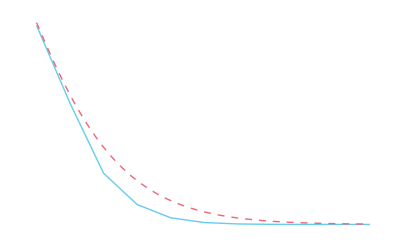

```mathematica
ListPlot[{f0*n,ffsol*nn},Joined->True,DataRange->{0,1},PlotRange->{{All,0.15},All}]
```

```mathematica
ind=(n+1)*(n+2)/2+(nn-n)*(n+1)-1
```

63920

```mathematica
le/ind//N
```

6.53381

```mathematica
f6=Flatten@Import["_scripts-mc_fullnetwork\\stensola2_6mom_prior2_N65.csv"];
```

```mathematica
ffsol6=(n+1)/(nn+1)*f6.hh;
```

```mathematica
{Min[#],Max[#]}&@ffsol6//N
```

{0.,0.0328048}

```mathematica
Total[ffsol6]
```

1.

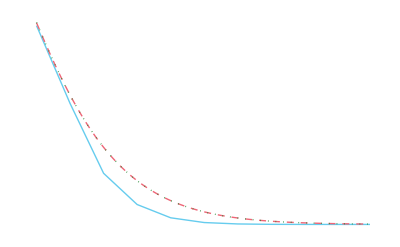

```mathematica
ListPlot[{f0*n,ffsol*nn,ffsol6*nn},Joined->True,DataRange->{0,1},PlotRange->{{All,0.15},All}]
```

```mathematica
ihht=Inverse[hht];
```

```mathematica
(ffs=ihht.(f0-hh[[;;,1]]))//N
```

{2.25148×10^6,-1.00149×10^7,2.59976×10^7,-4.34102×10^7,4.83585×10^7,-3.59454×10^7,1.71941×10^7,-4.80352×10^6,597279.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
(cm0orig=Import["_scripts-mc_fullnetwork\\stensola_devc10000_fcov.csv"])//MF
```

(7.25392×10^-7 | -2.25735×10^-7 | -2.51358×10^-7 | -1.45117×10^-7 | -6.7417×10^-8 | -2.50597×10^-8 | -8.11832×10^-9 | -1.95692×10^-9 | -5.37836×10^-10 | -8.56659×10^-11 | -5.81352×10^-12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2.25735×10^-7 | 8.91271×10^-8 | 6.62071×10^-8 | 4.1457×10^-8 | 1.89211×10^-8 | 7.04009×10^-9 | 2.26154×10^-9 | 5.45232×10^-10 | 1.5111×10^-10 | 2.41338×10^-11 | 1.05191×10^-12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2.51358×10^-7 | 6.62071×10^-8 | 1.01891×10^-7 | 4.68676×10^-8 | 2.38363×10^-8 | 8.77559×10^-9 | 2.86898×10^-9 | 6.91487×10^-10 | 1.86954×10^-10 | 3.06942×10^-11 | 2.48648×10^-12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1.45117×10^-7 | 4.1457×10^-8 | 4.68676×10^-8 | 3.66605×10^-8 | 1.24953×10^-8 | 5.35537×10^-9 | 1.7283×10^-9 | 4.1497×10^-10 | 1.17294×10^-10 | 1.89674×10^-11 | 1.50073×10^-12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-6.7417×10^-8 | 1.89211×10^-8 | 2.38363×10^-8 | 1.24953×10^-8 | 9.19344×10^-9 | 1.90481×10^-9 | 8.05506×10^-10 | 1.9943×10^-10 | 5.2843×10^-11 | 7.89058×10^-12 | 3.57714×10^-13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2.50597×10^-8 | 7.04009×10^-9 | 8.77559×10^-9 | 5.35537×10^-9 | 1.90481×10^-9 | 1.75165×10^-9 | 1.35408×10^-10 | 7.3243×10^-11 | 2.04429×10^-11 | 2.72457×10^-12 | 3.38009×10^-13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-8.11832×10^-9 | 2.26154×10^-9 | 2.86898×10^-9 | 1.7283×10^-9 | 8.05506×10^-10 | 1.35408×10^-10 | 3.32896×10^-10 | -2.17698×10^-11 | 6.51043×10^-12 | 8.93697×10^-13 | 5.6456×10^-14 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1.95692×10^-9 | 5.45232×10^-10 | 6.91487×10^-10 | 4.1497×10^-10 | 1.9943×10^-10 | 7.3243×10^-11 | -2.17698×10^-11 | 6.26066×10^-11 | -8.45366×10^-12 | 1.59972×10^-13 | 1.96497×10^-14 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5.37836×10^-10 | 1.5111×10^-10 | 1.86954×10^-10 | 1.17294×10^-10 | 5.2843×10^-11 | 2.04429×10^-11 | 6.51043×10^-12 | -8.45366×10^-12 | 1.27492×10^-11 | -1.61235×10^-12 | -1.93758×10^-15 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-8.56659×10^-11 | 2.41338×10^-11 | 3.06942×10^-11 | 1.89674×10^-11 | 7.89058×10^-12 | 2.72457×10^-12 | 8.93697×10^-13 | 1.59972×10^-13 | -1.61235×10^-12 | 1.91194×10^-12 | -9.79333×10^-14 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5.81352×10^-12 | 1.05191×10^-12 | 2.48648×10^-12 | 1.50073×10^-12 | 3.57714×10^-13 | 3.38009×10^-13 | 5.6456×10^-14 | 1.96497×10^-14 | -1.93758×10^-15 | -9.79333×10^-14 | 1.02444×10^-13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
(cm0=cm0orig[[1;;n,1;;n]])//MF
```

(7.25392×10^-7 | -2.25735×10^-7 | -2.51358×10^-7 | -1.45117×10^-7 | -6.7417×10^-8 | -2.50597×10^-8 | -8.11832×10^-9 | -1.95692×10^-9 | -5.37836×10^-10 | -8.56659×10^-11 | -5.81352×10^-12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2.25735×10^-7 | 8.91271×10^-8 | 6.62071×10^-8 | 4.1457×10^-8 | 1.89211×10^-8 | 7.04009×10^-9 | 2.26154×10^-9 | 5.45232×10^-10 | 1.5111×10^-10 | 2.41338×10^-11 | 1.05191×10^-12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2.51358×10^-7 | 6.62071×10^-8 | 1.01891×10^-7 | 4.68676×10^-8 | 2.38363×10^-8 | 8.77559×10^-9 | 2.86898×10^-9 | 6.91487×10^-10 | 1.86954×10^-10 | 3.06942×10^-11 | 2.48648×10^-12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1.45117×10^-7 | 4.1457×10^-8 | 4.68676×10^-8 | 3.66605×10^-8 | 1.24953×10^-8 | 5.35537×10^-9 | 1.7283×10^-9 | 4.1497×10^-10 | 1.17294×10^-10 | 1.89674×10^-11 | 1.50073×10^-12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-6.7417×10^-8 | 1.89211×10^-8 | 2.38363×10^-8 | 1.24953×10^-8 | 9.19344×10^-9 | 1.90481×10^-9 | 8.05506×10^-10 | 1.9943×10^-10 | 5.2843×10^-11 | 7.89058×10^-12 | 3.57714×10^-13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2.50597×10^-8 | 7.04009×10^-9 | 8.77559×10^-9 | 5.35537×10^-9 | 1.90481×10^-9 | 1.75165×10^-9 | 1.35408×10^-10 | 7.3243×10^-11 | 2.04429×10^-11 | 2.72457×10^-12 | 3.38009×10^-13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-8.11832×10^-9 | 2.26154×10^-9 | 2.86898×10^-9 | 1.7283×10^-9 | 8.05506×10^-10 | 1.35408×10^-10 | 3.32896×10^-10 | -2.17698×10^-11 | 6.51043×10^-12 | 8.93697×10^-13 | 5.6456×10^-14 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1.95692×10^-9 | 5.45232×10^-10 | 6.91487×10^-10 | 4.1497×10^-10 | 1.9943×10^-10 | 7.3243×10^-11 | -2.17698×10^-11 | 6.26066×10^-11 | -8.45366×10^-12 | 1.59972×10^-13 | 1.96497×10^-14 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5.37836×10^-10 | 1.5111×10^-10 | 1.86954×10^-10 | 1.17294×10^-10 | 5.2843×10^-11 | 2.04429×10^-11 | 6.51043×10^-12 | -8.45366×10^-12 | 1.27492×10^-11 | -1.61235×10^-12 | -1.93758×10^-15 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-8.56659×10^-11 | 2.41338×10^-11 | 3.06942×10^-11 | 1.89674×10^-11 | 7.89058×10^-12 | 2.72457×10^-12 | 8.93697×10^-13 | 1.59972×10^-13 | -1.61235×10^-12 | 1.91194×10^-12 | -9.79333×10^-14 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5.81352×10^-12 | 1.05191×10^-12 | 2.48648×10^-12 | 1.50073×10^-12 | 3.57714×10^-13 | 3.38009×10^-13 | 5.6456×10^-14 | 1.96497×10^-14 | -1.93758×10^-15 | -9.79333×10^-14 | 1.02444×10^-13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
(* We take a standard deviation equal to half the "frequency quantum" 1/T as a minimum variance *)
(thick=(1/le/2)^2)//N
```

1.43329×10^-12

```mathematica
(cm0new2=cm0+thick*(hht.(IdentityMatrix[nn+1]-1/(nn+1))[[2;;,2;;]].T[hht]))//N//MF
```

```mathematica
(cm0new=cm0+thick*(hht.(IdentityMatrix[nn+1]-1/(nn+1))[[2;;,2;;]].T[hht]))//N//MF
```

(7.25397×10^-7 | -2.25735×10^-7 | -2.5136×10^-7 | -1.45119×10^-7 | -6.74181×10^-8 | -2.50602×10^-8 | -8.11854×10^-9 | -1.957×10^-9 | -5.37859×10^-10 | -8.5672×10^-11 | -5.81489×10^-12 | -2.7488×10^-16 | -4.87994×10^-17 | -7.7025×10^-18 | -1.0849×10^-18 | -1.36775×10^-19 | -1.54729×10^-20 | -1.57387×10^-21 | -1.44183×10^-22 | -1.19115×10^-23 | -8.88253×10^-25 | -5.98298×10^-26 | -3.64145×10^-27 | -2.0029×10^-28 | -9.95435×10^-30 | -4.46856×10^-31 | -1.81071×10^-32 | -6.6171×10^-34 | -2.17835×10^-35 | -6.45075×10^-37 | -1.71543×10^-38 | -4.08827×10^-40 | -8.7113×10^-42 | -1.65507×10^-43 | -2.79491×10^-45 | -4.17983×10^-47 | -5.51271×10^-49 | -6.38095×10^-51 | -6.44581×10^-53 | -5.64537×10^-55 | -4.25379×10^-57 | -2.73236×10^-59 | -1.47966×10^-61 | -6.66395×10^-64 | -2.45362×10^-66 | -7.22352×10^-69 | -1.65022×10^-71 | -2.80261×10^-74 | -3.30954×10^-77 | -2.40903×10^-80
-2.25735×10^-7 | 8.91278×10^-8 | 6.62072×10^-8 | 4.14568×10^-8 | 1.89208×10^-8 | 7.03991×10^-9 | 2.26146×10^-9 | 5.45201×10^-10 | 1.511×10^-10 | 2.41311×10^-11 | 1.05128×10^-12 | -1.29456×10^-16 | -2.34316×10^-17 | -3.75711×10^-18 | -5.36125×10^-19 | -6.8333×10^-20 | -7.80247×10^-21 | -8.00023×10^-22 | -7.38012×10^-23 | -6.13417×10^-24 | -4.59896×10^-25 | -3.11253×10^-26 | -1.9025×10^-27 | -1.05046×10^-28 | -5.23889×10^-30 | -2.3592×10^-31 | -9.58725×10^-33 | -3.51283×10^-34 | -1.15923×10^-35 | -3.4405×10^-37 | -9.16813×10^-39 | -2.18916×10^-40 | -4.673×10^-42 | -8.89304×10^-44 | -1.5041×10^-45 | -2.25267×10^-47 | -2.97506×10^-49 | -3.44804×10^-51 | -3.4873×10^-53 | -3.05773×10^-55 | -2.30648×10^-57 | -1.48305×10^-59 | -8.03894×10^-62 | -3.62381×10^-64 | -1.33543×10^-66 | -3.93479×10^-69 | -8.99616×10^-72 | -1.52899×10^-74 | -1.80686×10^-77 | -1.31612×10^-80
-2.5136×10^-7 | 6.62072×10^-8 | 1.01892×10^-7 | 4.68681×10^-8 | 2.38366×10^-8 | 8.77571×10^-9 | 2.86902×10^-9 | 6.915×10^-10 | 1.86958×10^-10 | 3.0695×10^-11 | 2.48665×10^-12 | 3.05442×10^-17 | 4.98784×10^-18 | 7.28797×10^-19 | 9.55613×10^-20 | 1.12714×10^-20 | 1.19825×10^-21 | 1.14991×10^-22 | 9.97399×10^-24 | 7.82643×10^-25 | 5.55946×10^-26 | 3.57641×10^-27 | 2.08387×10^-28 | 1.09969×10^-29 | 5.25415×10^-31 | 2.27161×10^-32 | 8.88022×10^-34 | 3.13568×10^-35 | 9.98873×10^-37 | 2.86613×10^-38 | 7.39447×10^-40 | 1.7117×10^-41 | 3.54653×10^-43 | 6.55863×10^-45 | 1.07909×10^-46 | 1.57375×10^-48 | 2.02581×10^-50 | 2.29047×10^-52 | 2.26179×10^-54 | 1.93783×10^-56 | 1.42936×10^-58 | 8.99345×10^-61 | 4.77352×10^-63 | 2.10838×10^-65 | 7.61741×10^-68 | 2.20171×10^-70 | 4.94064×10^-73 | 8.246×10^-76 | 9.57386×10^-79 | 6.85472×10^-82
-1.45119×10^-7 | 4.14568×10^-8 | 4.68681×10^-8 | 3.66611×10^-8 | 1.24958×10^-8 | 5.35558×10^-9 | 1.7284×10^-9 | 4.15002×10^-10 | 1.17304×10^-10 | 1.897×10^-11 | 1.50131×10^-12 | 1.16427×10^-16 | 2.06181×10^-17 | 3.24587×10^-18 | 4.55984×10^-19 | 5.73397×10^-20 | 6.47071×10^-21 | 6.56652×10^-22 | 6.00235×10^-23 | 4.94843×10^-24 | 3.6829×10^-25 | 2.47613×10^-26 | 1.50447×10^-27 | 8.2616×10^-29 | 4.09975×10^-30 | 1.83777×10^-31 | 7.43683×10^-33 | 2.71429×10^-34 | 8.92477×10^-36 | 2.63991×10^-37 | 7.01276×10^-39 | 1.66961×10^-40 | 3.55422×10^-42 | 6.74657×10^-44 | 1.13831×10^-45 | 1.70096×10^-47 | 2.24162×10^-49 | 2.59273×10^-51 | 2.61723×10^-53 | 2.29067×10^-55 | 1.72491×10^-57 | 1.10728×10^-59 | 5.99273×10^-62 | 2.69741×10^-64 | 9.92626×10^-67 | 2.92079×10^-69 | 6.66921×10^-72 | 1.1321×10^-74 | 1.33626×10^-77 | 9.72231×10^-81
-6.74181×10^-8 | 1.89208×10^-8 | 2.38366×10^-8 | 1.24958×10^-8 | 9.19377×10^-9 | 1.90499×10^-9 | 8.05587×10^-10 | 1.9946×10^-10 | 5.28522×10^-11 | 7.89306×10^-12 | 3.58289×10^-13 | 1.17116×10^-16 | 2.10463×10^-17 | 3.35501×10^-18 | 4.76436×10^-19 | 6.04777×10^-20 | 6.88143×10^-21 | 7.03449×10^-22 | 6.47204×10^-23 | 5.36679×10^-24 | 4.01524×10^-25 | 2.71239×10^-26 | 1.65512×10^-27 | 9.12469×10^-29 | 4.54437×10^-30 | 2.04382×10^-31 | 8.29589×10^-33 | 3.03638×10^-34 | 1.001×10^-35 | 2.96812×10^-37 | 7.90252×10^-39 | 1.88544×10^-40 | 4.02163×10^-42 | 7.64802×10^-44 | 1.29267×10^-45 | 1.9348×10^-47 | 2.55375×10^-49 | 2.9581×10^-51 | 2.99021×10^-53 | 2.62056×10^-55 | 1.97579×10^-57 | 1.26984×10^-59 | 6.8803×10^-62 | 3.10025×10^-64 | 1.14204×10^-66 | 3.36375×10^-69 | 7.68784×10^-72 | 1.30619×10^-74 | 1.54306×10^-77 | 1.12362×10^-80
-2.50602×10^-8 | 7.03991×10^-9 | 8.77571×10^-9 | 5.35558×10^-9 | 1.90499×10^-9 | 1.75175×10^-9 | 1.35457×10^-10 | 7.32616×10^-11 | 2.04487×10^-11 | 2.72617×10^-12 | 3.38386×10^-13 | 7.77078×10^-17 | 1.41011×10^-17 | 2.26673×10^-18 | 3.24229×10^-19 | 4.14179×10^-20 | 4.73899×10^-21 | 4.86834×10^-22 | 4.49882×10^-23 | 3.74529×10^-24 | 2.81207×10^-25 | 1.90575×10^-26 | 1.16632×10^-27 | 6.44714×10^-29 | 3.21876×10^-30 | 1.45091×10^-31 | 5.90154×10^-33 | 2.1642×10^-34 | 7.14745×10^-36 | 2.12287×10^-37 | 5.66087×10^-39 | 1.35258×10^-40 | 2.88897×10^-42 | 5.50106×10^-44 | 9.30906×10^-46 | 1.39492×10^-47 | 1.84313×10^-49 | 2.13712×10^-51 | 2.16239×10^-53 | 1.8968×10^-55 | 1.43134×10^-57 | 9.20675×10^-60 | 4.99232×10^-62 | 2.25121×10^-64 | 8.29867×10^-67 | 2.44593×10^-69 | 5.59378×10^-72 | 9.5099×10^-75 | 1.12411×10^-77 | 8.19019×10^-81
-8.11854×10^-9 | 2.26146×10^-9 | 2.86902×10^-9 | 1.7284×10^-9 | 8.05587×10^-10 | 1.35457×10^-10 | 3.32919×10^-10 | -2.17608×10^-11 | 6.51331×10^-12 | 8.94489×10^-13 | 5.66446×10^-14 | 3.92091×10^-17 | 7.17107×10^-18 | 1.16059×10^-18 | 1.66997×10^-19 | 2.14442×10^-20 | 2.46499×10^-21 | 2.54273×10^-22 | 2.35843×10^-23 | 1.96996×10^-24 | 1.48357×10^-25 | 1.00819×10^-26 | 6.18558×10^-28 | 3.42711×10^-29 | 1.71462×10^-30 | 7.74402×10^-32 | 3.15556×10^-33 | 1.15914×10^-34 | 3.83413×10^-36 | 1.14044×10^-37 | 3.04523×10^-39 | 7.28538×10^-41 | 1.55795×10^-42 | 2.96991×10^-44 | 5.0311×10^-46 | 7.54638×10^-48 | 9.98061×10^-50 | 1.1583×10^-51 | 1.17298×10^-53 | 1.02974×10^-55 | 7.77643×10^-58 | 5.00566×10^-60 | 2.71618×10^-62 | 1.22563×10^-64 | 4.52091×10^-67 | 1.33329×10^-69 | 3.05096×10^-72 | 5.18975×10^-75 | 6.13778×10^-78 | 4.4742×10^-81
-1.957×10^-9 | 5.45201×10^-10 | 6.915×10^-10 | 4.15002×10^-10 | 1.9946×10^-10 | 7.32616×10^-11 | -2.17608×10^-11 | 6.261×10^-11 | -8.45253×10^-12 | 1.60289×10^-13 | 1.97258×10^-14 | 1.59322×10^-17 | 2.93346×10^-18 | 4.7755×10^-19 | 6.90692×10^-20 | 8.90986×10^-21 | 1.02837×10^-21 | 1.06469×10^-22 | 9.90785×10^-24 | 8.30064×10^-25 | 6.26824×10^-26 | 4.27029×10^-27 | 2.62595×10^-28 | 1.45796×10^-29 | 7.3085×10^-31 | 3.30678×10^-32 | 1.3497×10^-33 | 4.96557×10^-35 | 1.64486×10^-36 | 4.89913×10^-38 | 1.30984×10^-39 | 3.13737×10^-41 | 6.71664×10^-43 | 1.28174×10^-44 | 2.17346×10^-46 | 3.26314×10^-48 | 4.31956×10^-50 | 5.01728×10^-52 | 5.08496×10^-54 | 4.4674×10^-56 | 3.37615×10^-58 | 2.17472×10^-60 | 1.18083×10^-62 | 5.33162×10^-65 | 1.96783×10^-67 | 5.80677×10^-70 | 1.32949×10^-72 | 2.2627×10^-75 | 2.67738×10^-78 | 1.95266×10^-81
-5.37859×10^-10 | 1.511×10^-10 | 1.86958×10^-10 | 1.17304×10^-10 | 5.28522×10^-11 | 2.04487×10^-11 | 6.51331×10^-12 | -8.45253×10^-12 | 1.27496×10^-11 | -1.61224×10^-12 | -1.91207×10^-15 | 5.38048×10^-18 | 9.96484×10^-19 | 1.63062×10^-19 | 2.36924×10^-20 | 3.06885×10^-21 | 3.5551×10^-22 | 3.69292×10^-23 | 3.44696×10^-24 | 2.89575×10^-25 | 2.19222×10^-26 | 1.49692×10^-27 | 9.22462×10^-29 | 5.13167×10^-30 | 2.57708×10^-31 | 1.16798×10^-32 | 4.77475×10^-34 | 1.75921×10^-35 | 5.83542×10^-37 | 1.74029×10^-38 | 4.65848×10^-40 | 1.11708×10^-41 | 2.39406×10^-43 | 4.57321×10^-45 | 7.76223×10^-47 | 1.16644×10^-48 | 1.54539×10^-50 | 1.79647×10^-52 | 1.82212×10^-54 | 1.602×10^-56 | 1.21153×10^-58 | 7.8092×10^-61 | 4.24295×10^-63 | 1.91693×10^-65 | 7.07927×10^-68 | 2.09015×10^-70 | 4.7881×10^-73 | 8.15318×10^-76 | 9.6522×10^-79 | 7.04285×10^-82
-8.5672×10^-11 | 2.41311×10^-11 | 3.0695×10^-11 | 1.897×10^-11 | 7.89306×10^-12 | 2.72617×10^-12 | 8.94489×10^-13 | 1.60289×10^-13 | -1.61224×10^-12 | 1.91197×10^-12 | -9.7926×10^-14 | 1.5411×10^-18 | 2.86903×10^-19 | 4.71652×10^-20 | 6.88136×10^-21 | 8.94654×10^-22 | 1.0399×10^-22 | 1.08351×10^-23 | 1.01417×10^-24 | 8.54161×10^-26 | 6.48157×10^-27 | 4.43536×10^-28 | 2.73871×10^-29 | 1.52637×10^-30 | 7.67845×10^-32 | 3.48559×10^-33 | 1.42705×10^-34 | 5.26519×10^-36 | 1.74879×10^-37 | 5.2218×10^-39 | 1.39942×10^-40 | 3.3594×10^-42 | 7.20709×10^-44 | 1.37807×10^-45 | 2.3412×10^-47 | 3.52123×10^-49 | 4.6691×10^-51 | 5.43199×10^-53 | 5.51368×10^-55 | 4.85111×10^-57 | 3.67122×10^-59 | 2.36792×10^-61 | 1.28736×10^-63 | 5.81968×10^-66 | 2.15046×10^-68 | 6.35273×10^-71 | 1.45605×10^-73 | 2.48061×10^-76 | 2.93813×10^-79 | 2.14485×10^-82
-5.81489×10^-12 | 1.05128×10^-12 | 2.48665×10^-12 | 1.50131×10^-12 | 3.58289×10^-13 | 3.38386×10^-13 | 5.66446×10^-14 | 1.97258×10^-14 | -1.91207×10^-15 | -9.7926×10^-14 | 1.02446×10^-13 | 3.79752×10^-19 | 7.10264×10^-20 | 1.1725×10^-20 | 1.7171×10^-21 | 2.24001×10^-22 | 2.61173×10^-23 | 2.72895×10^-24 | 2.5609×10^-25 | 2.162×10^-26 | 1.64418×10^-27 | 1.1274×10^-28 | 6.97451×10^-30 | 3.89392×10^-31 | 1.96205×10^-32 | 8.92025×10^-34 | 3.65729×10^-35 | 1.35119×10^-36 | 4.49352×10^-38 | 1.34334×10^-39 | 3.60411×10^-41 | 8.66109×10^-43 | 1.85997×10^-44 | 3.55982×10^-46 | 6.05321×10^-48 | 9.11201×10^-50 | 1.20922×10^-51 | 1.40789×10^-53 | 1.43012×10^-55 | 1.25915×10^-57 | 9.53542×10^-60 | 6.15426×10^-62 | 3.34794×10^-64 | 1.51437×10^-66 | 5.59901×10^-69 | 1.65492×10^-71 | 3.79506×10^-74 | 6.46876×10^-77 | 7.66554×10^-80 | 5.5985×10^-83
-2.7488×10^-16 | -1.29456×10^-16 | 3.05442×10^-17 | 1.16427×10^-16 | 1.17116×10^-16 | 7.77078×10^-17 | 3.92091×10^-17 | 1.59322×10^-17 | 5.38048×10^-18 | 1.5411×10^-18 | 3.79752×10^-19 | 8.13634×10^-20 | 1.52814×10^-20 | 2.53218×10^-21 | 3.72103×10^-22 | 4.86937×10^-23 | 5.69362×10^-24 | 5.96478×10^-25 | 5.61098×10^-26 | 4.74754×10^-27 | 3.61791×10^-28 | 2.48553×10^-29 | 1.54038×10^-30 | 8.6144×10^-32 | 4.34735×10^-33 | 1.97936×10^-34 | 8.12648×10^-36 | 3.00621×10^-37 | 1.00096×10^-38 | 2.99581×10^-40 | 8.04632×10^-42 | 1.93561×10^-43 | 4.16076×10^-45 | 7.9707×10^-47 | 1.35655×10^-48 | 2.04375×10^-50 | 2.71434×10^-52 | 3.16269×10^-54 | 3.21496×10^-56 | 2.83258×10^-58 | 2.14651×10^-60 | 1.38626×10^-62 | 7.54589×10^-65 | 3.41523×10^-67 | 1.2634×10^-69 | 3.7363×10^-72 | 8.57252×10^-75 | 1.46193×10^-77 | 1.73324×10^-80 | 1.26645×10^-83
-4.87994×10^-17 | -2.34316×10^-17 | 4.98784×10^-18 | 2.06181×10^-17 | 2.10463×10^-17 | 1.41011×10^-17 | 7.17107×10^-18 | 2.93346×10^-18 | 9.96484×10^-19 | 2.86903×10^-19 | 7.10264×10^-20 | 1.52814×10^-20 | 2.88096×10^-21 | 4.7903×10^-22 | 7.06143×10^-23 | 9.26726×10^-24 | 1.08646×10^-24 | 1.14098×10^-25 | 1.07573×10^-26 | 9.121×10^-28 | 6.96428×10^-29 | 4.7932×10^-30 | 2.97557×10^-31 | 1.66669×10^-32 | 8.42368×10^-34 | 3.84069×10^-35 | 1.57891×10^-36 | 5.8481×10^-38 | 1.94949×10^-39 | 5.84118×10^-41 | 1.57051×10^-42 | 3.78176×10^-44 | 8.13693×10^-46 | 1.56018×10^-47 | 2.65759×10^-49 | 4.00713×10^-51 | 5.32611×10^-53 | 6.2105×10^-55 | 6.31764×10^-57 | 5.57004×10^-59 | 4.22369×10^-61 | 2.72946×10^-63 | 1.48663×10^-65 | 6.73231×10^-68 | 2.49188×10^-70 | 7.37325×10^-73 | 1.69258×10^-75 | 2.88791×10^-78 | 3.42548×10^-81 | 2.5041×10^-84
-7.7025×10^-18 | -3.75711×10^-18 | 7.28797×10^-19 | 3.24587×10^-18 | 3.35501×10^-18 | 2.26673×10^-18 | 1.16059×10^-18 | 4.7755×10^-19 | 1.63062×10^-19 | 4.71652×10^-20 | 1.1725×10^-20 | 2.53218×10^-21 | 4.7903×10^-22 | 7.99011×10^-23 | 1.18124×10^-23 | 1.55435×10^-24 | 1.82676×10^-25 | 1.9228×10^-26 | 1.81667×10^-27 | 1.54337×10^-28 | 1.1806×10^-29 | 8.13953×10^-31 | 5.06109×10^-32 | 2.83914×10^-33 | 1.43698×10^-34 | 6.56056×10^-36 | 2.70048×10^-37 | 1.00142×10^-38 | 3.34208×10^-40 | 1.00245×10^-41 | 2.69802×10^-43 | 6.50309×10^-45 | 1.40051×10^-46 | 2.68772×10^-48 | 4.58206×10^-50 | 6.91441×10^-52 | 9.19738×10^-54 | 1.07324×10^-55 | 1.09253×10^-57 | 9.63888×10^-60 | 7.31377×10^-62 | 4.72927×10^-64 | 2.57739×10^-66 | 1.16785×10^-68 | 4.32505×10^-71 | 1.28042×10^-73 | 2.9408×10^-76 | 5.02011×10^-79 | 5.95741×10^-82 | 4.35699×10^-85
-1.0849×10^-18 | -5.36125×10^-19 | 9.55613×10^-20 | 4.55984×10^-19 | 4.76436×10^-19 | 3.24229×10^-19 | 1.66997×10^-19 | 6.90692×10^-20 | 2.36924×10^-20 | 6.88136×10^-21 | 1.7171×10^-21 | 3.72103×10^-22 | 7.06143×10^-23 | 1.18124×10^-23 | 1.75097×10^-24 | 2.30973×10^-25 | 2.72074×10^-26 | 2.86989×10^-27 | 2.71688×10^-28 | 2.31245×10^-29 | 1.77198×10^-30 | 1.22367×10^-31 | 7.6204×10^-33 | 4.28103×10^-34 | 2.16973×10^-35 | 9.91871×10^-37 | 4.08776×10^-38 | 1.51762×10^-39 | 5.07037×10^-41 | 1.52243×10^-42 | 4.10158×10^-44 | 9.89545×10^-46 | 2.13302×10^-47 | 4.09699×10^-49 | 6.99033×10^-51 | 1.05568×10^-52 | 1.4053×10^-54 | 1.64103×10^-56 | 1.67166×10^-58 | 1.47581×10^-60 | 1.12053×10^-62 | 7.25006×10^-65 | 3.9535×10^-67 | 1.79241×10^-69 | 6.64166×10^-72 | 1.96728×10^-74 | 4.52064×10^-77 | 7.72078×10^-80 | 9.16665×10^-83 | 6.70715×10^-86
-1.36775×10^-19 | -6.8333×10^-20 | 1.12714×10^-20 | 5.73397×10^-20 | 6.04777×10^-20 | 4.14179×10^-20 | 2.14442×10^-20 | 8.90986×10^-21 | 3.06885×10^-21 | 8.94654×10^-22 | 2.24001×10^-22 | 4.86937×10^-23 | 9.26726×10^-24 | 1.55435×10^-24 | 2.30973×10^-25 | 3.05381×10^-26 | 3.60493×10^-27 | 3.81016×10^-28 | 3.61377×10^-29 | 3.08123×10^-30 | 2.36499×10^-31 | 1.63572×10^-32 | 1.02013×10^-33 | 5.7389×10^-35 | 2.91242×10^-36 | 1.33304×10^-37 | 5.50025×10^-39 | 2.04431×10^-40 | 6.83728×10^-42 | 2.05504×10^-43 | 5.54183×10^-45 | 1.33825×10^-46 | 2.8872×10^-48 | 5.55025×10^-50 | 9.47751×10^-52 | 1.4324×10^-53 | 1.90818×10^-55 | 2.22984×10^-57 | 2.27302×10^-59 | 2.00803×10^-61 | 1.52557×10^-63 | 9.87677×10^-66 | 5.38901×10^-68 | 2.4446×10^-70 | 9.06321×10^-73 | 2.68596×10^-75 | 6.17521×10^-78 | 1.05517×10^-80 | 1.25337×10^-83 | 9.17496×10^-87
-1.54729×10^-20 | -7.80247×10^-21 | 1.19825×10^-21 | 6.47071×10^-21 | 6.88143×10^-21 | 4.73899×10^-21 | 2.46499×10^-21 | 1.02837×10^-21 | 3.5551×10^-22 | 1.0399×10^-22 | 2.61173×10^-23 | 5.69362×10^-24 | 1.08646×10^-24 | 1.82676×10^-25 | 2.72074×10^-26 | 3.60493×10^-27 | 4.26403×10^-28 | 4.51525×10^-29 | 4.29009×10^-30 | 3.66396×10^-31 | 2.81667×10^-32 | 1.951×10^-33 | 1.21847×10^-34 | 6.86374×10^-36 | 3.48764×10^-37 | 1.59823×10^-38 | 6.60194×10^-40 | 2.45643×10^-41 | 8.22409×10^-43 | 2.47429×10^-44 | 6.67868×10^-46 | 1.61422×10^-47 | 3.48559×10^-49 | 6.70607×10^-51 | 1.14602×10^-52 | 1.73336×10^-54 | 2.31079×10^-56 | 2.7022×10^-58 | 2.75636×10^-60 | 2.43659×10^-62 | 1.85232×10^-64 | 1.19993×10^-66 | 6.55091×10^-69 | 2.97333×10^-71 | 1.10294×10^-73 | 3.27034×10^-76 | 7.52251×10^-79 | 1.28602×10^-81 | 1.52828×10^-84 | 1.11925×10^-87
-1.57387×10^-21 | -8.00023×10^-22 | 1.14991×10^-22 | 6.56652×10^-22 | 7.03449×10^-22 | 4.86834×10^-22 | 2.54273×10^-22 | 1.06469×10^-22 | 3.69292×10^-23 | 1.08351×10^-23 | 2.72895×10^-24 | 5.96478×10^-25 | 1.14098×10^-25 | 1.9228×10^-26 | 2.86989×10^-27 | 3.81016×10^-28 | 4.51525×10^-29 | 4.78974×10^-30 | 4.55847×10^-31 | 3.89931×10^-32 | 3.00206×10^-33 | 2.08235×10^-34 | 1.30224×10^-35 | 7.34494×10^-37 | 3.73666×10^-38 | 1.71431×10^-39 | 7.08921×10^-41 | 2.64049×10^-42 | 8.84914×10^-44 | 2.66489×10^-45 | 7.1997×10^-47 | 1.74167×10^-48 | 3.76394×10^-50 | 7.24741×10^-52 | 1.23949×10^-53 | 1.87612×10^-55 | 2.50288×10^-57 | 2.92884×10^-59 | 2.98952×10^-61 | 2.64438×10^-63 | 2.01152×10^-65 | 1.30383×10^-67 | 7.12219×10^-70 | 3.2344×10^-72 | 1.20042×10^-74 | 3.56123×10^-77 | 8.1957×10^-80 | 1.40178×10^-82 | 1.66663×10^-85 | 1.22112×10^-88
-1.44183×10^-22 | -7.38012×10^-23 | 9.97399×10^-24 | 6.00235×10^-23 | 6.47204×10^-23 | 4.49882×10^-23 | 2.35843×10^-23 | 9.90785×10^-24 | 3.44696×10^-24 | 1.01417×10^-24 | 2.5609×10^-25 | 5.61098×10^-26 | 1.07573×10^-26 | 1.81667×10^-27 | 2.71688×10^-28 | 3.61377×10^-29 | 4.29009×10^-30 | 4.55847×10^-31 | 4.34522×10^-32 | 3.72245×10^-33 | 2.86996×10^-34 | 1.9934×10^-35 | 1.24821×10^-36 | 7.04878×10^-38 | 3.59016×10^-39 | 1.64892×10^-40 | 6.82602×10^-42 | 2.54503×10^-43 | 8.53748×10^-45 | 2.57341×10^-46 | 6.95874×10^-48 | 1.68482×10^-49 | 3.64405×10^-51 | 7.02208×10^-53 | 1.20185×10^-54 | 1.82048×10^-56 | 2.43036×10^-58 | 2.84589×10^-60 | 2.90674×10^-62 | 2.57277×10^-64 | 1.95823×10^-66 | 1.27004×10^-68 | 6.94151×10^-71 | 3.15407×10^-73 | 1.17122×10^-75 | 3.47639×10^-78 | 8.00443×10^-81 | 1.36972×10^-83 | 1.62928×10^-86 | 1.19429×10^-89
-1.19115×10^-23 | -6.13417×10^-24 | 7.82643×10^-25 | 4.94843×10^-24 | 5.36679×10^-24 | 3.74529×10^-24 | 1.96996×10^-24 | 8.30064×10^-25 | 2.89575×10^-25 | 8.54161×10^-26 | 2.162×10^-26 | 4.74754×10^-27 | 9.121×10^-28 | 1.54337×10^-28 | 2.31245×10^-29 | 3.08123×10^-30 | 3.66396×10^-31 | 3.89931×10^-32 | 3.72245×10^-33 | 3.19347×10^-34 | 2.46544×10^-35 | 1.71464×10^-36 | 1.07497×10^-37 | 6.07758×10^-39 | 3.09896×10^-40 | 1.42484×10^-41 | 5.90442×10^-43 | 2.20357×10^-44 | 7.39898×10^-46 | 2.23225×10^-47 | 6.04142×10^-49 | 1.46394×10^-50 | 3.16884×10^-52 | 6.11105×10^-54 | 1.0467×10^-55 | 1.5866×10^-57 | 2.11958×10^-59 | 2.48363×10^-61 | 2.53836×10^-63 | 2.2481×10^-65 | 1.71214×10^-67 | 1.11107×10^-69 | 6.07607×10^-72 | 2.76233×10^-74 | 1.02629×10^-76 | 3.04777×10^-79 | 7.02098×10^-82 | 1.20201×10^-84 | 1.43044×10^-87 | 1.04902×10^-90
-8.88253×10^-25 | -4.59896×10^-25 | 5.55946×10^-26 | 3.6829×10^-25 | 4.01524×10^-25 | 2.81207×10^-25 | 1.48357×10^-25 | 6.26824×10^-26 | 2.19222×10^-26 | 6.48157×10^-27 | 1.64418×10^-27 | 3.61791×10^-28 | 6.96428×10^-29 | 1.1806×10^-29 | 1.77198×10^-30 | 2.36499×10^-31 | 2.81667×10^-32 | 3.00206×10^-33 | 2.86996×10^-34 | 2.46544×10^-35 | 1.90584×10^-36 | 1.32708×10^-37 | 8.32973×10^-39 | 4.7147×10^-40 | 2.40661×10^-41 | 1.10765×10^-42 | 4.59455×10^-44 | 1.71635×10^-45 | 5.76827×10^-47 | 1.74179×10^-48 | 4.71801×10^-50 | 1.14418×10^-51 | 2.47862×10^-53 | 4.78357×10^-55 | 8.19928×10^-57 | 1.24373×10^-58 | 1.66265×10^-60 | 1.94948×10^-62 | 1.9937×10^-64 | 1.76681×10^-66 | 1.34638×10^-68 | 8.74218×10^-71 | 4.78345×10^-73 | 2.17584×10^-75 | 8.08816×10^-78 | 2.40314×10^-80 | 5.53869×10^-83 | 9.48688×10^-86 | 1.12951×10^-88 | 8.28695×10^-92
-5.98298×10^-26 | -3.11253×10^-26 | 3.57641×10^-27 | 2.47613×10^-26 | 2.71239×10^-26 | 1.90575×10^-26 | 1.00819×10^-26 | 4.27029×10^-27 | 1.49692×10^-27 | 4.43536×10^-28 | 1.1274×10^-28 | 2.48553×10^-29 | 4.7932×10^-30 | 8.13953×10^-31 | 1.22367×10^-31 | 1.63572×10^-32 | 1.951×10^-33 | 2.08235×10^-34 | 1.9934×10^-35 | 1.71464×10^-36 | 1.32708×10^-37 | 9.25165×10^-39 | 5.81356×10^-40 | 3.29408×10^-41 | 1.6832×10^-42 | 7.75469×10^-44 | 3.21974×10^-45 | 1.20388×10^-46 | 4.04954×10^-48 | 1.22384×10^-49 | 3.31776×10^-51 | 8.05236×10^-53 | 1.74571×10^-54 | 3.37158×10^-56 | 5.78316×10^-58 | 8.77835×10^-60 | 1.1743×10^-61 | 1.37777×10^-63 | 1.40989×10^-65 | 1.25019×10^-67 | 9.53257×10^-70 | 6.19309×10^-72 | 3.39053×10^-74 | 1.54306×10^-76 | 5.73893×10^-79 | 1.706×10^-81 | 3.93386×10^-84 | 6.74124×10^-87 | 8.02981×10^-90 | 5.89394×10^-93
-3.64145×10^-27 | -1.9025×10^-27 | 2.08387×10^-28 | 1.50447×10^-27 | 1.65512×10^-27 | 1.16632×10^-27 | 6.18558×10^-28 | 2.62595×10^-28 | 9.22462×10^-29 | 2.73871×10^-29 | 6.97451×10^-30 | 1.54038×10^-30 | 2.97557×10^-31 | 5.06109×10^-32 | 7.6204×10^-33 | 1.02013×10^-33 | 1.21847×10^-34 | 1.30224×10^-35 | 1.24821×10^-36 | 1.07497×10^-37 | 8.32973×10^-39 | 5.81356×10^-40 | 3.65708×10^-41 | 2.07433×10^-42 | 1.06099×10^-43 | 4.89282×10^-45 | 2.03337×10^-46 | 7.60965×10^-48 | 2.5619×10^-49 | 7.74894×10^-51 | 2.10236×10^-52 | 5.10648×10^-54 | 1.10788×10^-55 | 2.14126×10^-57 | 3.67539×10^-59 | 5.5827×10^-61 | 7.47296×10^-63 | 8.77336×10^-65 | 8.98345×10^-67 | 7.97062×10^-69 | 6.081×10^-71 | 3.9529×10^-73 | 2.16527×10^-75 | 9.85957×10^-78 | 3.66883×10^-80 | 1.09117×10^-82 | 2.51734×10^-85 | 4.31587×10^-88 | 5.14319×10^-91 | 3.77683×10^-94
-2.0029×10^-28 | -1.05046×10^-28 | 1.09969×10^-29 | 8.2616×10^-29 | 9.12469×10^-29 | 6.44714×10^-29 | 3.42711×10^-29 | 1.45796×10^-29 | 5.13167×10^-30 | 1.52637×10^-30 | 3.89392×10^-31 | 8.6144×10^-32 | 1.66669×10^-32 | 2.83914×10^-33 | 4.28103×10^-34 | 5.7389×10^-35 | 6.86374×10^-36 | 7.34494×10^-37 | 7.04878×10^-38 | 6.07758×10^-39 | 4.7147×10^-40 | 3.29408×10^-41 | 2.07433×10^-42 | 1.17775×10^-43 | 6.02987×10^-45 | 2.78329×10^-46 | 1.15772×10^-47 | 4.33638×10^-49 | 1.46113×10^-50 | 4.42301×10^-52 | 1.20094×10^-53 | 2.9192×10^-55 | 6.338×10^-57 | 1.22584×10^-58 | 2.10555×10^-60 | 3.20033×10^-62 | 4.28668×10^-64 | 5.03577×10^-66 | 5.15947×10^-68 | 4.58046×10^-70 | 3.49655×10^-72 | 2.27416×10^-74 | 1.24638×10^-76 | 5.67838×10^-79 | 2.11405×10^-81 | 6.29063×10^-84 | 1.45196×10^-86 | 2.49049×10^-89 | 2.96925×10^-92 | 2.1814×10^-95
-9.95435×10^-30 | -5.23889×10^-30 | 5.25415×10^-31 | 4.09975×10^-30 | 4.54437×10^-30 | 3.21876×10^-30 | 1.71462×10^-30 | 7.3085×10^-31 | 2.57708×10^-31 | 7.67845×10^-32 | 1.96205×10^-32 | 4.34735×10^-33 | 8.42368×10^-34 | 1.43698×10^-34 | 2.16973×10^-35 | 2.91242×10^-36 | 3.48764×10^-37 | 3.73666×10^-38 | 3.59016×10^-39 | 3.09896×10^-40 | 2.40661×10^-41 | 1.6832×10^-42 | 1.06099×10^-43 | 6.02987×10^-45 | 3.09005×10^-46 | 1.4276×10^-47 | 5.94331×10^-49 | 2.228×10^-50 | 7.51325×10^-52 | 2.27614×10^-53 | 6.18491×10^-55 | 1.50451×10^-56 | 3.26884×10^-58 | 6.32667×10^-60 | 1.08742×10^-61 | 1.6539×10^-63 | 2.21672×10^-65 | 2.60569×10^-67 | 2.67129×10^-69 | 2.37288×10^-71 | 1.81239×10^-73 | 1.17943×10^-75 | 6.46743×10^-78 | 2.94802×10^-80 | 1.0981×10^-82 | 3.26914×10^-85 | 7.54921×10^-88 | 1.29549×10^-90 | 1.54524×10^-93 | 1.13573×10^-96
-4.46856×10^-31 | -2.3592×10^-31 | 2.27161×10^-32 | 1.83777×10^-31 | 2.04382×10^-31 | 1.45091×10^-31 | 7.74402×10^-32 | 3.30678×10^-32 | 1.16798×10^-32 | 3.48559×10^-33 | 8.92025×10^-34 | 1.97936×10^-34 | 3.84069×10^-35 | 6.56056×10^-36 | 9.91871×10^-37 | 1.33304×10^-37 | 1.59823×10^-38 | 1.71431×10^-39 | 1.64892×10^-40 | 1.42484×10^-41 | 1.10765×10^-42 | 7.75469×10^-44 | 4.89282×10^-45 | 2.78329×10^-46 | 1.4276×10^-47 | 6.60119×10^-49 | 2.75049×10^-50 | 1.03193×10^-51 | 3.48262×10^-53 | 1.05587×10^-54 | 2.87122×10^-56 | 6.98939×10^-58 | 1.51964×10^-59 | 2.94318×10^-61 | 5.06205×10^-63 | 7.70398×10^-65 | 1.03321×10^-66 | 1.21523×10^-68 | 1.24656×10^-70 | 1.10795×10^-72 | 8.46711×10^-75 | 5.51303×10^-77 | 3.02469×10^-79 | 1.37944×10^-81 | 5.1408×10^-84 | 1.53121×10^-86 | 3.53762×10^-89 | 6.07359×10^-92 | 7.24775×10^-95 | 5.32938×10^-98
-1.81071×10^-32 | -9.58725×10^-33 | 8.88022×10^-34 | 7.43683×10^-33 | 8.29589×10^-33 | 5.90154×10^-33 | 3.15556×10^-33 | 1.3497×10^-33 | 4.77475×10^-34 | 1.42705×10^-34 | 3.65729×10^-35 | 8.12648×10^-36 | 1.57891×10^-36 | 2.70048×10^-37 | 4.08776×10^-38 | 5.50025×10^-39 | 6.60194×10^-40 | 7.08921×10^-41 | 6.82602×10^-42 | 5.90442×10^-43 | 4.59455×10^-44 | 3.21974×10^-45 | 2.03337×10^-46 | 1.15772×10^-47 | 5.94331×10^-49 | 2.75049×10^-50 | 1.14697×10^-51 | 4.30663×10^-53 | 1.45454×10^-54 | 4.41318×10^-56 | 1.20094×10^-57 | 2.9255×10^-59 | 6.36501×10^-61 | 1.23357×10^-62 | 2.12302×10^-64 | 3.23307×10^-66 | 4.33863×10^-68 | 5.10604×10^-70 | 5.24071×10^-72 | 4.66057×10^-74 | 3.56365×10^-76 | 2.32158×10^-78 | 1.27438×10^-80 | 5.81493×10^-83 | 2.16814×10^-85 | 6.46106×10^-88 | 1.49343×10^-90 | 2.5652×10^-93 | 3.06249×10^-96 | 2.25289×10^-99
-6.6171×10^-34 | -3.51283×10^-34 | 3.13568×10^-35 | 2.71429×10^-34 | 3.03638×10^-34 | 2.1642×10^-34 | 1.15914×10^-34 | 4.96557×10^-35 | 1.75921×10^-35 | 5.26519×10^-36 | 1.35119×10^-36 | 3.00621×10^-37 | 5.8481×10^-38 | 1.00142×10^-38 | 1.51762×10^-39 | 2.04431×10^-40 | 2.45643×10^-41 | 2.64049×10^-42 | 2.54503×10^-43 | 2.20357×10^-44 | 1.71635×10^-45 | 1.20388×10^-46 | 7.60965×10^-48 | 4.33638×10^-49 | 2.228×10^-50 | 1.03193×10^-51 | 4.30663×10^-53 | 1.61829×10^-54 | 5.46975×10^-56 | 1.66077×10^-57 | 4.52258×10^-59 | 1.10246×10^-60 | 2.40023×10^-62 | 4.65478×10^-64 | 8.01611×10^-66 | 1.2215×10^-67 | 1.64018×10^-69 | 1.93143×10^-71 | 1.9835×10^-73 | 1.76492×10^-75 | 1.35026×10^-77 | 8.80105×10^-80 | 4.83367×10^-82 | 2.20669×10^-84 | 8.23188×10^-87 | 2.45428×10^-89 | 5.67558×10^-92 | 9.75319×10^-95 | 1.16492×10^-97 | 8.5734×10^-101
-2.17835×10^-35 | -1.15923×10^-35 | 9.98873×10^-37 | 8.92477×10^-36 | 1.001×10^-35 | 7.14745×10^-36 | 3.83413×10^-36 | 1.64486×10^-36 | 5.83542×10^-37 | 1.74879×10^-37 | 4.49352×10^-38 | 1.00096×10^-38 | 1.94949×10^-39 | 3.34208×10^-40 | 5.07037×10^-41 | 6.83728×10^-42 | 8.22409×10^-43 | 8.84914×10^-44 | 8.53748×10^-45 | 7.39898×10^-46 | 5.76827×10^-47 | 4.04954×10^-48 | 2.5619×10^-49 | 1.46113×10^-50 | 7.51325×10^-52 | 3.48262×10^-53 | 1.45454×10^-54 | 5.46975×10^-56 | 1.8501×10^-57 | 5.6214×10^-59 | 1.53187×10^-60 | 3.73671×10^-62 | 8.1407×10^-64 | 1.57974×10^-65 | 2.7222×10^-67 | 4.15063×10^-69 | 5.5766×10^-71 | 6.57062×10^-73 | 6.75158×10^-75 | 6.01085×10^-77 | 4.6011×10^-79 | 3.0006×10^-81 | 1.64882×10^-83 | 7.53104×10^-86 | 2.81078×10^-88 | 8.38417×10^-91 | 1.93977×10^-93 | 3.33492×10^-96 | 3.98501×10^-99 | 2.93412×10^-102
-6.45075×10^-37 | -3.4405×10^-37 | 2.86613×10^-38 | 2.63991×10^-37 | 2.96812×10^-37 | 2.12287×10^-37 | 1.14044×10^-37 | 4.89913×10^-38 | 1.74029×10^-38 | 5.2218×10^-39 | 1.34334×10^-39 | 2.99581×10^-40 | 5.84118×10^-41 | 1.00245×10^-41 | 1.52243×10^-42 | 2.05504×10^-43 | 2.47429×10^-44 | 2.66489×10^-45 | 2.57341×10^-46 | 2.23225×10^-47 | 1.74179×10^-48 | 1.22384×10^-49 | 7.74894×10^-51 | 4.42301×10^-52 | 2.27614×10^-53 | 1.05587×10^-54 | 4.41318×10^-56 | 1.66077×10^-57 | 5.6214×10^-59 | 1.7092×10^-60 | 4.66082×10^-62 | 1.13767×10^-63 | 2.48008×10^-65 | 4.81573×10^-67 | 8.30351×10^-69 | 1.26682×10^-70 | 1.70303×10^-72 | 2.00774×10^-74 | 2.06418×10^-76 | 1.83871×10^-78 | 1.40822×10^-80 | 9.18844×10^-83 | 5.05159×10^-85 | 2.30848×10^-87 | 8.62003×10^-90 | 2.57246×10^-92 | 5.95444×10^-95 | 1.02418×10^-97 | 1.22437×10^-100 | 9.01887×10^-104
-1.71543×10^-38 | -9.16813×10^-39 | 7.39447×10^-40 | 7.01276×10^-39 | 7.90252×10^-39 | 5.66087×10^-39 | 3.04523×10^-39 | 1.30984×10^-39 | 4.65848×10^-40 | 1.39942×10^-40 | 3.60411×10^-41 | 8.04632×10^-42 | 1.57051×10^-42 | 2.69802×10^-43 | 4.10158×10^-44 | 5.54183×10^-45 | 6.67868×10^-46 | 7.1997×10^-47 | 6.95874×10^-48 | 6.04142×10^-49 | 4.71801×10^-50 | 3.31776×10^-51 | 2.10236×10^-52 | 1.20094×10^-53 | 6.18491×10^-55 | 2.87122×10^-56 | 1.20094×10^-57 | 4.52258×10^-59 | 1.53187×10^-60 | 4.66082×10^-62 | 1.27179×10^-63 | 3.10633×10^-65 | 6.77597×10^-67 | 1.31654×10^-68 | 2.2714×10^-70 | 3.46737×10^-72 | 4.66398×10^-74 | 5.50155×10^-76 | 5.65931×10^-78 | 5.04386×10^-80 | 3.86498×10^-82 | 2.52315×10^-84 | 1.38787×10^-86 | 6.34541×10^-89 | 2.37057×10^-91 | 7.0778×10^-94 | 1.63905×10^-96 | 2.82048×10^-99 | 3.37331×10^-102 | 2.4859×10^-105
-4.08827×10^-40 | -2.18916×10^-40 | 1.7117×10^-41 | 1.66961×10^-40 | 1.88544×10^-40 | 1.35258×10^-40 | 7.28538×10^-41 | 3.13737×10^-41 | 1.11708×10^-41 | 3.3594×10^-42 | 8.66109×10^-43 | 1.93561×10^-43 | 3.78176×10^-44 | 6.50309×10^-45 | 9.89545×10^-46 | 1.33825×10^-46 | 1.61422×10^-47 | 1.74167×10^-48 | 1.68482×10^-49 | 1.46394×10^-50 | 1.14418×10^-51 | 8.05236×10^-53 | 5.10648×10^-54 | 2.9192×10^-55 | 1.50451×10^-56 | 6.98939×10^-58 | 2.9255×10^-59 | 1.10246×10^-60 | 3.73671×10^-62 | 1.13767×10^-63 | 3.10633×10^-65 | 7.59193×10^-67 | 1.65708×10^-68 | 3.22156×10^-70 | 5.56136×10^-72 | 8.4945×10^-74 | 1.14325×10^-75 | 1.3493×10^-77 | 1.38874×10^-79 | 1.23837×10^-81 | 9.49426×10^-84 | 6.20123×10^-86 | 3.41271×10^-88 | 1.56107×10^-90 | 5.83478×10^-93 | 1.74291×10^-95 | 4.03802×10^-98 | 6.95179×10^-101 | 8.31807×10^-104 | 6.13253×10^-107
-8.7113×10^-42 | -4.673×10^-42 | 3.54653×10^-43 | 3.55422×10^-42 | 4.02163×10^-42 | 2.88897×10^-42 | 1.55795×10^-42 | 6.71664×10^-43 | 2.39406×10^-43 | 7.20709×10^-44 | 1.85997×10^-44 | 4.16076×10^-45 | 8.13693×10^-46 | 1.40051×10^-46 | 2.13302×10^-47 | 2.8872×10^-48 | 3.48559×10^-49 | 3.76394×10^-50 | 3.64405×10^-51 | 3.16884×10^-52 | 2.47862×10^-53 | 1.74571×10^-54 | 1.10788×10^-55 | 6.338×10^-57 | 3.26884×10^-58 | 1.51964×10^-59 | 6.36501×10^-61 | 2.40023×10^-62 | 8.1407×10^-64 | 2.48008×10^-65 | 6.77597×10^-67 | 1.65708×10^-68 | 3.61905×10^-70 | 7.04001×10^-72 | 1.21602×10^-73 | 1.85841×10^-75 | 2.50257×10^-77 | 2.95522×10^-79 | 3.04323×10^-81 | 2.71514×10^-83 | 2.08269×10^-85 | 1.36101×10^-87 | 7.49371×10^-90 | 3.42951×10^-92 | 1.28245×10^-94 | 3.8326×10^-97 | 8.88355×10^-100 | 1.53007×10^-102 | 1.83159×10^-105 | 1.35093×10^-108
-1.65507×10^-43 | -8.89304×10^-44 | 6.55863×10^-45 | 6.74657×10^-44 | 7.64802×10^-44 | 5.50106×10^-44 | 2.96991×10^-44 | 1.28174×10^-44 | 4.57321×10^-45 | 1.37807×10^-45 | 3.55982×10^-46 | 7.9707×10^-47 | 1.56018×10^-47 | 2.68772×10^-48 | 4.09699×10^-49 | 5.55025×10^-50 | 6.70607×10^-51 | 7.24741×10^-52 | 7.02208×10^-53 | 6.11105×10^-54 | 4.78357×10^-55 | 3.37158×10^-56 | 2.14126×10^-57 | 1.22584×10^-58 | 6.32667×10^-60 | 2.94318×10^-61 | 1.23357×10^-62 | 4.65478×10^-64 | 1.57974×10^-65 | 4.81573×10^-67 | 1.31654×10^-68 | 3.22156×10^-70 | 7.04001×10^-72 | 1.37026×10^-73 | 2.36819×10^-75 | 3.62127×10^-77 | 4.87912×10^-79 | 5.76473×10^-81 | 5.93954×10^-83 | 5.30193×10^-85 | 4.069×10^-87 | 2.66036×10^-89 | 1.46551×10^-91 | 6.71015×10^-94 | 2.51042×10^-96 | 7.50586×10^-99 | 1.74057×10^-101 | 2.99924×10^-104 | 3.59186×10^-107 | 2.65042×10^-110
-2.79491×10^-45 | -1.5041×10^-45 | 1.07909×10^-46 | 1.13831×10^-45 | 1.29267×10^-45 | 9.30906×10^-46 | 5.0311×10^-46 | 2.17346×10^-46 | 7.76223×10^-47 | 2.3412×10^-47 | 6.05321×10^-48 | 1.35655×10^-48 | 2.65759×10^-49 | 4.58206×10^-50 | 6.99033×10^-51 | 9.47751×10^-52 | 1.14602×10^-52 | 1.23949×10^-53 | 1.20185×10^-54 | 1.0467×10^-55 | 8.19928×10^-57 | 5.78316×10^-58 | 3.67539×10^-59 | 2.10555×10^-60 | 1.08742×10^-61 | 5.06205×10^-63 | 2.12302×10^-64 | 8.01611×10^-66 | 2.7222×10^-67 | 8.30351×10^-69 | 2.2714×10^-70 | 5.56136×10^-72 | 1.21602×10^-73 | 2.36819×10^-75 | 4.09517×10^-77 | 6.26547×10^-79 | 8.44633×10^-81 | 9.98469×10^-83 | 1.02928×10^-84 | 9.19258×10^-87 | 7.05845×10^-89 | 4.61716×10^-91 | 2.54469×10^-93 | 1.1657×10^-95 | 4.36318×10^-98 | 1.30514×10^-100 | 3.02794×10^-103 | 5.21987×10^-106 | 6.25403×10^-109 | 4.61681×10^-112
-4.17983×10^-47 | -2.25267×10^-47 | 1.57375×10^-48 | 1.70096×10^-47 | 1.9348×10^-47 | 1.39492×10^-47 | 7.54638×10^-48 | 3.26314×10^-48 | 1.16644×10^-48 | 3.52123×10^-49 | 9.11201×10^-50 | 2.04375×10^-50 | 4.00713×10^-51 | 6.91441×10^-52 | 1.05568×10^-52 | 1.4324×10^-53 | 1.73336×10^-54 | 1.87612×10^-55 | 1.82048×10^-56 | 1.5866×10^-57 | 1.24373×10^-58 | 8.77835×10^-60 | 5.5827×10^-61 | 3.20033×10^-62 | 1.6539×10^-63 | 7.70398×10^-65 | 3.23307×10^-66 | 1.2215×10^-67 | 4.15063×10^-69 | 1.26682×10^-70 | 3.46737×10^-72 | 8.4945×10^-74 | 1.85841×10^-75 | 3.62127×10^-77 | 6.26547×10^-79 | 9.59113×10^-81 | 1.29364×10^-82 | 1.53005×10^-84 | 1.57808×10^-86 | 1.41011×10^-88 | 1.08328×10^-90 | 7.08952×10^-93 | 3.90918×10^-95 | 1.7916×10^-97 | 6.70905×10^-100 | 2.00778×10^-102 | 4.66016×10^-105 | 8.03723×10^-108 | 9.63378×10^-111 | 7.11485×10^-114
-5.51271×10^-49 | -2.97506×10^-49 | 2.02581×10^-50 | 2.24162×10^-49 | 2.55375×10^-49 | 1.84313×10^-49 | 9.98061×10^-50 | 4.31956×10^-50 | 1.54539×10^-50 | 4.6691×10^-51 | 1.20922×10^-51 | 2.71434×10^-52 | 5.32611×10^-53 | 9.19738×10^-54 | 1.4053×10^-54 | 1.90818×10^-55 | 2.31079×10^-56 | 2.50288×10^-57 | 2.43036×10^-58 | 2.11958×10^-59 | 1.66265×10^-60 | 1.1743×10^-61 | 7.47296×10^-63 | 4.28668×10^-64 | 2.21672×10^-65 | 1.03321×10^-66 | 4.33863×10^-68 | 1.64018×10^-69 | 5.5766×10^-71 | 1.70303×10^-72 | 4.66398×10^-74 | 1.14325×10^-75 | 2.50257×10^-77 | 4.87912×10^-79 | 8.44633×10^-81 | 1.29364×10^-82 | 1.74576×10^-84 | 2.06586×10^-86 | 2.13178×10^-88 | 1.90582×10^-90 | 1.46481×10^-92 | 9.59113×10^-95 | 5.29109×10^-97 | 2.42608×10^-99 | 9.0892×10^-102 | 2.72131×10^-104 | 6.31914×10^-107 | 1.09032×10^-109 | 1.30748×10^-112 | 9.66033×10^-116
-6.38095×10^-51 | -3.44804×10^-51 | 2.29047×10^-52 | 2.59273×10^-51 | 2.9581×10^-51 | 2.13712×10^-51 | 1.1583×10^-51 | 5.01728×10^-52 | 1.79647×10^-52 | 5.43199×10^-53 | 1.40789×10^-53 | 3.16269×10^-54 | 6.2105×10^-55 | 1.07324×10^-55 | 1.64103×10^-56 | 2.22984×10^-57 | 2.7022×10^-58 | 2.92884×10^-59 | 2.84589×10^-60 | 2.48363×10^-61 | 1.94948×10^-62 | 1.37777×10^-63 | 8.77336×10^-65 | 5.03577×10^-66 | 2.60569×10^-67 | 1.21523×10^-68 | 5.10604×10^-70 | 1.93143×10^-71 | 6.57062×10^-73 | 2.00774×10^-74 | 5.50155×10^-76 | 1.3493×10^-77 | 2.95522×10^-79 | 5.76473×10^-81 | 9.98469×10^-83 | 1.53005×10^-84 | 2.06586×10^-86 | 2.44589×10^-88 | 2.5252×10^-90 | 2.25864×10^-92 | 1.73684×10^-94 | 1.13777×10^-96 | 6.27964×10^-99 | 2.88069×10^-101 | 1.07973×10^-103 | 3.23419×10^-106 | 7.51346×10^-109 | 1.29697×10^-111 | 1.55596×10^-114 | 1.15011×10^-117
-6.44581×10^-53 | -3.4873×10^-53 | 2.26179×10^-54 | 2.61723×10^-53 | 2.99021×10^-53 | 2.16239×10^-53 | 1.17298×10^-53 | 5.08496×10^-54 | 1.82212×10^-54 | 5.51368×10^-55 | 1.43012×10^-55 | 3.21496×10^-56 | 6.31764×10^-57 | 1.09253×10^-57 | 1.67166×10^-58 | 2.27302×10^-59 | 2.75636×10^-60 | 2.98952×10^-61 | 2.90674×10^-62 | 2.53836×10^-63 | 1.9937×10^-64 | 1.40989×10^-65 | 8.98345×10^-67 | 5.15947×10^-68 | 2.67129×10^-69 | 1.24656×10^-70 | 5.24071×10^-72 | 1.9835×10^-73 | 6.75158×10^-75 | 2.06418×10^-76 | 5.65931×10^-78 | 1.38874×10^-79 | 3.04323×10^-81 | 5.93954×10^-83 | 1.02928×10^-84 | 1.57808×10^-86 | 2.13178×10^-88 | 2.5252×10^-90 | 2.60836×10^-92 | 2.33416×10^-94 | 1.79577×10^-96 | 1.17693×10^-98 | 6.49884×10^-101 | 2.98262×10^-103 | 1.11845×10^-105 | 3.35167×10^-108 | 7.78982×10^-111 | 1.34526×10^-113 | 1.6146×10^-116 | 1.19397×10^-119
-5.64537×10^-55 | -3.05773×10^-55 | 1.93783×10^-56 | 2.29067×10^-55 | 2.62056×10^-55 | 1.8968×10^-55 | 1.02974×10^-55 | 4.4674×10^-56 | 1.602×10^-56 | 4.85111×10^-57 | 1.25915×10^-57 | 2.83258×10^-58 | 5.57004×10^-59 | 9.63888×10^-60 | 1.47581×10^-60 | 2.00803×10^-61 | 2.43659×10^-62 | 2.64438×10^-63 | 2.57277×10^-64 | 2.2481×10^-65 | 1.76681×10^-66 | 1.25019×10^-67 | 7.97062×10^-69 | 4.58046×10^-70 | 2.37288×10^-71 | 1.10795×10^-72 | 4.66057×10^-74 | 1.76492×10^-75 | 6.01085×10^-77 | 1.83871×10^-78 | 5.04386×10^-80 | 1.23837×10^-81 | 2.71514×10^-83 | 5.30193×10^-85 | 9.19258×10^-87 | 1.41011×10^-88 | 1.90582×10^-90 | 2.25864×10^-92 | 2.33416×10^-94 | 2.08979×10^-96 | 1.60853×10^-98 | 1.05471×10^-100 | 5.82665×10^-103 | 2.67535×10^-105 | 1.00368×10^-107 | 3.00908×10^-110 | 6.99668×10^-113 | 1.20882×10^-115 | 1.45146×10^-118 | 1.07379×10^-121
-4.25379×10^-57 | -2.30648×10^-57 | 1.42936×10^-58 | 1.72491×10^-57 | 1.97579×10^-57 | 1.43134×10^-57 | 7.77643×10^-58 | 3.37615×10^-58 | 1.21153×10^-58 | 3.67122×10^-59 | 9.53542×10^-60 | 2.14651×10^-60 | 4.22369×10^-61 | 7.31377×10^-62 | 1.12053×10^-62 | 1.52557×10^-63 | 1.85232×10^-64 | 2.01152×10^-65 | 1.95823×10^-66 | 1.71214×10^-67 | 1.34638×10^-68 | 9.53257×10^-70 | 6.081×10^-71 | 3.49655×10^-72 | 1.81239×10^-73 | 8.46711×10^-75 | 3.56365×10^-76 | 1.35026×10^-77 | 4.6011×10^-79 | 1.40822×10^-80 | 3.86498×10^-82 | 9.49426×10^-84 | 2.08269×10^-85 | 4.069×10^-87 | 7.05845×10^-89 | 1.08328×10^-90 | 1.46481×10^-92 | 1.73684×10^-94 | 1.79577×10^-96 | 1.60853×10^-98 | 1.23868×10^-100 | 8.12579×10^-103 | 4.49107×10^-105 | 2.06304×10^-107 | 7.74315×10^-110 | 2.32247×10^-112 | 5.40255×10^-115 | 9.33808×10^-118 | 1.12173×10^-120 | 8.30208×10^-124
-2.73236×10^-59 | -1.48305×10^-59 | 8.99345×10^-61 | 1.10728×10^-59 | 1.26984×10^-59 | 9.20675×10^-60 | 5.00566×10^-60 | 2.17472×10^-60 | 7.8092×10^-61 | 2.36792×10^-61 | 6.15426×10^-62 | 1.38626×10^-62 | 2.72946×10^-63 | 4.72927×10^-64 | 7.25006×10^-65 | 9.87677×10^-66 | 1.19993×10^-66 | 1.30383×10^-67 | 1.27004×10^-68 | 1.11107×10^-69 | 8.74218×10^-71 | 6.19309×10^-72 | 3.9529×10^-73 | 2.27416×10^-74 | 1.17943×10^-75 | 5.51303×10^-77 | 2.32158×10^-78 | 8.80105×10^-80 | 3.0006×10^-81 | 9.18844×10^-83 | 2.52315×10^-84 | 6.20123×10^-86 | 1.36101×10^-87 | 2.66036×10^-89 | 4.61716×10^-91 | 7.08952×10^-93 | 9.59113×10^-95 | 1.13777×10^-96 | 1.17693×10^-98 | 1.05471×10^-100 | 8.12579×10^-103 | 5.33301×10^-105 | 2.94886×10^-107 | 1.35521×10^-109 | 5.08875×10^-112 | 1.52698×10^-114 | 3.55364×10^-117 | 6.14498×10^-120 | 7.38478×10^-123 | 5.4679×10^-126
-1.47966×10^-61 | -8.03894×10^-62 | 4.77352×10^-63 | 5.99273×10^-62 | 6.8803×10^-62 | 4.99232×10^-62 | 2.71618×10^-62 | 1.18083×10^-62 | 4.24295×10^-63 | 1.28736×10^-63 | 3.34794×10^-64 | 7.54589×10^-65 | 1.48663×10^-65 | 2.57739×10^-66 | 3.9535×10^-67 | 5.38901×10^-68 | 6.55091×10^-69 | 7.12219×10^-70 | 6.94151×10^-71 | 6.07607×10^-72 | 4.78345×10^-73 | 3.39053×10^-74 | 2.16527×10^-75 | 1.24638×10^-76 | 6.46743×10^-78 | 3.02469×10^-79 | 1.27438×10^-80 | 4.83367×10^-82 | 1.64882×10^-83 | 5.05159×10^-85 | 1.38787×10^-86 | 3.41271×10^-88 | 7.49371×10^-90 | 1.46551×10^-91 | 2.54469×10^-93 | 3.90918×10^-95 | 5.29109×10^-97 | 6.27964×10^-99 | 6.49884×10^-101 | 5.82665×10^-103 | 4.49107×10^-105 | 2.94886×10^-107 | 1.63129×10^-109 | 7.50031×10^-112 | 2.81757×10^-114 | 8.45841×10^-117 | 1.96932×10^-119 | 3.40683×10^-122 | 4.09594×10^-125 | 3.03403×10^-128
-6.66395×10^-64 | -3.62381×10^-64 | 2.10838×10^-65 | 2.69741×10^-64 | 3.10025×10^-64 | 2.25121×10^-64 | 1.22563×10^-64 | 5.33162×10^-65 | 1.91693×10^-65 | 5.81968×10^-66 | 1.51437×10^-66 | 3.41523×10^-67 | 6.73231×10^-68 | 1.16785×10^-68 | 1.79241×10^-69 | 2.4446×10^-70 | 2.97333×10^-71 | 3.2344×10^-72 | 3.15407×10^-73 | 2.76233×10^-74 | 2.17584×10^-75 | 1.54306×10^-76 | 9.85957×10^-78 | 5.67838×10^-79 | 2.94802×10^-80 | 1.37944×10^-81 | 5.81493×10^-83 | 2.20669×10^-84 | 7.53104×10^-86 | 2.30848×10^-87 | 6.34541×10^-89 | 1.56107×10^-90 | 3.42951×10^-92 | 6.71015×10^-94 | 1.1657×10^-95 | 1.7916×10^-97 | 2.42608×10^-99 | 2.88069×10^-101 | 2.98262×10^-103 | 2.67535×10^-105 | 2.06304×10^-107 | 1.35521×10^-109 | 7.50031×10^-112 | 3.45001×10^-114 | 1.2966×10^-116 | 3.89412×10^-119 | 9.0704×10^-122 | 1.56981×10^-124 | 1.88814×10^-127 | 1.39921×10^-130
-2.45362×10^-66 | -1.33543×10^-66 | 7.61741×10^-68 | 9.92626×10^-67 | 1.14204×10^-66 | 8.29867×10^-67 | 4.52091×10^-67 | 1.96783×10^-67 | 7.07927×10^-68 | 2.15046×10^-68 | 5.59901×10^-69 | 1.2634×10^-69 | 2.49188×10^-70 | 4.32505×10^-71 | 6.64166×10^-72 | 9.06321×10^-73 | 1.10294×10^-73 | 1.20042×10^-74 | 1.17122×10^-75 | 1.02629×10^-76 | 8.08816×10^-78 | 5.73893×10^-79 | 3.66883×10^-80 | 2.11405×10^-81 | 1.0981×10^-82 | 5.1408×10^-84 | 2.16814×10^-85 | 8.23188×10^-87 | 2.81078×10^-88 | 8.62003×10^-90 | 2.37057×10^-91 | 5.83478×10^-93 | 1.28245×10^-94 | 2.51042×10^-96 | 4.36318×10^-98 | 6.70905×10^-100 | 9.0892×10^-102 | 1.07973×10^-103 | 1.11845×10^-105 | 1.00368×10^-107 | 7.74315×10^-110 | 5.08875×10^-112 | 2.81757×10^-114 | 1.2966×10^-116 | 4.87508×10^-119 | 1.46478×10^-121 | 3.41332×10^-124 | 5.90993×10^-127 | 7.11139×10^-130 | 5.27214×10^-133
-7.22352×10^-69 | -3.93479×10^-69 | 2.20171×10^-70 | 2.92079×10^-69 | 3.36375×10^-69 | 2.44593×10^-69 | 1.33329×10^-69 | 5.80677×10^-70 | 2.09015×10^-70 | 6.35273×10^-71 | 1.65492×10^-71 | 3.7363×10^-72 | 7.37325×10^-73 | 1.28042×10^-73 | 1.96728×10^-74 | 2.68596×10^-75 | 3.27034×10^-76 | 3.56123×10^-77 | 3.47639×10^-78 | 3.04777×10^-79 | 2.40314×10^-80 | 1.706×10^-81 | 1.09117×10^-82 | 6.29063×10^-84 | 3.26914×10^-85 | 1.53121×10^-86 | 6.46106×10^-88 | 2.45428×10^-89 | 8.38417×10^-91 | 2.57246×10^-92 | 7.0778×10^-94 | 1.74291×10^-95 | 3.8326×10^-97 | 7.50586×10^-99 | 1.30514×10^-100 | 2.00778×10^-102 | 2.72131×10^-104 | 3.23419×10^-106 | 3.35167×10^-108 | 3.00908×10^-110 | 2.32247×10^-112 | 1.52698×10^-114 | 8.45841×10^-117 | 3.89412×10^-119 | 1.46478×10^-121 | 4.40304×10^-124 | 1.02646×10^-126 | 1.778×10^-129 | 2.14036×10^-132 | 1.58746×10^-135
-1.65022×10^-71 | -8.99616×10^-72 | 4.94064×10^-73 | 6.66921×10^-72 | 7.68784×10^-72 | 5.59378×10^-72 | 3.05096×10^-72 | 1.32949×10^-72 | 4.7881×10^-73 | 1.45605×10^-73 | 3.79506×10^-74 | 8.57252×10^-75 | 1.69258×10^-75 | 2.9408×10^-76 | 4.52064×10^-77 | 6.17521×10^-78 | 7.52251×10^-79 | 8.1957×10^-80 | 8.00443×10^-81 | 7.02098×10^-82 | 5.53869×10^-83 | 3.93386×10^-84 | 2.51734×10^-85 | 1.45196×10^-86 | 7.54921×10^-88 | 3.53762×10^-89 | 1.49343×10^-90 | 5.67558×10^-92 | 1.93977×10^-93 | 5.95444×10^-95 | 1.63905×10^-96 | 4.03802×10^-98 | 8.88355×10^-100 | 1.74057×10^-101 | 3.02794×10^-103 | 4.66016×10^-105 | 6.31914×10^-107 | 7.51346×10^-109 | 7.78982×10^-111 | 6.99668×10^-113 | 5.40255×10^-115 | 3.55364×10^-117 | 1.96932×10^-119 | 9.0704×10^-122 | 3.41332×10^-124 | 1.02646×10^-126 | 2.39395×10^-129 | 4.14848×10^-132 | 4.99606×10^-135 | 3.70702×10^-138
-2.80261×10^-74 | -1.52899×10^-74 | 8.246×10^-76 | 1.1321×10^-74 | 1.30619×10^-74 | 9.5099×10^-75 | 5.18975×10^-75 | 2.2627×10^-75 | 8.15318×10^-76 | 2.48061×10^-76 | 6.46876×10^-77 | 1.46193×10^-77 | 2.88791×10^-78 | 5.02011×10^-79 | 7.72078×10^-80 | 1.05517×10^-80 | 1.28602×10^-81 | 1.40178×10^-82 | 1.36972×10^-83 | 1.20201×10^-84 | 9.48688×10^-86 | 6.74124×10^-87 | 4.31587×10^-88 | 2.49049×10^-89 | 1.29549×10^-90 | 6.07359×10^-92 | 2.5652×10^-93 | 9.75319×10^-95 | 3.33492×10^-96 | 1.02418×10^-97 | 2.82048×10^-99 | 6.95179×10^-101 | 1.53007×10^-102 | 2.99924×10^-104 | 5.21987×10^-106 | 8.03723×10^-108 | 1.09032×10^-109 | 1.29697×10^-111 | 1.34526×10^-113 | 1.20882×10^-115 | 9.33808×10^-118 | 6.14498×10^-120 | 3.40683×10^-122 | 1.56981×10^-124 | 5.90993×10^-127 | 1.778×10^-129 | 4.14848×10^-132 | 7.19195×10^-135 | 8.66498×10^-138 | 6.432×10^-141
-3.30954×10^-77 | -1.80686×10^-77 | 9.57386×10^-79 | 1.33626×10^-77 | 1.54306×10^-77 | 1.12411×10^-77 | 6.13778×10^-78 | 2.67738×10^-78 | 9.6522×10^-79 | 2.93813×10^-79 | 7.66554×10^-80 | 1.73324×10^-80 | 3.42548×10^-81 | 5.95741×10^-82 | 9.16665×10^-83 | 1.25337×10^-83 | 1.52828×10^-84 | 1.66663×10^-85 | 1.62928×10^-86 | 1.43044×10^-87 | 1.12951×10^-88 | 8.02981×10^-90 | 5.14319×10^-91 | 2.96925×10^-92 | 1.54524×10^-93 | 7.24775×10^-95 | 3.06249×10^-96 | 1.16492×10^-97 | 3.98501×10^-99 | 1.22437×10^-100 | 3.37331×10^-102 | 8.31807×10^-104 | 1.83159×10^-105 | 3.59186×10^-107 | 6.25403×10^-109 | 9.63378×10^-111 | 1.30748×10^-112 | 1.55596×10^-114 | 1.6146×10^-116 | 1.45146×10^-118 | 1.12173×10^-120 | 7.38478×10^-123 | 4.09594×10^-125 | 1.88814×10^-127 | 7.11139×10^-130 | 2.14036×10^-132 | 4.99606×10^-135 | 8.66498×10^-138 | 1.04441×10^-140 | 7.75585×10^-144
-2.40903×10^-80 | -1.31612×10^-80 | 6.85472×10^-82 | 9.72231×10^-81 | 1.12362×10^-80 | 8.19019×10^-81 | 4.4742×10^-81 | 1.95266×10^-81 | 7.04285×10^-82 | 2.14485×10^-82 | 5.5985×10^-83 | 1.26645×10^-83 | 2.5041×10^-84 | 4.35699×10^-85 | 6.70715×10^-86 | 9.17496×10^-87 | 1.11925×10^-87 | 1.22112×10^-88 | 1.19429×10^-89 | 1.04902×10^-90 | 8.28695×10^-92 | 5.89394×10^-93 | 3.77683×10^-94 | 2.1814×10^-95 | 1.13573×10^-96 | 5.32938×10^-98 | 2.25289×10^-99 | 8.5734×10^-101 | 2.93412×10^-102 | 9.01887×10^-104 | 2.4859×10^-105 | 6.13253×10^-107 | 1.35093×10^-108 | 2.65042×10^-110 | 4.61681×10^-112 | 7.11485×10^-114 | 9.66033×10^-116 | 1.15011×10^-117 | 1.19397×10^-119 | 1.07379×10^-121 | 8.30208×10^-124 | 5.4679×10^-126 | 3.03403×10^-128 | 1.39921×10^-130 | 5.27214×10^-133 | 1.58746×10^-135 | 3.70702×10^-138 | 6.432×10^-141 | 7.75585×10^-144 | 5.76196×10^-147)

```mathematica
Max@Abs[(cm0new-cm0new2)]
```

0.

```mathematica
({xxx,cm0newsva,cm0newsve}=SVD[cm0new,n,Tolerance->0]);
MF/@{T@{Range[n],Diagonal[cm0newsva]},cm0newsve}
```

{(1 | 9.1922×10^-7
2 | 2.91885×10^-8
3 | 1.1256×10^-8
4 | 3.50481×10^-9
5 | 9.5125×10^-10
6 | 2.45456×10^-10
7 | 5.47918×10^-11
8 | 1.15529×10^-11
9 | 1.81354×10^-12
10 | 1.06964×10^-13
11 | 9.5332×10^-20
12 | 8.15829×10^-23
13 | 8.15829×10^-23
14 | 8.15829×10^-23
15 | 8.15829×10^-23
16 | 8.15829×10^-23
17 | 8.15829×10^-23
18 | 8.15829×10^-23
19 | 8.15829×10^-23
20 | 8.15829×10^-23
21 | 8.15829×10^-23
22 | 8.15829×10^-23
23 | 8.15829×10^-23
24 | 8.15829×10^-23
25 | 8.15829×10^-23
26 | 8.15829×10^-23
27 | 8.15829×10^-23
28 | 8.15829×10^-23
29 | 8.15829×10^-23
30 | 8.15829×10^-23
31 | 8.15829×10^-23
32 | 8.15829×10^-23
33 | 8.15829×10^-23
34 | 8.15829×10^-23
35 | 8.15829×10^-23
36 | 8.15829×10^-23
37 | 8.15829×10^-23
38 | 8.15829×10^-23
39 | 8.15829×10^-23
40 | 8.15829×10^-23
41 | 8.15829×10^-23
42 | 8.15829×10^-23
43 | 8.15829×10^-23
44 | 8.15829×10^-23
45 | 8.15829×10^-23
46 | 8.15829×10^-23
47 | 8.15829×10^-23
48 | 8.15829×10^-23
49 | 8.15829×10^-23
50 | 5.27937×10^-23),(-0.888233 | -0.00432104 | -0.0930774 | -0.120925 | -0.134863 | -0.137053 | -0.133196 | -0.128545 | -0.122887 | -0.102427 | -0.102722 | 0.0198742 | 5.60967×10^-6 | 2.20817×10^-9 | 1.31662×10^-12 | -8.30906×10^-14 | 2.13387×10^-14 | -4.50307×10^-15 | 8.82706×10^-16 | -1.44577×10^-17 | 2.19075×10^-18 | -1.25453×10^-19 | -5.58375×10^-21 | 2.74762×10^-21 | 1.60024×10^-23 | -6.36706×10^-26 | 9.05995×10^-27 | -2.27373×10^-28 | -1.8921×10^-29 | -2.14746×10^-31 | -1.78509×10^-32 | 1.57343×10^-33 | 4.73738×10^-36 | -1.94128×10^-37 | -7.1624×10^-40 | 1.71558×10^-41 | -7.22751×10^-43 | -5.95279×10^-45 | -7.35176×10^-48 | 1.18927×10^-50 | -1.70134×10^-51 | 5.98818×10^-56 | 5.79725×10^-56 | 3.78431×10^-59 | -1.27273×10^-61 | -3.01802×10^-64 | -1.75538×10^-66 | -1.95505×10^-70 | -9.73832×10^-73 | -0.282776
0.277144 | -0.765964 | -0.334717 | -0.177361 | -0.149359 | -0.14037 | -0.133851 | -0.128688 | -0.122932 | -0.10241 | -0.102722 | 0.0198742 | 5.60967×10^-6 | 2.20818×10^-9 | 1.31646×10^-12 | -8.30886×10^-14 | 2.13387×10^-14 | -4.50307×10^-15 | 8.82706×10^-16 | -1.44577×10^-17 | 2.19075×10^-18 | -1.25453×10^-19 | -5.58375×10^-21 | 2.74762×10^-21 | 1.60024×10^-23 | -6.36706×10^-26 | 9.05995×10^-27 | -2.27373×10^-28 | -1.8921×10^-29 | -2.14746×10^-31 | -1.78509×10^-32 | 1.57343×10^-33 | 4.73738×10^-36 | -1.94128×10^-37 | -7.1624×10^-40 | 1.71558×10^-41 | -7.22751×10^-43 | -5.95279×10^-45 | -7.35177×10^-48 | 1.18927×10^-50 | -1.70134×10^-51 | 5.98818×10^-56 | 5.79725×10^-56 | 3.78431×10^-59 | -1.27273×10^-61 | -3.01802×10^-64 | -1.75538×10^-66 | -1.95505×10^-70 | -9.73832×10^-73 | -0.282776
0.308516 | 0.637893 | -0.438303 | -0.300024 | -0.195173 | -0.157594 | -0.139061 | -0.130024 | -0.123302 | -0.102476 | -0.102722 | 0.0198742 | 5.60967×10^-6 | 2.20817×10^-9 | 1.31663×10^-12 | -8.30923×10^-14 | 2.13388×10^-14 | -4.50307×10^-15 | 8.82706×10^-16 | -1.44577×10^-17 | 2.19075×10^-18 | -1.25453×10^-19 | -5.58376×10^-21 | 2.74762×10^-21 | 1.60024×10^-23 | -6.36706×10^-26 | 9.05995×10^-27 | -2.27373×10^-28 | -1.8921×10^-29 | -2.14746×10^-31 | -1.78509×10^-32 | 1.57343×10^-33 | 4.73738×10^-36 | -1.94128×10^-37 | -7.1624×10^-40 | 1.71558×10^-41 | -7.22751×10^-43 | -5.95279×10^-45 | -7.35177×10^-48 | 1.18927×10^-50 | -1.70134×10^-51 | 5.98817×10^-56 | 5.79725×10^-56 | 3.78431×10^-59 | -1.27273×10^-61 | -3.01802×10^-64 | -1.75538×10^-66 | -1.95505×10^-70 | -9.73832×10^-73 | -0.282776
0.176823 | 0.0287419 | 0.826582 | -0.202625 | -0.235291 | -0.179832 | -0.146629 | -0.132778 | -0.123942 | -0.102521 | -0.102722 | 0.0198742 | 5.60967×10^-6 | 2.20815×10^-9 | 1.31688×10^-12 | -8.30955×10^-14 | 2.13388×10^-14 | -4.50307×10^-15 | 8.82706×10^-16 | -1.44577×10^-17 | 2.19075×10^-18 | -1.25453×10^-19 | -5.58376×10^-21 | 2.74762×10^-21 | 1.60024×10^-23 | -6.36706×10^-26 | 9.05995×10^-27 | -2.27373×10^-28 | -1.8921×10^-29 | -2.14746×10^-31 | -1.78509×10^-32 | 1.57343×10^-33 | 4.73738×10^-36 | -1.94128×10^-37 | -7.1624×10^-40 | 1.71558×10^-41 | -7.22751×10^-43 | -5.95279×10^-45 | -7.35177×10^-48 | 1.18927×10^-50 | -1.70134×10^-51 | 5.98817×10^-56 | 5.79725×10^-56 | 3.78431×10^-59 | -1.27273×10^-61 | -3.01802×10^-64 | -1.75538×10^-66 | -1.95505×10^-70 | -9.73832×10^-73 | -0.282776
0.0821481 | 0.0706224 | -0.0315578 | 0.897877 | -0.0324857 | -0.154467 | -0.147134 | -0.133506 | -0.123697 | -0.102412 | -0.102722 | 0.0198742 | 5.60967×10^-6 | 2.20814×10^-9 | 1.31692×10^-12 | -8.30929×10^-14 | 2.13387×10^-14 | -4.50307×10^-15 | 8.82706×10^-16 | -1.44577×10^-17 | 2.19075×10^-18 | -1.25453×10^-19 | -5.58375×10^-21 | 2.74762×10^-21 | 1.60024×10^-23 | -6.36706×10^-26 | 9.05995×10^-27 | -2.27373×10^-28 | -1.8921×10^-29 | -2.14746×10^-31 | -1.78509×10^-32 | 1.57343×10^-33 | 4.73738×10^-36 | -1.94128×10^-37 | -7.1624×10^-40 | 1.71558×10^-41 | -7.22751×10^-43 | -5.95279×10^-45 | -7.35176×10^-48 | 1.18928×10^-50 | -1.70134×10^-51 | 5.98819×10^-56 | 5.79725×10^-56 | 3.78431×10^-59 | -1.27273×10^-61 | -3.01802×10^-64 | -1.75538×10^-66 | -1.95505×10^-70 | -9.73832×10^-73 | -0.282776
0.0305436 | 0.022003 | 0.0524596 | -0.126768 | 0.911944 | 0.0568128 | -0.109696 | -0.128281 | -0.122417 | -0.102501 | -0.102722 | 0.0198742 | 5.60967×10^-6 | 2.20813×10^-9 | 1.31663×10^-12 | -8.30835×10^-14 | 2.13385×10^-14 | -4.50306×10^-15 | 8.82706×10^-16 | -1.44577×10^-17 | 2.19074×10^-18 | -1.25453×10^-19 | -5.58375×10^-21 | 2.74762×10^-21 | 1.60024×10^-23 | -6.36707×10^-26 | 9.05995×10^-27 | -2.27373×10^-28 | -1.8921×10^-29 | -2.14746×10^-31 | -1.78509×10^-32 | 1.57343×10^-33 | 4.73738×10^-36 | -1.94128×10^-37 | -7.1624×10^-40 | 1.71558×10^-41 | -7.22751×10^-43 | -5.95279×10^-45 | -7.35176×10^-48 | 1.18929×10^-50 | -1.70134×10^-51 | 5.98823×10^-56 | 5.79725×10^-56 | 3.78431×10^-59 | -1.27273×10^-61 | -3.01803×10^-64 | -1.75538×10^-66 | -1.95505×10^-70 | -9.73832×10^-73 | -0.282776
0.00990211 | 0.00840467 | 0.0138683 | 0.0238627 | -0.18192 | 0.912535 | 0.102054 | -0.0890731 | -0.116502 | -0.102094 | -0.102723 | 0.0198742 | 5.60967×10^-6 | 2.20815×10^-9 | 1.31592×10^-12 | -8.30669×10^-14 | 2.13382×10^-14 | -4.50306×10^-15 | 8.82706×10^-16 | -1.44577×10^-17 | 2.19074×10^-18 | -1.25453×10^-19 | -5.58375×10^-21 | 2.74762×10^-21 | 1.60024×10^-23 | -6.36708×10^-26 | 9.05995×10^-27 | -2.27373×10^-28 | -1.8921×10^-29 | -2.14746×10^-31 | -1.78509×10^-32 | 1.57343×10^-33 | 4.73738×10^-36 | -1.94128×10^-37 | -7.1624×10^-40 | 1.71558×10^-41 | -7.22751×10^-43 | -5.95279×10^-45 | -7.35176×10^-48 | 1.1893×10^-50 | -1.70134×10^-51 | 5.98827×10^-56 | 5.79725×10^-56 | 3.78431×10^-59 | -1.27273×10^-61 | -3.01803×10^-64 | -1.75538×10^-66 | -1.95506×10^-70 | -9.73831×10^-73 | -0.282776
0.00238751 | 0.00203922 | 0.00329193 | 0.00513394 | 0.0159391 | -0.210704 | 0.913723 | 0.108333 | -0.0874019 | -0.100645 | -0.102723 | 0.0198742 | 5.60968×10^-6 | 2.20818×10^-9 | 1.31489×10^-12 | -8.30458×10^-14 | 2.13378×10^-14 | -4.50305×10^-15 | 8.82705×10^-16 | -1.44577×10^-17 | 2.19074×10^-18 | -1.25453×10^-19 | -5.58375×10^-21 | 2.74762×10^-21 | 1.60024×10^-23 | -6.36709×10^-26 | 9.05996×10^-27 | -2.27374×10^-28 | -1.8921×10^-29 | -2.14746×10^-31 | -1.78508×10^-32 | 1.57343×10^-33 | 4.73738×10^-36 | -1.94128×10^-37 | -7.1624×10^-40 | 1.71558×10^-41 | -7.22751×10^-43 | -5.95279×10^-45 | -7.35176×10^-48 | 1.18931×10^-50 | -1.70134×10^-51 | 5.98832×10^-56 | 5.79725×10^-56 | 3.78431×10^-59 | -1.27273×10^-61 | -3.01803×10^-64 | -1.75538×10^-66 | -1.95507×10^-70 | -9.73831×10^-73 | -0.282776
0.000656058 | 0.000460556 | 0.00124257 | 0.000960865 | 0.0015895 | 0.0114761 | -0.210944 | 0.923228 | 0.0589374 | -0.0929131 | -0.102724 | 0.0198742 | 5.60968×10^-6 | 2.20825×10^-9 | 1.31348×10^-12 | -8.30195×10^-14 | 2.13373×10^-14 | -4.50304×10^-15 | 8.82705×10^-16 | -1.44577×10^-17 | 2.19074×10^-18 | -1.25453×10^-19 | -5.58374×10^-21 | 2.74762×10^-21 | 1.60024×10^-23 | -6.3671×10^-26 | 9.05996×10^-27 | -2.27374×10^-28 | -1.8921×10^-29 | -2.14746×10^-31 | -1.78508×10^-32 | 1.57343×10^-33 | 4.73738×10^-36 | -1.94128×10^-37 | -7.1624×10^-40 | 1.71558×10^-41 | -7.22751×10^-43 | -5.95279×10^-45 | -7.35175×10^-48 | 1.18932×10^-50 | -1.70134×10^-51 | 5.98838×10^-56 | 5.79725×10^-56 | 3.78431×10^-59 | -1.27274×10^-61 | -3.01803×10^-64 | -1.75538×10^-66 | -1.95507×10^-70 | -9.73831×10^-73 | -0.282776
0.000104816 | 0.0000903327 | 0.000180234 | -0.000060251 | -0.000460915 | -0.000799893 | 0.00470137 | -0.16149 | 0.938758 | -0.0415028 | -0.102725 | 0.0198742 | 5.60968×10^-6 | 2.2083×10^-9 | 1.3121×10^-12 | -8.29901×10^-14 | 2.13368×10^-14 | -4.50303×10^-15 | 8.82705×10^-16 | -1.44577×10^-17 | 2.19074×10^-18 | -1.25453×10^-19 | -5.58374×10^-21 | 2.74761×10^-21 | 1.60024×10^-23 | -6.36713×10^-26 | 9.05996×10^-27 | -2.27374×10^-28 | -1.89211×10^-29 | -2.14745×10^-31 | -1.78508×10^-32 | 1.57342×10^-33 | 4.73738×10^-36 | -1.94128×10^-37 | -7.16241×10^-40 | 1.71558×10^-41 | -7.22751×10^-43 | -5.95279×10^-45 | -7.35174×10^-48 | 1.18936×10^-50 | -1.70134×10^-51 | 5.98848×10^-56 | 5.79725×10^-56 | 3.78431×10^-59 | -1.27274×10^-61 | -3.01803×10^-64 | -1.75538×10^-66 | -1.9551×10^-70 | -9.7383×10^-73 | -0.282776
7.10313×10^-6 | 0.0000302347 | 0.0000308883 | -0.0000722706 | 0.0000795107 | -4.12893×10^-6 | 0.0000326563 | 0.0008228 | -0.0546155 | 0.951896 | -0.102729 | 0.0198742 | 5.60967×10^-6 | 2.20844×10^-9 | 1.30937×10^-12 | -8.29407×10^-14 | 2.13359×10^-14 | -4.50302×10^-15 | 8.82703×10^-16 | -1.44577×10^-17 | 2.19074×10^-18 | -1.25453×10^-19 | -5.58374×10^-21 | 2.74761×10^-21 | 1.60024×10^-23 | -6.36714×10^-26 | 9.05996×10^-27 | -2.27374×10^-28 | -1.89211×10^-29 | -2.14745×10^-31 | -1.78508×10^-32 | 1.57342×10^-33 | 4.73739×10^-36 | -1.94128×10^-37 | -7.16241×10^-40 | 1.71558×10^-41 | -7.22751×10^-43 | -5.95279×10^-45 | -7.35174×10^-48 | 1.18935×10^-50 | -1.70134×10^-51 | 5.98859×10^-56 | 5.79725×10^-56 | 3.78431×10^-59 | -1.27274×10^-61 | -3.01803×10^-64 | -1.75538×10^-66 | -1.9551×10^-70 | -9.7383×10^-73 | -0.282776
2.72747×10^-10 | 4.57449×10^-9 | 1.35704×10^-8 | 3.41738×10^-8 | 8.75066×10^-8 | 1.99228×10^-7 | 4.43444×10^-7 | 8.57952×10^-7 | 1.80879×10^-6 | 5.40876×10^-6 | 0.923569 | 0.207998 | -0.0278914 | 0.00347132 | -0.000363031 | 0.0000324562 | -2.47513×10^-6 | 1.65037×10^-7 | -1.3796×10^-8 | -6.38621×10^-10 | -2.28849×10^-11 | 8.96845×10^-13 | 1.20841×10^-13 | -4.33929×10^-14 | -1.22484×10^-16 | -8.64644×10^-18 | 7.32263×10^-20 | -6.42865×10^-21 | -6.57932×10^-22 | 8.0851×10^-24 | 9.09257×10^-25 | -1.16998×10^-25 | 5.62591×10^-29 | -3.1208×10^-30 | -1.79603×10^-32 | 1.53025×10^-34 | 1.07373×10^-35 | 1.27455×10^-38 | 2.1887×10^-40 | 8.33745×10^-42 | 1.63686×10^-44 | 2.8096×10^-47 | -8.41971×10^-50 | 7.06867×10^-52 | -2.36127×10^-54 | -1.30762×10^-56 | -2.50098×10^-59 | -6.79919×10^-62 | 2.44293×10^-65 | -0.320885
4.8165×10^-11 | 8.15264×10^-10 | 2.43669×10^-9 | 6.18556×10^-9 | 1.59533×10^-8 | 3.65463×10^-8 | 8.17511×10^-8 | 1.58934×10^-7 | 3.36154×10^-7 | 1.01044×10^-6 | 0.173501 | -0.926524 | 0.302365 | -0.0594152 | 0.00864946 | -0.00100289 | 0.0000950152 | -7.61002×10^-6 | 7.1278×10^-7 | 3.07171×10^-8 | 9.57644×10^-10 | -4.21729×10^-11 | -4.6006×10^-12 | 1.65296×10^-12 | 2.23455×10^-15 | 3.94164×10^-16 | -3.72185×10^-18 | 2.95463×10^-19 | 2.93951×10^-20 | -3.90162×10^-22 | -4.37328×10^-23 | 5.66332×10^-24 | -2.71478×10^-27 | 1.5119×10^-28 | 8.79195×10^-31 | -7.96341×10^-33 | -5.12526×10^-34 | -7.12164×10^-37 | -8.94884×10^-39 | -3.49144×10^-40 | -6.35097×10^-43 | -1.26313×10^-45 | 2.20209×10^-48 | -3.5995×10^-50 | 1.09936×10^-52 | 6.49281×10^-55 | 1.17142×10^-57 | 3.23562×10^-60 | -1.16655×10^-63 | -0.12814
7.56808×10^-12 | 1.29055×10^-10 | 3.88145×10^-10 | 9.92001×10^-10 | 2.57433×10^-9 | 5.929×10^-9 | 1.33209×10^-8 | 2.60083×10^-8 | 5.5169×10^-8 | 1.66617×10^-7 | 0.0287557 | -0.299617 | -0.871672 | 0.375419 | -0.0863787 | 0.0139005 | -0.00170639 | 0.000168951 | -0.0000181239 | -6.82451×10^-7 | -1.81633×10^-8 | 8.69663×10^-10 | 5.41429×10^-11 | -1.93677×10^-11 | 1.16745×10^-13 | -7.54357×10^-15 | 8.93103×10^-17 | -6.18367×10^-18 | -6.11273×10^-19 | 8.52076×10^-21 | 9.33696×10^-22 | -1.21976×10^-22 | 5.88545×10^-26 | -3.26012×10^-27 | -1.87502×10^-29 | 1.87042×10^-31 | 1.07301×10^-32 | 1.75242×10^-35 | 1.36681×10^-37 | 5.67663×10^-39 | 8.07922×10^-42 | 2.61615×10^-44 | 1.90946×10^-47 | 8.1604×10^-49 | -2.24505×10^-51 | -1.42783×10^-53 | -2.4206×10^-56 | -6.70882×10^-59 | 2.4204×10^-62 | -0.0315211
1.06182×10^-12 | 1.82175×10^-11 | 5.50818×10^-11 | 1.41593×10^-10 | 3.69414×10^-10 | 8.54796×10^-10 | 1.92796×10^-9 | 3.77853×10^-9 | 8.03625×10^-9 | 2.43749×10^-8 | 0.00422644 | -0.0637031 | -0.373177 | -0.81735 | 0.420458 | -0.106969 | 0.0182234 | -0.0023272 | 0.000294666 | 8.47318×10^-6 | 2.02756×10^-7 | -8.8045×10^-9 | 5.45382×10^-10 | -2.01957×10^-10 | -6.23946×10^-12 | 5.84646×10^-14 | -1.25057×10^-15 | 7.24037×10^-17 | 7.71997×10^-18 | -1.03126×10^-19 | -1.03905×10^-20 | 1.37464×10^-21 | -6.67753×10^-25 | 3.5846×10^-26 | 1.92049×10^-28 | -2.28926×10^-30 | -1.14406×10^-31 | -2.40761×10^-34 | -2.57738×10^-37 | -2.18252×10^-38 | 3.41447×10^-41 | -3.25167×10^-43 | -1.66035×10^-45 | -9.32608×10^-48 | 2.22952×10^-50 | 1.60261×10^-52 | 2.53918×10^-55 | 6.78896×10^-58 | -2.49037×10^-61 | -0.00601995
1.33412×10^-13 | 2.30063×10^-12 | 6.98769×10^-12 | 1.80524×10^-11 | 4.73189×10^-11 | 1.09944×10^-10 | 2.48832×10^-10 | 4.89331×10^-10 | 1.04323×10^-9 | 3.17663×10^-9 | 0.000553172 | -0.0107039 | -0.0918549 | -0.417498 | -0.775392 | 0.448124 | -0.120943 | 0.0213467 | -0.00333464 | -0.0000472809 | -1.85472×10^-6 | 1.9673×10^-8 | -2.55286×10^-8 | 9.30549×10^-9 | 1.35925×10^-10 | 3.21652×10^-13 | 9.78313×10^-15 | -4.43944×10^-16 | -6.79064×10^-17 | 6.85688×10^-19 | 4.63193×10^-20 | -6.22616×10^-21 | 2.44731×10^-24 | -1.01515×10^-25 | -2.17411×10^-28 | 7.56726×10^-30 | 4.85772×10^-31 | 2.50433×10^-33 | -2.22605×10^-35 | -6.80414×10^-37 | -2.1172×10^-39 | 2.74337×10^-42 | 2.78959×10^-44 | 2.38927×10^-47 | -1.88006×10^-50 | -5.56002×10^-52 | -7.51671×10^-55 | -1.32512×10^-57 | 7.92548×10^-61 | -0.000955072
1.50477×10^-14 | 2.60611×10^-13 | 7.94655×10^-13 | 2.06192×10^-12 | 5.42691×10^-12 | 1.26554×10^-11 | 2.87311×10^-11 | 5.66722×10^-11 | 1.21088×10^-10 | 3.70033×10^-10 | 0.0000646913 | -0.00150696 | -0.0167395 | -0.112596 | -0.444658 | -0.746275 | 0.463649 | -0.129247 | 0.0267644 | -0.00028364 | 0.0000285987 | 2.12938×10^-7 | 2.99271×10^-7 | -1.06881×10^-7 | -1.47091×10^-9 | -9.80144×10^-12 | -2.21112×10^-14 | 3.54357×10^-16 | 4.51834×10^-16 | -3.40841×10^-18 | 7.97075×10^-20 | -1.36817×10^-20 | 3.5741×10^-23 | -2.39056×10^-24 | -1.51019×10^-26 | 2.21302×10^-28 | -1.70369×10^-30 | -4.91328×10^-32 | 3.63307×10^-34 | 1.25887×10^-35 | 1.92227×10^-38 | -1.43217×10^-41 | -1.08063×10^-43 | 6.80714×10^-46 | -2.27922×10^-48 | -6.58287×10^-51 | -1.28678×10^-53 | -3.76425×10^-56 | 4.59871×10^-60 | -0.000129746
1.5266×10^-15 | 2.65371×10^-14 | 8.11934×10^-14 | 2.11482×10^-13 | 5.58641×10^-13 | 1.30699×10^-12 | 2.97546×10^-12 | 5.88524×10^-12 | 1.26×10^-11 | 3.86307×10^-11 | 6.77823×10^-6 | -0.000182626 | -0.002458 | -0.0215355 | -0.126847 | -0.460022 | -0.728251 | 0.468578 | -0.147765 | 0.00834557 | -0.000559599 | 0.0000124355 | 6.0118×10^-7 | -3.26677×10^-7 | 1.42698×10^-10 | 2.01942×10^-11 | -3.73793×10^-13 | 2.04111×10^-14 | -5.85475×10^-16 | 5.91044×10^-17 | 2.67104×10^-18 | -2.59975×10^-19 | -4.68517×10^-22 | 2.76376×10^-23 | 5.77805×10^-26 | -4.31539×10^-27 | 1.30008×10^-28 | 1.28803×10^-30 | -3.3157×10^-33 | -1.18938×10^-34 | 2.46071×10^-38 | -9.29065×10^-41 | -2.22458×10^-42 | -4.18778×10^-45 | 2.54569×10^-47 | 3.48937×10^-50 | 1.4065×10^-52 | 1.35318×10^-55 | 4.22791×10^-59 | -0.0000153466
1.39527×10^-16 | 2.43316×10^-15 | 7.46688×10^-15 | 1.95146×10^-14 | 5.17161×10^-14 | 1.21348×10^-13 | 2.76953×10^-13 | 5.4916×10^-13 | 1.1779×10^-12 | 3.62224×10^-12 | 6.37705×10^-7 | -0.0000193393 | -0.000302707 | -0.00322891 | -0.0248955 | -0.13517 | -0.468548 | -0.707072 | 0.505124 | -0.0799891 | 0.00787339 | -0.000457822 | -0.0000664089 | 0.0000270241 | 2.58643×10^-7 | 1.2627×10^-9 | 1.15726×10^-11 | -4.12392×10^-13 | -6.10844×10^-14 | -8.98536×10^-16 | -8.43425×10^-17 | 1.03739×10^-17 | 8.1276×10^-22 | -6.18624×10^-23 | 1.84482×10^-24 | 5.15506×10^-26 | -2.83339×10^-27 | -2.31932×10^-29 | 4.56588×10^-32 | 1.57255×10^-33 | -1.75964×10^-37 | 3.19106×10^-39 | 2.34376×10^-41 | -9.64123×10^-44 | -8.0861×10^-47 | 6.69686×10^-49 | -3.62489×10^-52 | 3.66944×10^-54 | -3.26179×10^-58 | -1.59691×10^-6
1.15027×10^-17 | 2.01151×10^-16 | 6.18931×10^-16 | 1.62244×10^-15 | 4.31218×10^-15 | 1.01449×10^-14 | 2.32066×10^-14 | 4.61199×10^-14 | 9.90915×10^-14 | 3.05572×10^-13 | 5.39642×10^-8 | -1.8063×10^-6 | -0.0000319765 | -0.000398271 | -0.00375336 | -0.026727 | -0.139326 | -0.490147 | -0.758331 | 0.399387 | -0.070611 | 0.00728179 | 0.000969158 | -0.000398852 | -4.15447×10^-6 | -1.21564×10^-8 | -3.87413×10^-10 | 9.07157×10^-12 | 1.3147×10^-12 | 5.2418×10^-15 | 4.65646×10^-16 | -5.92151×10^-17 | -1.75821×10^-20 | 1.75737×10^-21 | -1.0499×10^-23 | -8.30231×10^-25 | 3.2163×10^-26 | 3.06533×10^-28 | -8.34518×10^-31 | -2.91996×10^-32 | -2.35784×10^-35 | -1.14081×10^-38 | -1.54311×10^-40 | 9.68859×10^-43 | 9.79645×10^-46 | 3.71973×10^-48 | 9.66109×10^-51 | -5.42107×10^-54 | -3.00305×10^-56 | -1.47193×10^-7
8.5616×10^-19 | 1.50087×10^-17 | 4.62899×10^-17 | 1.2167×10^-16 | 3.24225×10^-16 | 7.64601×10^-16 | 1.75267×10^-15 | 3.49041×10^-15 | 7.51118×10^-15 | 2.3222×10^-14 | 4.11288×10^-9 | -1.49726×10^-7 | -2.93811×10^-6 | -0.0000415358 | -0.000458649 | -0.00399742 | -0.027417 | -0.148986 | -0.372997 | -0.834068 | 0.370894 | -0.0680027 | -0.00664358 | 0.0028616 | 0.0000294647 | -1.14209×10^-8 | 7.68859×10^-9 | -1.92335×10^-10 | -2.34445×10^-11 | -6.73618×10^-14 | -3.76603×10^-15 | 3.96394×10^-16 | 1.37045×10^-18 | -8.24239×10^-20 | -2.95074×10^-22 | 1.56147×10^-23 | -4.20875×10^-25 | -4.38451×10^-27 | 1.10777×10^-29 | 4.20909×10^-31 | 1.27346×10^-34 | -2.70814×10^-37 | 8.50651×10^-39 | 1.24239×10^-41 | -6.36052×10^-44 | -2.5982×10^-46 | -4.06799×10^-49 | -6.45327×10^-52 | 3.05438×10^-55 | -1.20758×10^-8
5.75702×10^-20 | 1.01141×10^-18 | 3.126×10^-18 | 8.2364×10^-18 | 2.20005×10^-17 | 5.19951×10^-17 | 1.19413×10^-16 | 2.38262×10^-16 | 5.13475×10^-16 | 1.59127×10^-15 | 2.8259×10^-10 | -1.10613×10^-8 | -2.36997×10^-7 | -3.72589×10^-6 | -0.0000468445 | -0.000478923 | -0.00403159 | -0.029317 | -0.0888237 | -0.363107 | -0.849892 | 0.370049 | 0.0102826 | -0.0053542 | -0.0000258563 | -5.00193×10^-7 | -6.01264×10^-8 | 3.71632×10^-9 | 5.05193×10^-10 | 2.40494×10^-12 | 2.2233×10^-13 | -2.73385×10^-14 | -2.4859×10^-17 | 1.24476×10^-18 | 3.68948×10^-21 | -2.03581×10^-22 | 7.06937×10^-24 | 6.75195×10^-26 | -1.3883×10^-28 | -5.6115×10^-30 | 3.38296×10^-34 | -3.99973×10^-36 | -1.47421×10^-37 | -1.73422×10^-40 | 1.36056×10^-42 | 1.76546×10^-45 | 7.21488×10^-48 | 5.54229×10^-51 | 3.1355×10^-54 | -8.84802×10^-10
3.49852×10^-21 | 6.15819×10^-20 | 1.90696×10^-19 | 5.0355×10^-19 | 1.34795×10^-18 | 3.19201×10^-18 | 7.34364×10^-18 | 1.46783×10^-17 | 3.16757×10^-17 | 9.83808×10^-17 | 1.7515×10^-11 | -7.30479×10^-10 | -1.68891×10^-8 | -2.90765×10^-7 | -4.07723×10^-6 | -0.0000475096 | -0.000470323 | -0.00425081 | -0.0142295 | -0.0797442 | -0.359269 | -0.912682 | 0.160444 | -0.0749369 | -0.000721293 | 0.0000242806 | -1.73411×10^-7 | -5.00097×10^-8 | -7.48078×10^-9 | -1.80766×10^-11 | -2.20079×10^-12 | 2.82328×10^-13 | 1.75079×10^-16 | -6.03702×10^-18 | -3.77577×10^-21 | 1.04799×10^-21 | -4.70332×10^-23 | -4.69394×10^-25 | 9.05895×10^-28 | 3.99374×10^-29 | 1.27355×10^-32 | 1.47434×10^-34 | 8.07164×10^-37 | -2.71985×10^-40 | -1.12269×10^-41 | 2.99315×10^-45 | -6.67786×10^-47 | -2.71892×10^-50 | -3.98669×10^-53 | -5.80399×10^-11
1.92158×10^-22 | 3.38828×10^-21 | 1.05103×10^-20 | 2.78088×10^-20 | 7.45876×10^-20 | 1.76949×10^-19 | 4.07748×10^-19 | 8.16315×10^-19 | 1.76383×10^-18 | 5.4895×10^-18 | 9.79602×10^-13 | -4.32102×10^-11 | -1.06801×10^-9 | -1.98956×10^-8 | -3.06345×10^-7 | -3.98496×10^-6 | -0.000045069 | -0.000483617 | -0.0017035 | -0.0119918 | -0.0766788 | -0.157652 | -0.820889 | 0.543331 | -0.00721155 | 0.000172636 | -0.0000114261 | 2.68267×10^-7 | 4.06605×10^-8 | -5.4942×10^-10 | -3.33022×10^-11 | 4.55323×10^-12 | 3.23043×10^-16 | -9.80998×10^-17 | -3.66459×10^-19 | 2.47868×10^-20 | -8.47994×10^-22 | -8.65826×10^-24 | 3.89432×10^-26 | 1.30649×10^-27 | 2.29076×10^-30 | -1.58198×10^-33 | -2.17134×10^-35 | -5.24117×10^-39 | -1.26369×10^-40 | -1.5635×10^-43 | 2.4757×10^-46 | -6.921×10^-49 | 5.13957×10^-52 | -3.41412×10^-12
9.53787×10^-24 | 1.68443×10^-22 | 5.23323×10^-22 | 1.38715×10^-21 | 3.72728×10^-21 | 8.85723×10^-21 | 2.04403×10^-20 | 4.09829×10^-20 | 8.86564×10^-20 | 2.76453×10^-19 | 4.94412×10^-14 | -2.29254×10^-12 | -6.0115×10^-11 | -1.20022×10^-9 | -2.00481×10^-8 | -2.86611×10^-7 | -3.62674×10^-6 | -0.0000448015 | -0.000161806 | -0.00136878 | -0.0108577 | -0.0231955 | -0.539769 | -0.82138 | 0.182057 | -0.013439 | 0.000834286 | -3.9631×10^-6 | -8.20647×10^-7 | 1.50481×10^-8 | 6.19977×10^-10 | -8.25541×10^-11 | -2.30923×10^-14 | 2.49695×10^-15 | 2.28667×10^-17 | -7.71585×10^-19 | 2.27287×10^-20 | 2.3463×10^-22 | -8.17307×10^-25 | -3.1159×10^-26 | -4.85675×10^-29 | 5.58184×10^-32 | 7.11593×10^-35 | -7.87137×10^-37 | 6.0203×10^-39 | 1.80084×10^-41 | 1.44496×10^-44 | 5.75133×10^-47 | -1.65689×10^-50 | -1.80288×10^-13
4.27654×10^-25 | 7.56325×10^-24 | 2.35313×10^-23 | 6.24775×10^-23 | 1.68155×10^-22 | 4.00209×10^-22 | 9.24854×10^-22 | 1.85692×10^-21 | 4.02138×10^-21 | 1.25622×10^-20 | 2.25126×10^-15 | -1.09176×10^-13 | -3.01809×10^-12 | -6.40803×10^-11 | -1.14995×10^-9 | -1.78488×10^-8 | -2.4875×10^-7 | -3.45983×10^-6 | -0.00001261 | -0.000124684 | -0.00115361 | -0.002486 | -0.0936897 | -0.155303 | -0.964742 | 0.189794 | -0.0186263 | 0.000384556 | 0.0000644251 | -2.30958×10^-7 | -4.32023×10^-9 | 3.17971×10^-10 | 8.96259×10^-14 | 3.52852×10^-15 | -4.39802×10^-16 | 4.00265×10^-18 | -3.15281×10^-19 | -1.50262×10^-21 | -7.46919×10^-24 | -1.38621×10^-25 | -6.35942×10^-28 | -9.69836×10^-31 | 2.18005×10^-32 | 2.80994×10^-35 | -7.60828×10^-38 | -2.95023×10^-40 | -6.98531×10^-43 | -5.37334×10^-46 | -4.83156×10^-49 | -8.55135×10^-15
1.73101×10^-26 | 3.06531×10^-25 | 9.5495×10^-25 | 2.53935×10^-24 | 6.845×10^-24 | 1.63143×10^-23 | 3.77494×10^-23 | 7.58911×10^-23 | 1.6452×10^-22 | 5.14803×10^-22 | 9.24356×10^-17 | -4.66804×10^-15 | -1.35326×10^-13 | -3.03587×10^-12 | -5.80685×10^-11 | -9.69059×10^-10 | -1.46925×10^-8 | -2.26276×10^-7 | -8.23396×10^-7 | -9.3426×10^-6 | -0.0000970812 | -0.000215049 | -0.0109048 | -0.0187476 | -0.188754 | -0.960013 | 0.205267 | -0.0118149 | -0.0016686 | 1.18367×10^-6 | 5.55537×10^-8 | -6.163×10^-9 | 4.39082×10^-11 | -2.25131×10^-12 | -1.15453×10^-14 | 3.07188×10^-16 | -2.64862×10^-18 | -6.06417×10^-20 | 2.87916×10^-22 | 1.03237×10^-23 | 1.13446×10^-26 | -2.10101×10^-30 | -2.96118×10^-32 | 3.99714×10^-34 | -1.98105×10^-36 | -8.67453×10^-39 | -7.63719×10^-42 | -3.17499×10^-44 | 1.85851×10^-47 | -3.64369×10^-16
6.31946×10^-28 | 1.12038×10^-26 | 3.49458×10^-26 | 9.3057×10^-26 | 2.51197×10^-25 | 5.99495×10^-25 | 1.38881×10^-24 | 2.79543×10^-24 | 6.0659×10^-24 | 1.90109×10^-23 | 3.41971×10^-18 | -1.79173×10^-16 | -5.42258×10^-15 | -1.27839×10^-13 | -2.58923×10^-12 | -4.60896×10^-11 | -7.52778×10^-10 | -1.2671×10^-8 | -4.57019×10^-8 | -5.86992×10^-7 | -6.6815×10^-6 | -0.0000156541 | -0.000957459 | -0.00168759 | -0.0210954 | -0.204049 | -0.964139 | 0.167488 | 0.0173003 | 0.000164422 | 8.55526×10^-6 | -9.28554×10^-7 | -1.8585×10^-9 | 7.47734×10^-11 | 6.32324×10^-13 | -1.04866×10^-14 | 4.58192×10^-16 | 3.8577×10^-18 | -5.12843×10^-21 | -2.73214×10^-22 | 7.80125×10^-26 | 4.69133×10^-29 | -1.52148×10^-29 | -1.40681×10^-32 | 8.22192×10^-35 | 2.36451×10^-37 | 8.54701×10^-40 | 7.52089×10^-43 | -4.28709×10^-47 | -1.39436×10^-17
2.07842×10^-29 | 3.68883×10^-28 | 1.15186×10^-27 | 3.07128×10^-27 | 8.30148×10^-27 | 1.98363×10^-26 | 4.60046×10^-26 | 9.27033×10^-26 | 2.01343×10^-25 | 6.31958×10^-25 | 1.13873×10^-19 | -6.17019×10^-18 | -1.942×10^-16 | -4.78916×10^-15 | -1.02144×10^-13 | -1.92663×10^-12 | -3.36268×10^-11 | -6.12218×10^-10 | -2.1765×10^-9 | -3.13239×10^-8 | -3.84072×10^-7 | -9.54305×10^-7 | -0.000066612 | -0.000119204 | -0.00169964 | -0.0230996 | -0.166377 | -0.985758 | -0.00328883 | -0.00724262 | -0.000418757 | 0.0000539695 | 5.5264×10^-9 | -4.82959×10^-10 | -3.87449×10^-12 | 2.55811×10^-13 | -1.49557×10^-14 | -1.21699×10^-16 | 3.57756×10^-19 | 1.28206×10^-20 | 1.5615×10^-23 | -1.91321×10^-26 | 1.21081×10^-30 | -1.0852×10^-31 | -3.74347×10^-34 | 1.18744×10^-36 | -5.58121×10^-41 | 6.33272×10^-42 | -3.08012×10^-45 | -4.78913×10^-19
6.14948×10^-31 | 1.09251×10^-29 | 3.41493×10^-29 | 9.11646×10^-29 | 2.46714×10^-28 | 5.90198×10^-28 | 1.37022×10^-27 | 2.76402×10^-27 | 6.00831×10^-27 | 1.88848×10^-26 | 3.40836×10^-21 | -1.90464×10^-19 | -6.21342×10^-18 | -1.59651×10^-16 | -3.56885×10^-15 | -7.09329×10^-14 | -1.31418×10^-12 | -2.56604×10^-11 | -8.95557×10^-11 | -1.43241×10^-9 | -1.86847×10^-8 | -4.95279×10^-8 | -3.78758×10^-6 | -6.84867×10^-6 | -0.000106961 | -0.00184159 | -0.0164717 | 0.00514883 | -0.990928 | 0.133138 | 0.00578412 | -0.000905603 | 1.01903×10^-6 | -2.55355×10^-8 | -2.06397×10^-10 | -6.26906×10^-12 | 2.55257×10^-13 | 2.33931×10^-15 | -1.00507×10^-17 | -3.11353×10^-19 | -5.46539×10^-22 | 7.72188×10^-25 | 7.40259×10^-27 | -6.0743×10^-31 | -7.95091×10^-33 | -2.35185×10^-35 | -3.78426×10^-37 | -6.15137×10^-41 | 6.54624×10^-44 | -1.4749×10^-20
1.63399×10^-32 | 2.90559×10^-31 | 9.09084×10^-31 | 2.42961×10^-30 | 6.58262×10^-30 | 1.57641×10^-29 | 3.66339×10^-29 | 7.39719×10^-29 | 1.60926×10^-28 | 5.06477×10^-28 | 9.15497×10^-23 | -5.26326×10^-21 | -1.7745×10^-19 | -4.73432×10^-18 | -1.10472×10^-16 | -2.30276×10^-15 | -4.50325×10^-14 | -9.36388×10^-13 | -3.19807×10^-12 | -5.64736×10^-11 | -7.76354×10^-10 | -2.19997×10^-9 | -1.79682×10^-7 | -3.27635×10^-7 | -5.4418×10^-6 | -0.000113528 | -0.00115544 | 0.00791024 | -0.132914 | -0.990791 | 0.0245565 | -0.00100459 | 0.0000195482 | -1.0039×10^-6 | -1.73011×10^-8 | 1.7215×10^-10 | -5.33324×10^-12 | -5.24406×10^-14 | 1.47593×10^-16 | 6.69053×10^-18 | 1.27162×10^-20 | -3.46417×10^-24 | 5.41074×10^-26 | 2.96359×10^-29 | -8.99601×10^-31 | -3.25219×10^-33 | -1.28744×10^-35 | -1.67893×10^-38 | 2.54135×10^-42 | -4.0673×10^-22
3.89122×10^-34 | 6.92532×10^-33 | 2.16867×10^-32 | 5.80206×10^-32 | 1.57364×10^-31 | 3.77237×10^-31 | 8.77454×10^-31 | 1.77343×10^-30 | 3.86103×10^-30 | 1.21668×10^-29 | 2.20244×10^-24 | -1.29986×10^-22 | -4.51762×10^-21 | -1.24776×10^-19 | -3.02856×10^-18 | -6.59378×10^-17 | -1.35454×10^-15 | -2.98167×10^-14 | -9.93971×10^-14 | -1.9273×10^-12 | -2.77237×10^-11 | -8.38304×10^-11 | -7.19155×10^-9 | -1.31972×10^-8 | -2.29289×10^-7 | -5.61145×10^-6 | -0.0000626856 | 0.000640371 | -0.00904108 | -0.0233698 | -0.985091 | 0.170173 | -0.00293692 | 0.00014339 | 1.60172×10^-6 | -1.42175×10^-8 | 3.11654×10^-10 | 3.12856×10^-12 | -1.02227×10^-14 | -4.51977×10^-16 | -4.77256×10^-19 | 8.75593×10^-22 | -1.06118×10^-23 | -1.68959×10^-26 | 1.30969×10^-28 | 3.87834×10^-31 | 9.31091×10^-34 | 1.03348×10^-36 | -3.85507×10^-40 | -1.00264×10^-23
8.28556×10^-36 | 1.47577×10^-34 | 4.6252×10^-34 | 1.23864×10^-33 | 3.3628×10^-33 | 8.06898×10^-33 | 1.87846×10^-32 | 3.79991×10^-32 | 8.27894×10^-32 | 2.61194×10^-31 | 4.73462×10^-26 | -2.86313×10^-24 | -1.02346×10^-22 | -2.91863×10^-21 | -7.34614×10^-20 | -1.66464×10^-18 | -3.57728×10^-17 | -8.29388×10^-16 | -2.69313×10^-15 | -5.70762×10^-14 | -8.54169×10^-13 | -2.75071×10^-12 | -2.44851×10^-10 | -4.51633×10^-10 | -8.11623×10^-9 | -2.27892×10^-7 | -2.71703×10^-6 | 0.0000436263 | -0.000515358 | -0.00314039 | -0.169732 | -0.981455 | 0.0888507 | -0.00580221 | -0.0000353312 | 8.9638×10^-7 | -1.5849×10^-8 | -1.86972×10^-10 | 5.22619×10^-13 | 2.06077×10^-14 | -1.47561×10^-18 | -2.18754×10^-20 | 7.3299×10^-22 | 1.6088×10^-24 | -8.9197×10^-27 | -2.62577×10^-29 | -5.16072×10^-32 | -7.99356×10^-35 | 1.53679×10^-38 | -2.2048×10^-25
1.57314×10^-37 | 2.80402×10^-36 | 8.79486×10^-36 | 2.35744×10^-35 | 6.40624×10^-35 | 1.53853×10^-34 | 3.58462×10^-34 | 7.25728×10^-34 | 1.58223×10^-33 | 4.9974×10^-33 | 9.07053×10^-28 | -5.61065×10^-26 | -2.05865×10^-24 | -6.04743×10^-23 | -1.57414×10^-21 | -3.70099×10^-20 | -8.29011×10^-19 | -2.0156×10^-17 | -6.36425×10^-17 | -1.46846×10^-15 | -2.27578×10^-14 | -7.78212×10^-14 | -7.12585×10^-12 | -1.31961×10^-11 | -2.43564×10^-10 | -7.71179×10^-9 | -9.65036×10^-8 | 2.16328×10^-6 | -0.0000229969 | -0.000230827 | -0.0122513 | -0.0881232 | -0.989255 | 0.116007 | -0.000861985 | -0.0000172535 | 1.57683×10^-7 | 4.5414×10^-9 | -7.6938×10^-12 | -4.14241×10^-13 | 3.29365×10^-17 | -1.118×10^-18 | -1.90397×10^-20 | -2.27141×10^-23 | 1.22517×10^-25 | 4.43544×10^-28 | 9.79016×10^-31 | 1.39137×10^-33 | 3.60609×10^-38 | -4.31412×10^-27
2.65489×10^-39 | 4.73542×10^-38 | 1.48635×10^-37 | 3.98754×10^-37 | 1.08455×10^-36 | 2.60685×10^-36 | 6.07834×10^-36 | 1.23156×10^-35 | 2.68679×10^-35 | 8.4951×10^-35 | 1.54381×10^-29 | -9.75298×10^-28 | -3.66666×10^-26 | -1.10721×10^-24 | -2.97341×10^-23 | -7.23357×10^-22 | -1.68356×10^-20 | -4.27623×10^-19 | -1.31099×10^-18 | -3.28237×10^-17 | -5.24793×10^-16 | -1.89941×10^-15 | -1.77838×10^-13 | -3.30401×10^-13 | -6.22621×10^-12 | -2.19484×10^-10 | -2.85071×10^-9 | 8.26252×10^-8 | -8.20868×10^-7 | -0.0000109879 | -0.000581467 | -0.00453298 | -0.1159 | -0.991401 | 0.0605814 | -0.000867685 | 0.0000392298 | 2.5948×10^-7 | -8.11373×10^-10 | -2.29391×10^-11 | -2.81851×10^-15 | -1.17744×10^-16 | 2.07504×10^-20 | 1.9255×10^-21 | 2.52953×10^-24 | -1.73188×10^-27 | 8.30114×10^-29 | 6.36711×10^-32 | -5.308×10^-35 | -7.48907×10^-29
3.96809×10^-41 | 7.08223×10^-40 | 2.22447×10^-39 | 5.97259×10^-39 | 1.6258×10^-38 | 3.9109×10^-38 | 9.12555×10^-38 | 1.85035×10^-37 | 4.03921×10^-37 | 1.27841×10^-36 | 2.32599×10^-31 | -1.4987×10^-29 | -5.76386×10^-28 | -1.78583×10^-26 | -4.9372×10^-25 | -1.23979×10^-23 | -2.98981×10^-22 | -7.90713×10^-21 | -2.35069×10^-20 | -6.36803×10^-19 | -1.04705×10^-17 | -3.99788×10^-17 | -3.81012×10^-15 | -7.09711×10^-15 | -1.35985×10^-13 | -5.28165×10^-12 | -7.06587×10^-11 | 2.49621×10^-9 | -2.37243×10^-8 | -3.76766×10^-7 | -0.000020285 | -0.000164006 | -0.00618012 | -0.060225 | -0.996605 | 0.0557224 | -0.00278929 | -0.0000223402 | 6.55711×10^-8 | 2.18123×10^-9 | 1.21056×10^-12 | 7.47031×10^-15 | -3.12462×10^-17 | -1.69588×10^-19 | 5.75148×10^-22 | 1.82149×10^-24 | 1.78364×10^-28 | 5.43641×10^-30 | 2.11232×10^-33 | -1.1494×10^-30
5.23054×10^-43 | 9.34106×10^-42 | 2.93582×10^-41 | 7.88853×10^-41 | 2.14902×10^-40 | 5.17337×10^-40 | 1.20796×10^-39 | 2.45106×10^-39 | 5.35365×10^-39 | 1.69606×10^-38 | 3.08935×10^-33 | -2.02769×10^-31 | -7.96586×10^-30 | -2.52813×10^-28 | -7.18162×10^-27 | -1.85746×10^-25 | -4.62974×10^-24 | -1.27115×10^-22 | -3.66026×10^-22 | -1.0702×10^-20 | -1.80481×10^-19 | -7.24735×10^-19 | -7.00678×10^-17 | -1.30795×10^-16 | -2.53929×10^-15 | -1.07757×10^-13 | -1.47632×10^-12 | 6.13621×10^-11 | -5.64957×10^-10 | -1.01649×10^-8 | -5.54346×10^-7 | -4.58199×10^-6 | -0.000227266 | -0.0025036 | -0.0557103 | -0.994931 | 0.0836742 | 0.000284779 | 2.36746×10^-6 | 7.97709×10^-8 | 4.21261×10^-10 | -1.66336×10^-13 | -2.73977×10^-15 | -1.09451×10^-17 | -6.3748×10^-21 | 2.92683×10^-23 | -7.46075×10^-26 | -2.89028×10^-29 | -2.46786×10^-32 | -1.55334×10^-32
6.05116×10^-45 | 1.08127×10^-43 | 3.40038×10^-43 | 9.14335×10^-43 | 2.4927×10^-42 | 6.00496×10^-42 | 1.40305×10^-41 | 2.8488×10^-41 | 6.22586×10^-41 | 1.97418×10^-40 | 3.59981×10^-35 | -2.40409×10^-33 | -9.63492×10^-32 | -3.12751×10^-30 | -9.11283×10^-29 | -2.42289×10^-27 | -6.22805×10^-26 | -1.77062×10^-24 | -4.93327×10^-24 | -1.55341×10^-22 | -2.68083×10^-21 | -1.1288×10^-20 | -1.10419×10^-18 | -2.06477×10^-18 | -4.05168×10^-17 | -1.86438×10^-15 | -2.60533×10^-14 | 1.2406×10^-12 | -1.11594×10^-11 | -2.20027×10^-10 | -1.22048×10^-8 | -1.02398×10^-7 | -6.50373×10^-6 | -0.0000806392 | -0.0018854 | -0.0836597 | -0.996111 | 0.0275802 | -0.000661376 | -0.0000188789 | -4.9758×10^-8 | 1.45574×10^-11 | 6.4966×10^-13 | 8.78729×10^-16 | 1.54519×10^-18 | -9.55667×10^-21 | 7.57399×10^-24 | -2.24563×10^-27 | -2.99933×10^-30 | -1.83979×10^-34
6.10964×10^-47 | 1.09229×10^-45 | 3.437×10^-45 | 9.24809×10^-45 | 2.52302×10^-44 | 6.08207×10^-44 | 1.42194×10^-43 | 2.889×10^-43 | 6.31705×10^-43 | 2.00484×10^-42 | 3.65946×10^-37 | -2.48418×10^-35 | -1.01444×10^-33 | -3.36333×10^-32 | -1.00363×10^-30 | -2.73831×10^-29 | -7.24461×10^-28 | -2.12769×10^-26 | -5.73062×10^-26 | -1.9397×10^-24 | -3.41889×10^-23 | -1.5053×10^-22 | -1.48683×10^-20 | -2.78425×10^-20 | -5.51072×10^-19 | -2.73272×10^-17 | -3.88232×10^-16 | 2.07671×10^-14 | -1.83499×10^-13 | -3.88175×10^-12 | -2.19311×10^-10 | -1.85866×10^-9 | -1.40689×10^-7 | -1.84925×10^-6 | -0.0000456064 | -0.00259288 | -0.0274631 | -0.998749 | 0.0417014 | 0.000839696 | 1.71538×10^-6 | 7.83523×10^-9 | -6.21647×10^-11 | -1.06455×10^-13 | -3.65475×10^-16 | 8.84775×10^-19 | -2.77603×10^-21 | -3.4769×10^-24 | 1.61388×10^-27 | -1.89927×10^-36
5.34843×10^-49 | 9.5668×10^-48 | 3.01189×10^-47 | 8.10944×10^-47 | 2.21385×10^-46 | 5.34015×10^-46 | 1.24922×10^-45 | 2.53961×10^-45 | 5.55588×10^-45 | 1.76474×10^-44 | 3.22435×10^-39 | -2.22278×10^-37 | -9.23881×10^-36 | -3.12471×10^-34 | -9.53568×10^-33 | -2.66562×10^-31 | -7.24547×10^-30 | -2.19368×10^-28 | -5.70642×10^-28 | -2.07284×10^-26 | -3.72519×10^-25 | -1.71052×10^-24 | -1.70335×10^-22 | -3.1934×10^-22 | -6.36463×10^-21 | -3.38301×10^-19 | -4.87434×10^-18 | 2.88037×10^-16 | -2.51045×10^-15 | -5.6029×10^-14 | -3.23138×10^-12 | -2.75683×10^-11 | -2.40907×10^-9 | -3.28831×10^-8 | -8.52878×10^-7 | -0.0000551928 | -0.000486652 | -0.0417002 | -0.999123 | 0.00380631 | -0.000115009 | -8.65659×10^-7 | 8.82252×10^-9 | 1.9786×10^-11 | -6.14038×10^-14 | -2.3428×10^-16 | -4.47631×10^-19 | -5.33271×10^-22 | 9.06524×10^-27 | -1.69793×10^-38
4.02825×10^-51 | 7.20878×10^-50 | 2.27067×10^-49 | 6.11744×10^-49 | 1.67109×10^-48 | 4.03337×10^-48 | 9.4405×10^-48 | 1.92032×10^-47 | 4.20309×10^-47 | 1.33611×10^-46 | 2.44349×10^-41 | -1.70916×10^-39 | -7.22348×10^-38 | -2.48942×10^-36 | -7.75919×10^-35 | -2.2191×10^-33 | -6.18696×10^-32 | -1.92742×10^-30 | -4.83834×10^-30 | -1.88346×10^-28 | -3.44608×10^-27 | -1.64627×10^-26 | -1.65071×10^-24 | -3.09767×10^-24 | -6.20814×10^-23 | -3.52035×10^-21 | -5.13432×10^-20 | 3.30974×10^-18 | -2.85357×10^-17 | -6.64716×10^-16 | -3.91466×10^-14 | -3.35535×10^-13 | -3.30603×10^-11 | -4.63961×10^-10 | -1.25663×10^-8 | -8.87106×10^-7 | -6.10094×10^-6 | -0.00099778 | -0.00376947 | -0.999816 | 0.0187896 | -0.0000834153 | -5.42785×10^-7 | 9.36599×10^-10 | 4.37103×10^-12 | -1.07886×10^-15 | 5.06997×10^-17 | 1.74721×10^-21 | -3.17565×10^-24 | -1.30453×10^-40
2.58639×10^-53 | 4.63055×10^-52 | 1.45926×10^-51 | 3.93369×10^-51 | 1.0752×10^-50 | 2.59661×10^-50 | 6.08086×10^-50 | 1.23761×10^-49 | 2.71005×10^-49 | 8.62149×10^-49 | 1.57812×10^-43 | -1.11915×10^-41 | -4.80509×10^-40 | -1.68563×10^-38 | -5.35974×10^-37 | -1.56622×10^-35 | -4.47242×10^-34 | -1.43118×10^-32 | -3.46409×10^-32 | -1.44336×10^-30 | -2.68511×10^-29 | -1.33155×10^-28 | -1.34303×10^-26 | -2.52225×10^-26 | -5.07729×10^-25 | -3.0587×10^-23 | -4.50864×10^-22 | 3.13844×10^-20 | -2.68242×10^-19 | -6.46957×10^-18 | -3.89031×10^-16 | -3.34536×10^-15 | -3.64843×10^-13 | -5.22128×10^-12 | -1.47148×10^-10 | -1.10267×10^-8 | -5.61883×10^-8 | -0.0000156687 | 0.0000441302 | -0.0187881 | -0.999645 | 0.0188812 | -0.0000880706 | -3.40083×10^-7 | 1.84702×10^-9 | 5.00129×10^-12 | 8.95325×10^-15 | 1.80208×10^-17 | -2.8105×10^-21 | -8.53558×10^-43
1.40005×10^-55 | 2.50764×10^-54 | 7.90612×10^-54 | 2.1324×10^-53 | 5.83183×10^-53 | 1.40916×10^-52 | 3.3017×10^-52 | 6.72331×10^-52 | 1.47289×10^-51 | 4.68911×10^-51 | 8.59056×10^-46 | -6.17208×10^-44 | -2.68989×10^-42 | -9.596×10^-41 | -3.10931×10^-39 | -9.27263×10^-38 | -2.70831×10^-36 | -8.88849×10^-35 | -2.07278×10^-34 | -9.2344×10^-33 | -1.74467×10^-31 | -8.9625×10^-31 | -9.08578×10^-29 | -1.7074×10^-28 | -3.449×10^-27 | -2.19912×10^-25 | -3.27221×10^-24 | 2.43877×10^-22 | -2.06975×10^-21 | -5.13529×10^-20 | -3.15372×10^-18 | -2.71798×10^-17 | -3.23683×10^-15 | -4.70071×10^-14 | -1.37505×10^-12 | -1.07811×10^-10 | -3.60512×10^-10 | -1.84374×10^-7 | 2.01312×10^-6 | -0.000271392 | -0.0188781 | -0.999666 | 0.0176375 | -0.0000306619 | -1.01647×10^-7 | 2.01058×10^-10 | -5.69955×10^-14 | 1.42335×10^-15 | -8.08886×10^-19 | -4.70408×10^-45
6.30296×10^-58 | 1.12938×10^-56 | 3.56227×10^-56 | 9.61299×10^-56 | 2.63045×10^-55 | 6.35934×10^-55 | 1.49074×10^-54 | 3.03713×10^-54 | 6.65632×10^-54 | 2.1206×10^-53 | 3.88818×10^-48 | -2.82834×10^-46 | -1.25022×10^-44 | -4.53166×10^-43 | -1.49484×10^-41 | -4.54451×10^-40 | -1.35598×10^-38 | -4.5577×10^-37 | -1.02318×10^-36 | -4.86967×10^-35 | -9.3341×10^-34 | -4.95761×10^-33 | -5.04809×10^-31 | -9.49109×10^-31 | -1.92236×10^-29 | -1.29304×10^-27 | -1.94017×10^-26 | 1.53736×10^-24 | -1.29718×10^-23 | -3.29484×10^-22 | -2.06615×10^-20 | -1.78324×10^-19 | -2.29177×10^-17 | -3.36292×10^-16 | -1.02045×10^-14 | -8.26383×10^-13 | -1.33241×10^-12 | -1.6364×10^-9 | 2.48517×10^-8 | -2.58964×10^-6 | -0.000244963 | -0.017635 | -0.999767 | 0.0124547 | -0.0000672617 | -1.66788×10^-7 | -2.87154×10^-10 | -7.13305×10^-13 | 1.48457×10^-16 | -2.15423×10^-47
2.31986×10^-60 | 4.15835×10^-59 | 1.31216×10^-58 | 3.5427×10^-58 | 9.69908×10^-58 | 2.346×10^-57 | 5.50198×10^-57 | 1.12148×10^-56 | 2.45887×10^-56 | 7.83882×10^-56 | 1.43841×10^-50 | -1.0587×10^-48 | -4.74324×10^-47 | -1.74546×10^-45 | -5.85616×10^-44 | -1.8131×10^-42 | -5.52036×10^-41 | -1.89785×10^-39 | -4.09832×10^-39 | -2.08221×10^-37 | -4.04544×10^-36 | -2.21756×10^-35 | -2.26682×10^-33 | -4.26359×10^-33 | -8.65297×10^-32 | -6.12144×10^-30 | -9.25468×10^-29 | 7.75037×10^-27 | -6.50819×10^-26 | -1.68578×10^-24 | -1.07912×10^-22 | -9.32187×10^-22 | -1.28157×10^-19 | -1.89509×10^-18 | -5.95634×10^-17 | -4.94673×10^-15 | 2.71785×10^-16 | -1.10533×10^-11 | 2.09502×10^-10 | -1.84804×10^-8 | -2.13231×10^-6 | -0.000189007 | -0.012453 | -0.999824 | 0.0140049 | -3.24054×10^-6 | -2.02179×10^-9 | 2.07719×10^-11 | 6.3278×10^-14 | -8.05885×10^-50
6.82733×10^-63 | 1.22424×10^-61 | 3.8646×10^-61 | 1.0439×10^-60 | 2.85935×10^-60 | 6.91947×10^-60 | 1.62351×10^-59 | 3.31075×10^-59 | 7.26175×10^-59 | 2.31651×10^-58 | 4.254×10^-53 | -3.16627×10^-51 | -1.43684×10^-49 | -5.36393×10^-48 | -1.82888×10^-46 | -5.76113×10^-45 | -1.78806×10^-43 | -6.28004×10^-42 | -1.30343×10^-41 | -7.06524×10^-40 | -1.3902×10^-38 | -7.85193×10^-38 | -8.05399×10^-36 | -1.5153×10^-35 | -3.07973×10^-34 | -2.28526×10^-32 | -3.4787×10^-31 | 3.06333×10^-29 | -2.56206×10^-28 | -6.74633×10^-27 | -4.40714×10^-25 | -3.80877×10^-24 | -5.55986×10^-22 | -8.26638×10^-21 | -2.68873×10^-19 | -2.27687×10^-17 | 3.80056×10^-17 | -5.63745×10^-14 | 1.18435×10^-12 | -9.61293×10^-11 | -1.33148×10^-8 | -1.35934×10^-6 | -0.000107168 | -0.0140043 | -0.999875 | 0.00738245 | 9.92011×10^-7 | 6.03148×10^-9 | -1.48637×10^-11 | -2.4088×10^-52
1.55919×10^-65 | 2.79682×10^-64 | 8.83208×10^-64 | 2.38678×10^-63 | 6.54075×10^-63 | 1.58355×10^-62 | 3.71704×10^-62 | 7.58331×10^-62 | 1.66394×10^-61 | 5.31127×10^-61 | 9.76066×10^-56 | -7.34276×10^-54 | -3.37297×10^-52 | -1.27652×10^-50 | -4.41967×10^-49 | -1.41532×10^-47 | -4.47343×10^-46 | -1.60337×10^-44 | -3.1958×10^-44 | -1.84732×10^-42 | -3.67851×10^-41 | -2.1375×10^-40 | -2.19921×10^-38 | -4.13855×10^-38 | -8.41928×10^-37 | -6.53672×10^-35 | -1.00128×10^-33 | 9.23189×10^-32 | -7.69518×10^-31 | -2.05478×10^-29 | -1.36919×10^-27 | -1.18345×10^-26 | -1.82277×10^-24 | -2.72028×10^-23 | -9.14768×10^-22 | -7.86893×10^-20 | 2.54249×10^-19 | -2.12908×10^-16 | 4.78327×10^-15 | -3.65324×10^-13 | -5.93254×10^-11 | -6.68254×10^-9 | -5.84069×10^-7 | -0.00010015 | -0.00738171 | -0.999965 | 0.00400246 | -2.66294×10^-6 | 1.62655×10^-9 | -5.58317×10^-55
2.64716×10^-68 | 4.74995×10^-67 | 1.50052×10^-66 | 4.05677×10^-66 | 1.11222×10^-65 | 2.69391×10^-65 | 6.32597×10^-65 | 1.29114×10^-64 | 2.83404×10^-64 | 9.0516×10^-64 | 1.66461×10^-58 | -1.26505×10^-56 | -5.87908×10^-55 | -2.25417×10^-53 | -7.91941×10^-52 | -2.57606×10^-50 | -8.28455×10^-49 | -3.02715×10^-47 | -5.78933×10^-47 | -3.56757×10^-45 | -7.18439×10^-44 | -4.28884×10^-43 | -4.42478×10^-41 | -8.32795×10^-41 | -1.69509×10^-39 | -1.37393×10^-37 | -2.11669×10^-36 | 2.03557×10^-34 | -1.69191×10^-33 | -4.57157×10^-32 | -3.10606×10^-30 | -2.68432×10^-29 | -4.3404×10^-27 | -6.4935×10^-26 | -2.25549×10^-24 | -1.9645×10^-22 | 9.32077×10^-22 | -5.74763×10^-19 | 1.32964×10^-17 | -9.80017×10^-16 | -1.83877×10^-13 | -2.2592×10^-11 | -2.13178×10^-9 | -4.12724×10^-7 | -0.0000305371 | -0.00400234 | -0.999988 | 0.00293445 | -3.68696×10^-6 | -9.61421×10^-58
3.12502×10^-71 | 5.60914×10^-70 | 1.77255×10^-69 | 4.79419×10^-69 | 1.31497×10^-68 | 3.18631×10^-68 | 7.48517×10^-68 | 1.52835×10^-67 | 3.35588×10^-67 | 1.07244×10^-66 | 1.97358×10^-61 | -1.5145×10^-59 | -7.11686×10^-58 | -2.76292×10^-56 | -9.84297×10^-55 | -3.24988×10^-53 | -1.06256×10^-51 | -3.95443×10^-50 | -7.25003×10^-50 | -4.7619×10^-48 | -9.69201×10^-47 | -5.93623×10^-46 | -6.13954×10^-44 | -1.15564×10^-43 | -2.35261×10^-42 | -1.98659×10^-40 | -3.07688×10^-39 | 3.07624×10^-37 | -2.55071×10^-36 | -6.96218×10^-35 | -4.82087×10^-33 | -4.16491×10^-32 | -7.03797×10^-30 | -1.05436×10^-28 | -3.77978×10^-27 | -3.32597×10^-25 | 2.06427×10^-24 | -1.04285×10^-21 | 2.42352×10^-20 | -1.74607×10^-18 | -3.76352×10^-16 | -4.94685×10^-14 | -4.89217×10^-12 | -1.04967×10^-9 | -7.59833×10^-8 | -9.08181×10^-6 | -0.00293444 | -0.999992 | 0.00287204 | -1.15046×10^-60
2.27404×10^-74 | 4.08293×10^-73 | 1.29067×10^-72 | 3.49225×10^-72 | 9.58261×10^-72 | 2.32291×10^-71 | 5.45894×10^-71 | 1.11506×10^-70 | 2.44921×10^-70 | 7.83128×10^-70 | 1.44211×10^-64 | -1.11697×10^-62 | -5.30478×10^-61 | -2.08405×10^-59 | -7.52396×10^-58 | -2.51982×10^-56 | -8.36936×10^-55 | -3.16969×10^-53 | -5.56579×10^-53 | -3.8961×10^-51 | -8.01006×10^-50 | -5.02743×10^-49 | -5.2113×10^-47 | -9.80955×10^-47 | -1.99672×10^-45 | -1.75322×10^-43 | -2.7289×10^-42 | 2.82824×10^-40 | -2.34025×10^-39 | -6.44318×10^-38 | -4.54498×10^-36 | -3.92464×10^-35 | -6.90525×10^-33 | -1.03508×10^-31 | -3.82595×10^-30 | -3.39594×10^-28 | 2.58334×10^-27 | -1.13238×10^-24 | 2.59548×10^-23 | -1.84526×10^-21 | -4.54757×10^-19 | -6.32142×10^-17 | -6.48432×10^-15 | -1.51103×10^-12 | -1.02783×10^-10 | -1.29536×10^-8 | -4.74093×10^-6 | -0.00287204 | -0.999996 | -8.48111×10^-64)}

```mathematica
Dimensions[cm0new]
```

{50,50}

```mathematica
Max@Abs[xxx-T[cm0newsve]]
```

1.43449

```mathematica
cm0newsve2=(T[xxx]+cm0newsve)/2;
```

```mathematica
cm0newsval=SVL[cm0new,n,Tolerance->0]
```

{9.1922×10^-7,2.91885×10^-8,1.1256×10^-8,3.50481×10^-9,9.5125×10^-10,2.45456×10^-10,5.47918×10^-11,1.15529×10^-11,1.81354×10^-12,1.06964×10^-13,9.5332×10^-20,5.28763×10^-23,1.18119×10^-23,3.47632×10^-27,1.4065×10^-30,6.44457×10^-34,3.06421×10^-37,1.43515×10^-40,5.45551×10^-44,1.86118×10^-46,8.55314×10^-49,1.72696×10^-51,2.59948×10^-54,4.44112×10^-57,2.60604×10^-58,1.40937×10^-61,4.14472×10^-65,7.64239×10^-68,4.98916×10^-72,2.60073×10^-73,2.34837×10^-77,1.13966×10^-80,1.92581×10^-82,1.20221×10^-87,1.78862×10^-90,2.99419×10^-94,3.76108×10^-98,7.29623×10^-102,1.30754×10^-105,1.04712×10^-110,1.97058×10^-113,1.24803×10^-118,2.18108×10^-123,6.04119×10^-128,6.17425×10^-133,1.12667×10^-137,5.30745×10^-143,2.1062×10^-148,6.1116×10^-154,1.4543×10^-160}

```mathematica
Max@Abs[1-(cm0newsve.cm0newsva.T[cm0newsve])/cm0new]
```

2.20299×10^130

```mathematica
Max@Abs[1-(cm0newsve.DiagonalMatrix[cm0newsva].T[cm0newsve])/cm0new]
```

1217.94

```mathematica
printnumber[(mm=DiagonalMatrix[1/Sqrt@Diagonal[cm0newsva]].T[cm0newsve].hhf),3]//MF
```

(-605. | -526. | -452. | -383. | -318. | -257. | -200. | -147. | -97.2 | -50.8 | -7.56 | 32.7 | 70.2 | 105. | 137. | 168. | 195. | 221. | 245. | 267. | 287. | 306. | 323. | 339. | 353. | 366. | 378. | 389. | 399. | 408. | 416. | 423. | 429. | 435. | 439. | 444. | 447. | 450. | 453. | 455. | 457. | 458. | 459. | 460. | 460. | 460. | 459. | 459. | 458. | 457. | 456.
850. | 560. | 323. | 133. | -17.3 | -132. | -216. | -273. | -308. | -322. | -321. | -305. | -277. | -240. | -195. | -143. | -86.8 | -26.8 | 35.8 | 100. | 165. | 231. | 296. | 360. | 423. | 484. | 543. | 601. | 656. | 708. | 758. | 806. | 850. | 893. | 932. | 969. | 1.e3 | 1.04e3 | 1.06e3 | 1.09e3 | 1.12e3 | 1.14e3 | 1.16e3 | 1.18e3 | 1.2e3 | 1.21e3 | 1.22e3 | 1.23e3 | 1.24e3 | 1.25e3 | 1.26e3
656. | 508. | 365. | 231. | 107. | -3.53 | -101. | -184. | -252. | -305. | -344. | -368. | -379. | -377. | -363. | -338. | -302. | -257. | -203. | -142. | -73.7 | -0.0813 | 78.5 | 161. | 247. | 335. | 426. | 517. | 609. | 702. | 793. | 884. | 974. | 1.06e3 | 1.15e3 | 1.23e3 | 1.31e3 | 1.39e3 | 1.47e3 | 1.54e3 | 1.61e3 | 1.67e3 | 1.74e3 | 1.8e3 | 1.85e3 | 1.91e3 | 1.96e3 | 2.e3 | 2.04e3 | 2.08e3 | 2.12e3
455. | 393. | 326. | 256. | 184. | 111. | 40. | -29.2 | -94.6 | -155. | -209. | -256. | -296. | -326. | -348. | -359. | -361. | -353. | -335. | -307. | -270. | -222. | -166. | -101. | -27.1 | 54.1 | 142. | 237. | 338. | 445. | 556. | 671. | 789. | 911. | 1.03e3 | 1.16e3 | 1.29e3 | 1.41e3 | 1.54e3 | 1.67e3 | 1.79e3 | 1.92e3 | 2.04e3 | 2.16e3 | 2.28e3 | 2.39e3 | 2.5e3 | 2.61e3 | 2.72e3 | 2.82e3 | 2.91e3
338. | 308. | 273. | 234. | 192. | 147. | 99.5 | 50.4 | 0.544 | -49.3 | -98.1 | -145. | -189. | -229. | -265. | -294. | -318. | -334. | -342. | -341. | -331. | -312. | -282. | -242. | -192. | -131. | -58.8 | 23.9 | 117. | 221. | 335. | 458. | 591. | 733. | 884. | 1.04e3 | 1.21e3 | 1.38e3 | 1.56e3 | 1.74e3 | 1.93e3 | 2.13e3 | 2.32e3 | 2.52e3 | 2.72e3 | 2.93e3 | 3.13e3 | 3.34e3 | 3.54e3 | 3.74e3 | 3.94e3
247. | 233. | 215. | 194. | 170. | 143. | 112. | 79.6 | 44.8 | 8.39 | -29.1 | -67. | -105. | -142. | -177. | -210. | -240. | -266. | -287. | -302. | -311. | -313. | -306. | -291. | -266. | -230. | -184. | -126. | -56. | 26.6 | 122. | 231. | 353. | 489. | 638. | 801. | 978. | 1.17e3 | 1.37e3 | 1.59e3 | 1.82e3 | 2.06e3 | 2.31e3 | 2.58e3 | 2.85e3 | 3.13e3 | 3.43e3 | 3.73e3 | 4.04e3 | 4.36e3 | 4.68e3
160. | 154. | 146. | 135. | 122. | 106. | 88.5 | 68.8 | 47.4 | 24.4 | 0.0759 | -25.3 | -51.5 | -78. | -104. | -130. | -155. | -178. | -199. | -217. | -231. | -240. | -245. | -243. | -234. | -217. | -191. | -156. | -109. | -51.2 | 19.5 | 104. | 202. | 316. | 446. | 592. | 756. | 938. | 1.14e3 | 1.36e3 | 1.6e3 | 1.86e3 | 2.13e3 | 2.43e3 | 2.75e3 | 3.09e3 | 3.45e3 | 3.83e3 | 4.23e3 | 4.65e3 | 5.09e3
105. | 102. | 98.1 | 92.4 | 85.2 | 76.6 | 66.6 | 55.1 | 42.4 | 28.4 | 13.4 | -2.73 | -19.7 | -37.3 | -55.3 | -73.6 | -91.9 | -110. | -127. | -143. | -157. | -169. | -178. | -184. | -186. | -182. | -173. | -157. | -134. | -102. | -60.2 | -7.57 | 57.1 | 135. | 227. | 335. | 460. | 603. | 766. | 950. | 1.16e3 | 1.38e3 | 1.64e3 | 1.92e3 | 2.22e3 | 2.56e3 | 2.92e3 | 3.31e3 | 3.74e3 | 4.19e3 | 4.68e3
71. | 68.8 | 65.7 | 61.5 | 56.4 | 50.3 | 43.4 | 35.6 | 27. | 17.8 | 7.94 | -2.44 | -13.3 | -24.4 | -35.7 | -47. | -58.3 | -69.2 | -79.7 | -89.4 | -98.2 | -106. | -112. | -115. | -117. | -115. | -110. | -101. | -86.8 | -67. | -40.6 | -6.61 | 36. | 88.3 | 152. | 227. | 317. | 422. | 544. | 684. | 846. | 1.03e3 | 1.24e3 | 1.47e3 | 1.73e3 | 2.03e3 | 2.35e3 | 2.72e3 | 3.11e3 | 3.55e3 | 4.03e3
11.6 | 15.1 | 17.6 | 19.1 | 19.6 | 19.4 | 18.4 | 16.8 | 14.6 | 11.9 | 8.75 | 5.29 | 1.54 | -2.42 | -6.53 | -10.7 | -15. | -19.2 | -23.3 | -27.2 | -30.8 | -34. | -36.8 | -38.9 | -40.1 | -40.3 | -39.1 | -36.2 | -31.3 | -23.8 | -13.2 | 1.28 | 20.3 | 44.9 | 76. | 115. | 163. | 222. | 294. | 380. | 483. | 605. | 748. | 917. | 1.11e3 | 1.34e3 | 1.6e3 | 1.91e3 | 2.25e3 | 2.65e3 | 3.09e3
-17.8 | -15.3 | -12.9 | -10.5 | -8.05 | -5.68 | -3.35 | -1.1 | 1.07 | 3.14 | 5.08 | 6.88 | 8.53 | 9.99 | 11.3 | 12.4 | 13.5 | 14.7 | 16.6 | 19.9 | 26.2 | 38.2 | 59.8 | 97.5 | 161. | 264. | 426. | 675. | 1.05e3 | 1.6e3 | 2.38e3 | 3.49e3 | 5.04e3 | 7.15e3 | 9.99e3 | 1.38e4 | 1.88e4 | 2.53e4 | 3.36e4 | 4.43e4 | 5.78e4 | 7.46e4 | 9.56e4 | 1.21e5 | 1.53e5 | 1.91e5 | 2.38e5 | 2.93e5 | 3.6e5 | 4.38e5 | 5.31e5
-3.51 | -2.89 | -2.3 | -1.74 | -1.2 | -0.697 | -0.226 | 0.211 | 0.611 | 0.973 | 1.29 | 1.57 | 1.82 | 2.05 | 2.36 | 3. | 4.55 | 8.18 | 16.2 | 32.5 | 63.7 | 120. | 218. | 380. | 637. | 1.03e3 | 1.62e3 | 2.48e3 | 3.68e3 | 5.34e3 | 7.58e3 | 1.05e4 | 1.43e4 | 1.91e4 | 2.5e4 | 3.21e4 | 4.05e4 | 5.02e4 | 6.11e4 | 7.29e4 | 8.51e4 | 9.72e4 | 1.08e5 | 1.16e5 | 1.2e5 | 1.17e5 | 1.04e5 | 7.72e4 | 3.19e4 | -3.76e4 | -1.38e5
0.0319 | 0.0251 | 0.0188 | 0.0129 | 0.00756 | 0.00272 | -0.00162 | -0.00546 | -0.00881 | -0.0116 | -0.014 | -0.016 | -0.0185 | -0.0254 | -0.0488 | -0.12 | -0.307 | -0.743 | -1.67 | -3.48 | -6.79 | -12.5 | -21.9 | -36.6 | -58.6 | -90.6 | -135. | -196. | -274. | -375. | -497. | -644. | -811. | -996. | -1.19e3 | -1.39e3 | -1.56e3 | -1.71e3 | -1.8e3 | -1.8e3 | -1.71e3 | -1.49e3 | -1.15e3 | -670. | -95.3 | 515. | 1.05e3 | 1.33e3 | 1.09e3 | -37.6 | -2.57e3
-0.000335 | -0.000247 | -0.000168 | -0.0000974 | -0.0000354 | 0.0000183 | 0.0000641 | 0.000102 | 0.000133 | 0.000157 | 0.000174 | 0.000199 | 0.00034 | 0.00104 | 0.0036 | 0.0112 | 0.0303 | 0.0731 | 0.159 | 0.32 | 0.599 | 1.05 | 1.75 | 2.78 | 4.21 | 6.13 | 8.59 | 11.6 | 15.1 | 19.1 | 23.2 | 27.2 | 30.8 | 33.5 | 34.7 | 34.1 | 31.3 | 26. | 18.5 | 9.21 | -0.96 | -10.6 | -17.9 | -20.9 | -17.7 | -7.35 | 9.42 | 28.7 | 41.6 | 31.5 | -29.1
3.29e-6 | 2.14e-6 | 1.14e-6 | 2.93e-7 | -4.18e-7 | -9.98e-7 | -1.45e-6 | -1.79e-6 | -2.02e-6 | -2.15e-6 | -2.19e-6 | -3.66e-6 | -0.0000173 | -0.0000844 | -0.000321 | -0.00099 | -0.0026 | -0.006 | -0.0125 | -0.0239 | -0.0425 | -0.0706 | -0.111 | -0.165 | -0.234 | -0.316 | -0.408 | -0.504 | -0.596 | -0.671 | -0.719 | -0.725 | -0.682 | -0.584 | -0.434 | -0.243 | -0.0329 | 0.167 | 0.322 | 0.395 | 0.358 | 0.2 | -0.0589 | -0.367 | -0.635 | -0.746 | -0.596 | -0.151 | 0.431 | 0.624 | -0.739
-2.17e-8 | -7.23e-9 | 4.62e-9 | 1.4e-8 | 2.12e-8 | 2.62e-8 | 2.94e-8 | 3.08e-8 | 3.06e-8 | 2.91e-8 | 2.63e-8 | 1.58e-7 | 1.33e-6 | 6.82e-6 | 0.0000253 | 0.0000747 | 0.000187 | 0.000411 | 0.000812 | 0.00147 | 0.00245 | 0.00382 | 0.00558 | 0.00769 | 0.01 | 0.0123 | 0.0143 | 0.0156 | 0.0159 | 0.015 | 0.0127 | 0.00908 | 0.00461 | -0.000147 | -0.0044 | -0.00728 | -0.00806 | -0.00632 | -0.0022 | 0.00355 | 0.00949 | 0.0138 | 0.0147 | 0.0111 | 0.00364 | -0.00508 | -0.0102 | -0.00622 | 0.00829 | 0.0219 | -0.00634
-2.38e-10 | -3.76e-10 | -4.74e-10 | -5.35e-10 | -5.64e-10 | -5.63e-10 | -5.36e-10 | -4.86e-10 | -4.17e-10 | -3.3e-10 | -2.31e-10 | -1.05e-8 | -9.57e-8 | -4.75e-7 | -1.68e-6 | -4.72e-6 | -0.0000112 | -0.0000232 | -0.0000432 | -0.0000729 | -0.000113 | -0.000163 | -0.000218 | -0.000271 | -0.000315 | -0.000338 | -0.000333 | -0.000294 | -0.000221 | -0.000124 | -0.0000156 | 0.0000832 | 0.000151 | 0.00017 | 0.000131 | 0.000039 | -0.0000851 | -0.000208 | -0.000291 | -0.0003 | -0.000222 | -0.0000758 | 0.000086 | 0.000186 | 0.000155 | -0.0000253 | -0.000267 | -0.000372 | -0.000128 | 0.000341 | -0.000221
1.39e-11 | 1.45e-11 | 1.44e-11 | 1.39e-11 | 1.28e-11 | 1.14e-11 | 9.67e-12 | 7.65e-12 | 5.4e-12 | 3.e-12 | 4.98e-13 | 6.88e-10 | 6.08e-9 | 2.88e-8 | 9.65e-8 | 2.57e-7 | 5.73e-7 | 1.11e-6 | 1.93e-6 | 3.01e-6 | 4.29e-6 | 5.59e-6 | 6.68e-6 | 7.27e-6 | 7.14e-6 | 6.14e-6 | 4.34e-6 | 1.99e-6 | -4.65e-7 | -2.47e-6 | -3.5e-6 | -3.22e-6 | -1.63e-6 | 8.99e-7 | 3.63e-6 | 5.69e-6 | 6.28e-6 | 5.06e-6 | 2.32e-6 | -9.29e-7 | -3.26e-6 | -3.37e-6 | -8.32e-7 | 3.32e-6 | 6.62e-6 | 6.23e-6 | 1.28e-6 | -4.57e-6 | -3.09e-6 | 9.14e-6 | -8.29e-7
-7.49e-13 | -7.49e-13 | -7.24e-13 | -6.78e-13 | -6.12e-13 | -5.31e-13 | -4.36e-13 | -3.31e-13 | -2.18e-13 | -9.96e-14 | 2.19e-14 | -5.75e-11 | -4.91e-10 | -2.24e-9 | -7.23e-9 | -1.85e-8 | -3.95e-8 | -7.33e-8 | -1.21e-7 | -1.79e-7 | -2.41e-7 | -2.94e-7 | -3.27e-7 | -3.27e-7 | -2.88e-7 | -2.13e-7 | -1.15e-7 | -1.35e-8 | 6.83e-8 | 1.1e-7 | 9.99e-8 | 4.2e-8 | -4.6e-8 | -1.36e-7 | -1.98e-7 | -2.09e-7 | -1.67e-7 | -8.73e-8 | -4.18e-9 | 4.52e-8 | 3.65e-8 | -2.68e-8 | -1.1e-7 | -1.62e-7 | -1.45e-7 | -6.87e-8 | 9.43e-10 | -1.23e-8 | -9.74e-8 | -1.03e-7 | -5.23e-8
-3.71e-14 | -3.48e-14 | -3.18e-14 | -2.82e-14 | -2.41e-14 | -1.96e-14 | -1.49e-14 | -9.97e-15 | -4.93e-15 | 1.17e-16 | 5.1e-15 | -2.66e-12 | -2.33e-11 | -1.08e-10 | -3.55e-10 | -9.18e-10 | -1.98e-9 | -3.7e-9 | -6.09e-9 | -8.95e-9 | -1.18e-8 | -1.4e-8 | -1.47e-8 | -1.34e-8 | -9.94e-9 | -4.71e-9 | 1.19e-9 | 6.25e-9 | 8.92e-9 | 8.17e-9 | 3.93e-9 | -2.67e-9 | -9.5e-9 | -1.4e-8 | -1.43e-8 | -9.68e-9 | -1.78e-9 | 6.14e-9 | 1.02e-8 | 7.75e-9 | -7.72e-10 | -1.11e-8 | -1.67e-8 | -1.23e-8 | 7.35e-10 | 1.24e-8 | 9.02e-9 | -1.15e-8 | -2.2e-8 | 1.52e-8 | -6.72e-9
-2.15e-15 | -2.16e-15 | -2.1e-15 | -1.97e-15 | -1.78e-15 | -1.55e-15 | -1.28e-15 | -9.77e-16 | -6.49e-16 | -3.05e-16 | 4.84e-17 | -9.53e-14 | -8.66e-13 | -4.2e-12 | -1.44e-11 | -3.92e-11 | -8.91e-11 | -1.76e-10 | -3.07e-10 | -4.81e-10 | -6.83e-10 | -8.79e-10 | -1.02e-9 | -1.07e-9 | -9.69e-10 | -7.25e-10 | -3.65e-10 | 3.8e-11 | 3.8e-10 | 5.58e-10 | 5.02e-10 | 2.13e-10 | -2.26e-10 | -6.65e-10 | -9.3e-10 | -8.94e-10 | -5.44e-10 | -1.28e-11 | 4.5e-10 | 5.83e-10 | 2.62e-10 | -3.8e-10 | -9.47e-10 | -9.79e-10 | -3.2e-10 | 5.57e-10 | 6.74e-10 | -4.83e-10 | -1.43e-9 | 7.54e-10 | -3.97e-10
4.31e-17 | 3.98e-17 | 3.6e-17 | 3.15e-17 | 2.66e-17 | 2.14e-17 | 1.59e-17 | 1.02e-17 | 4.53e-18 | -1.13e-18 | -6.67e-18 | 3.74e-15 | 3.29e-14 | 1.54e-13 | 5.04e-13 | 1.3e-12 | 2.78e-12 | 5.11e-12 | 8.22e-12 | 1.17e-11 | 1.48e-11 | 1.65e-11 | 1.58e-11 | 1.24e-11 | 6.58e-12 | -2.69e-13 | -6.21e-12 | -9.2e-12 | -7.97e-12 | -2.63e-12 | 5.02e-12 | 1.2e-11 | 1.52e-11 | 1.28e-11 | 5.57e-12 | -3.31e-12 | -9.21e-12 | -8.43e-12 | -6.61e-13 | 9.96e-12 | 1.64e-11 | 1.31e-11 | 1.04e-12 | -1.06e-11 | -9.67e-12 | 6.49e-12 | 2.06e-11 | 7.44e-12 | -2.02e-11 | 1.63e-11 | 5.12e-13
8.76e-18 | 8.3e-18 | 7.66e-18 | 6.86e-18 | 5.93e-18 | 4.89e-18 | 3.77e-18 | 2.6e-18 | 1.39e-18 | 1.69e-19 | -1.04e-18 | 5.03e-16 | 4.68e-15 | 2.3e-14 | 7.89e-14 | 2.12e-13 | 4.74e-13 | 9.08e-13 | 1.52e-12 | 2.27e-12 | 3.e-12 | 3.53e-12 | 3.64e-12 | 3.17e-12 | 2.13e-12 | 7.09e-13 | -7.25e-13 | -1.72e-12 | -1.91e-12 | -1.17e-12 | 2.88e-13 | 1.91e-12 | 3.01e-12 | 3.05e-12 | 1.94e-12 | 1.41e-13 | -1.43e-12 | -1.85e-12 | -7.59e-13 | 1.32e-12 | 3.04e-12 | 3.03e-12 | 1.01e-12 | -1.52e-12 | -2.02e-12 | 6.72e-13 | 3.78e-12 | 1.99e-12 | -3.44e-12 | 2.81e-12 | 2.9e-13
-3.14e-18 | -2.98e-18 | -2.75e-18 | -2.47e-18 | -2.14e-18 | -1.77e-18 | -1.37e-18 | -9.45e-19 | -5.11e-19 | -7.18e-20 | 3.65e-19 | -1.81e-16 | -1.68e-15 | -8.24e-15 | -2.83e-14 | -7.61e-14 | -1.7e-13 | -3.25e-13 | -5.45e-13 | -8.1e-13 | -1.07e-12 | -1.26e-12 | -1.3e-12 | -1.13e-12 | -7.66e-13 | -2.65e-13 | 2.4e-13 | 5.91e-13 | 6.6e-13 | 4.05e-13 | -9.73e-14 | -6.56e-13 | -1.04e-12 | -1.06e-12 | -6.8e-13 | -7.23e-14 | 4.6e-13 | 6.07e-13 | 2.45e-13 | -4.46e-13 | -1.02e-12 | -1.02e-12 | -3.62e-13 | 4.67e-13 | 6.34e-13 | -2.33e-13 | -1.23e-12 | -6.66e-13 | 1.06e-12 | -9.1e-13 | -1.21e-13
-9.72e-21 | -8.88e-21 | -7.92e-21 | -6.85e-21 | -5.7e-21 | -4.49e-21 | -3.25e-21 | -1.99e-21 | -7.28e-22 | 5.1e-22 | 1.71e-21 | -5.09e-19 | -5.29e-18 | -2.8e-17 | -1.01e-16 | -2.79e-16 | -6.31e-16 | -1.21e-15 | -1.99e-15 | -2.85e-15 | -3.57e-15 | -3.85e-15 | -3.46e-15 | -2.33e-15 | -6.67e-16 | 1.05e-15 | 2.21e-15 | 2.33e-15 | 1.27e-15 | -6.1e-16 | -2.53e-15 | -3.58e-15 | -3.19e-15 | -1.48e-15 | 7.04e-16 | 2.14e-15 | 1.91e-15 | 5.25e-17 | -2.28e-15 | -3.43e-15 | -2.38e-15 | 1.55e-16 | 1.95e-15 | 1.07e-15 | -1.8e-15 | -3.1e-15 | -4.66e-16 | 1.85e-15 | -2.23e-15 | -3.19e-16 | -6.37e-16
-4.1e-22 | -3.81e-22 | -3.45e-22 | -3.04e-22 | -2.58e-22 | -2.08e-22 | -1.56e-22 | -1.02e-22 | -4.75e-23 | 6.97e-24 | 6.04e-23 | -3.6e-20 | -3.2e-19 | -1.5e-18 | -4.97e-18 | -1.29e-17 | -2.76e-17 | -5.08e-17 | -8.17e-17 | -1.16e-16 | -1.45e-16 | -1.58e-16 | -1.48e-16 | -1.1e-16 | -5.08e-17 | 1.37e-17 | 6.27e-17 | 7.72e-17 | 4.95e-17 | -1.11e-17 | -7.93e-17 | -1.23e-16 | -1.19e-16 | -6.58e-17 | 8.95e-18 | 6.2e-17 | 5.76e-17 | -6.55e-18 | -8.94e-17 | -1.28e-16 | -8.28e-17 | 1.58e-17 | 7.62e-17 | 2.18e-17 | -1.04e-16 | -1.35e-16 | 1.79e-17 | 1.03e-16 | -1.65e-16 | 2.19e-17 | -3.55e-17
3.73e-24 | 3.76e-24 | 3.65e-24 | 3.43e-24 | 3.11e-24 | 2.71e-24 | 2.24e-24 | 1.71e-24 | 1.14e-24 | 5.45e-25 | -6.99e-26 | 3.05e-22 | 2.62e-21 | 1.2e-20 | 3.86e-20 | 9.8e-20 | 2.08e-19 | 3.82e-19 | 6.2e-19 | 9.04e-19 | 1.2e-18 | 1.45e-18 | 1.6e-18 | 1.62e-18 | 1.48e-18 | 1.18e-18 | 7.48e-19 | 2.28e-19 | -2.97e-19 | -7.04e-19 | -8.47e-19 | -6.01e-19 | 5.46e-20 | 9.55e-19 | 1.73e-18 | 1.92e-18 | 1.23e-18 | -1.32e-19 | -1.42e-18 | -1.62e-18 | -2.39e-19 | 1.93e-18 | 2.92e-18 | 1.21e-18 | -1.97e-18 | -2.43e-18 | 1.93e-18 | 4.15e-18 | -3.87e-18 | 1.96e-18 | 1.28e-19
-3.87e-25 | -3.69e-25 | -3.43e-25 | -3.09e-25 | -2.69e-25 | -2.24e-25 | -1.74e-25 | -1.22e-25 | -6.84e-26 | -1.35e-26 | 4.12e-26 | -2.68e-23 | -2.37e-22 | -1.12e-21 | -3.73e-21 | -9.77e-21 | -2.14e-20 | -4.05e-20 | -6.74e-20 | -9.98e-20 | -1.32e-19 | -1.56e-19 | -1.63e-19 | -1.44e-19 | -9.9e-20 | -3.6e-20 | 2.88e-20 | 7.43e-20 | 8.23e-20 | 4.63e-20 | -2.24e-20 | -9.58e-20 | -1.39e-19 | -1.26e-19 | -5.92e-20 | 2.71e-20 | 8.e-20 | 5.95e-20 | -2.82e-20 | -1.22e-19 | -1.4e-19 | -5.29e-20 | 6.53e-20 | 8.e-20 | -5.37e-20 | -1.67e-19 | -3.84e-20 | 1.37e-19 | -1.57e-19 | 1.01e-20 | -3.45e-20
-4.68e-26 | -4.51e-26 | -4.22e-26 | -3.83e-26 | -3.36e-26 | -2.82e-26 | -2.23e-26 | -1.59e-26 | -9.3e-27 | -2.51e-27 | 4.3e-27 | -2.74e-24 | -2.45e-23 | -1.17e-22 | -3.93e-22 | -1.05e-21 | -2.34e-21 | -4.5e-21 | -7.67e-21 | -1.17e-20 | -1.59e-20 | -1.94e-20 | -2.09e-20 | -1.94e-20 | -1.43e-20 | -6.43e-21 | 2.48e-21 | 9.57e-21 | 1.2e-20 | 8.34e-21 | -6.61e-22 | -1.14e-20 | -1.89e-20 | -1.87e-20 | -9.94e-21 | 3.01e-21 | 1.23e-20 | 1.09e-20 | -1.65e-21 | -1.68e-20 | -2.14e-20 | -8.96e-21 | 1.03e-20 | 1.45e-20 | -6.2e-21 | -2.59e-20 | -6.29e-21 | 2.39e-20 | -2.45e-20 | 2.71e-21 | -4.48e-21
3.5e-28 | 3.26e-28 | 2.96e-28 | 2.61e-28 | 2.22e-28 | 1.8e-28 | 1.36e-28 | 8.94e-29 | 4.26e-29 | -4.22e-30 | -5.02e-29 | 3.37e-26 | 2.94e-25 | 1.36e-24 | 4.45e-24 | 1.14e-23 | 2.43e-23 | 4.44e-23 | 7.09e-23 | 9.98e-23 | 1.24e-22 | 1.35e-22 | 1.25e-22 | 9.12e-23 | 4.06e-23 | -1.33e-23 | -5.2e-23 | -5.98e-23 | -3.19e-23 | 2.08e-23 | 7.41e-23 | 1.01e-22 | 8.51e-23 | 3.45e-23 | -2.12e-23 | -4.5e-23 | -1.86e-23 | 4.07e-23 | 8.57e-23 | 7.54e-23 | 1.59e-23 | -3.32e-23 | -1.26e-23 | 5.77e-23 | 7.76e-23 | 4.05e-24 | -2.67e-23 | 7.75e-23 | 3.97e-24 | 2.86e-23 | 2.45e-23
3.67e-29 | 3.38e-29 | 3.03e-29 | 2.64e-29 | 2.22e-29 | 1.77e-29 | 1.3e-29 | 8.26e-30 | 3.45e-30 | -1.3e-30 | -5.93e-30 | 3.79e-27 | 3.31e-26 | 1.54e-25 | 5.e-25 | 1.28e-24 | 2.71e-24 | 4.91e-24 | 7.76e-24 | 1.08e-23 | 1.31e-23 | 1.39e-23 | 1.22e-23 | 8.05e-24 | 2.29e-24 | -3.35e-24 | -6.77e-24 | -6.41e-24 | -2.14e-24 | 4.31e-24 | 9.87e-24 | 1.15e-23 | 7.97e-24 | 1.06e-24 | -5.04e-24 | -6.03e-24 | -7.26e-25 | 7.27e-24 | 1.14e-23 | 7.36e-24 | -1.79e-24 | -6.64e-24 | -5.09e-25 | 1.02e-23 | 9.67e-24 | -4.13e-24 | -5.41e-24 | 1.46e-23 | -3.88e-24 | 4.05e-24 | 2.32e-24
-4.63e-30 | -4.26e-30 | -3.83e-30 | -3.34e-30 | -2.81e-30 | -2.24e-30 | -1.65e-30 | -1.05e-30 | -4.39e-31 | 1.61e-31 | 7.46e-31 | -4.88e-28 | -4.25e-27 | -1.97e-26 | -6.4e-26 | -1.63e-25 | -3.44e-25 | -6.23e-25 | -9.82e-25 | -1.36e-24 | -1.65e-24 | -1.74e-24 | -1.53e-24 | -1.e-24 | -2.88e-25 | 4.09e-25 | 8.25e-25 | 7.75e-25 | 2.48e-25 | -5.4e-25 | -1.21e-24 | -1.4e-24 | -9.68e-25 | -1.4e-25 | 5.8e-25 | 6.88e-25 | 5.75e-26 | -8.76e-25 | -1.35e-24 | -8.7e-25 | 1.81e-25 | 7.23e-25 | 1.83e-26 | -1.18e-24 | -1.11e-24 | 4.23e-25 | 5.49e-25 | -1.64e-24 | 3.77e-25 | -4.82e-25 | -2.97e-25
2.57e-33 | 2.41e-33 | 2.2e-33 | 1.95e-33 | 1.66e-33 | 1.35e-33 | 1.03e-33 | 6.87e-34 | 3.39e-34 | -8.4e-36 | -3.51e-34 | 2.34e-31 | 2.05e-30 | 9.49e-30 | 3.09e-29 | 7.93e-29 | 1.69e-28 | 3.09e-28 | 4.97e-28 | 7.06e-28 | 8.92e-28 | 9.93e-28 | 9.56e-28 | 7.56e-28 | 4.16e-28 | 1.57e-29 | -3.24e-28 | -4.81e-28 | -3.79e-28 | -3.95e-29 | 4.06e-28 | 7.53e-28 | 8.09e-28 | 5.1e-28 | -3.76e-30 | -4.17e-28 | -4.15e-28 | 6.4e-29 | 6.83e-28 | 8.76e-28 | 3.55e-28 | -4.17e-28 | -4.81e-28 | 4.41e-28 | 1.05e-27 | 1.44e-29 | -8.06e-28 | 1.19e-27 | -2.56e-28 | 2.8e-28 | 1.77e-28
-1.32e-34 | -1.23e-34 | -1.11e-34 | -9.78e-35 | -8.3e-35 | -6.7e-35 | -5.02e-35 | -3.29e-35 | -1.53e-35 | 2.25e-36 | 1.94e-35 | -1.3e-32 | -1.13e-31 | -5.25e-31 | -1.71e-30 | -4.35e-30 | -9.21e-30 | -1.67e-29 | -2.66e-29 | -3.72e-29 | -4.61e-29 | -5.e-29 | -4.63e-29 | -3.42e-29 | -1.58e-29 | 3.98e-30 | 1.86e-29 | 2.25e-29 | 1.36e-29 | -5.03e-30 | -2.52e-29 | -3.69e-29 | -3.38e-29 | -1.66e-29 | 4.83e-30 | 1.67e-29 | 1.01e-29 | -1.15e-29 | -3.11e-29 | -3.08e-29 | -8.76e-30 | 1.31e-29 | 7.68e-30 | -2.16e-29 | -3.23e-29 | -4.34e-31 | 1.43e-29 | -3.52e-29 | 2.36e-30 | -1.17e-29 | -9.04e-30
-6.09e-37 | -5.52e-37 | -4.88e-37 | -4.18e-37 | -3.45e-37 | -2.68e-37 | -1.9e-37 | -1.12e-37 | -3.47e-38 | 4.09e-38 | 1.14e-37 | -7.49e-35 | -6.51e-34 | -2.99e-33 | -9.65e-33 | -2.43e-32 | -5.07e-32 | -9.02e-32 | -1.39e-31 | -1.87e-31 | -2.18e-31 | -2.16e-31 | -1.72e-31 | -8.84e-32 | 1.15e-32 | 9.33e-32 | 1.22e-31 | 8.09e-32 | -1.71e-32 | -1.27e-31 | -1.89e-31 | -1.63e-31 | -5.83e-32 | 6.21e-32 | 1.12e-31 | 4.39e-32 | -9.75e-32 | -1.9e-31 | -1.34e-31 | 3.29e-32 | 1.25e-31 | 2.34e-33 | -1.96e-31 | -1.47e-31 | 1.26e-31 | 6.58e-32 | -3.e-31 | 1.47e-31 | -1.06e-31 | -2.55e-32 | -3.97e-32
4.75e-39 | 4.35e-39 | 3.88e-39 | 3.36e-39 | 2.8e-39 | 2.21e-39 | 1.61e-39 | 9.92e-40 | 3.76e-40 | -2.29e-40 | -8.17e-40 | 6.38e-37 | 5.44e-36 | 2.45e-35 | 7.75e-35 | 1.91e-34 | 3.91e-34 | 6.84e-34 | 1.04e-33 | 1.38e-33 | 1.61e-33 | 1.62e-33 | 1.36e-33 | 8.67e-34 | 2.68e-34 | -2.52e-34 | -5.24e-34 | -4.75e-34 | -1.61e-34 | 2.57e-34 | 6.06e-34 | 7.88e-34 | 8.06e-34 | 7.04e-34 | 4.79e-34 | 9.91e-35 | -3.39e-34 | -4.74e-34 | 9.12e-35 | 1.16e-33 | 1.62e-33 | 3.99e-34 | -1.41e-33 | -7.64e-34 | 2.34e-33 | 1.62e-33 | -3.16e-33 | 2.83e-33 | -6.09e-34 | 4.8e-34 | 3.03e-34
4.15e-40 | 3.82e-40 | 3.42e-40 | 2.98e-40 | 2.5e-40 | 1.99e-40 | 1.46e-40 | 9.25e-41 | 3.82e-41 | -1.54e-41 | -6.76e-41 | 4.48e-38 | 3.92e-37 | 1.82e-36 | 5.94e-36 | 1.52e-35 | 3.21e-35 | 5.8e-35 | 9.12e-35 | 1.26e-34 | 1.51e-34 | 1.56e-34 | 1.32e-34 | 7.95e-35 | 1.17e-35 | -4.9e-35 | -7.76e-35 | -5.9e-35 | 1.94e-36 | 7.69e-35 | 1.25e-34 | 1.16e-34 | 4.97e-35 | -3.31e-35 | -7.29e-35 | -3.37e-35 | 5.98e-35 | 1.27e-34 | 9.79e-35 | -9.49e-36 | -7.69e-35 | -8.e-36 | 1.19e-34 | 1.02e-34 | -5.92e-35 | -4.06e-35 | 1.67e-34 | -6.08e-35 | 5.76e-35 | 2.3e-35 | 2.83e-35
-4.12e-44 | -5.49e-44 | -6.39e-44 | -6.86e-44 | -6.95e-44 | -6.71e-44 | -6.17e-44 | -5.38e-44 | -4.37e-44 | -3.19e-44 | -1.87e-44 | 5.33e-41 | 4.42e-40 | 1.93e-39 | 5.83e-39 | 1.35e-38 | 2.5e-38 | 3.74e-38 | 4.35e-38 | 3.3e-38 | -3.14e-39 | -6.59e-38 | -1.41e-37 | -1.98e-37 | -2.e-37 | -1.2e-37 | 3.43e-38 | 2.07e-37 | 3.08e-37 | 2.56e-37 | 4.21e-38 | -2.39e-37 | -4.09e-37 | -3.16e-37 | 2.55e-38 | 3.82e-37 | 4.32e-37 | 6.37e-38 | -4.12e-37 | -4.59e-37 | 6.89e-38 | 5.25e-37 | 1.64e-37 | -5.18e-37 | -1.61e-37 | 5.74e-37 | -4.e-37 | 1.14e-37 | -2.01e-38 | -5.34e-39 | -7.06e-39
1.26e-44 | 1.16e-44 | 1.05e-44 | 9.18e-45 | 7.74e-45 | 6.2e-45 | 4.59e-45 | 2.94e-45 | 1.28e-45 | -3.72e-46 | -1.98e-45 | 9.11e-43 | 8.33e-42 | 4.03e-41 | 1.37e-40 | 3.64e-40 | 8.04e-40 | 1.52e-39 | 2.5e-39 | 3.62e-39 | 4.6e-39 | 5.07e-39 | 4.69e-39 | 3.3e-39 | 1.12e-39 | -1.22e-39 | -2.82e-39 | -2.89e-39 | -1.23e-39 | 1.53e-39 | 3.98e-39 | 4.64e-39 | 2.92e-39 | -2.32e-40 | -2.59e-39 | -2.21e-39 | 8.14e-40 | 3.83e-39 | 3.74e-39 | 4.4e-40 | -2.2e-39 | -5.49e-40 | 3.07e-39 | 2.6e-39 | -1.06e-39 | 5.86e-41 | 2.64e-39 | -1.77e-40 | 1.16e-39 | 8.07e-40 | 8.61e-40
4.63e-46 | 4.27e-46 | 3.85e-46 | 3.36e-46 | 2.83e-46 | 2.26e-46 | 1.67e-46 | 1.07e-46 | 4.59e-47 | -1.45e-47 | -7.35e-47 | 3.47e-44 | 3.16e-43 | 1.52e-42 | 5.13e-42 | 1.36e-41 | 2.99e-41 | 5.62e-41 | 9.22e-41 | 1.33e-40 | 1.69e-40 | 1.86e-40 | 1.71e-40 | 1.2e-40 | 4.02e-41 | -4.52e-41 | -1.04e-40 | -1.07e-40 | -4.59e-41 | 5.56e-41 | 1.47e-40 | 1.73e-40 | 1.1e-40 | -7.63e-42 | -9.84e-41 | -8.68e-41 | 2.68e-41 | 1.45e-40 | 1.45e-40 | 1.86e-41 | -8.88e-41 | -2.81e-41 | 1.18e-40 | 1.05e-40 | -4.58e-41 | -5.19e-42 | 1.08e-40 | -1.29e-41 | 4.43e-41 | 2.92e-41 | 3.16e-41
9.01e-49 | 8.19e-49 | 7.27e-49 | 6.26e-49 | 5.18e-49 | 4.06e-49 | 2.91e-49 | 1.75e-49 | 5.93e-50 | -5.38e-50 | -1.63e-49 | 6.82e-47 | 6.31e-46 | 3.08e-45 | 1.06e-44 | 2.83e-44 | 6.25e-44 | 1.18e-43 | 1.93e-43 | 2.75e-43 | 3.41e-43 | 3.6e-43 | 3.07e-43 | 1.74e-43 | -8.75e-45 | -1.8e-43 | -2.61e-43 | -1.97e-43 | 2.48e-45 | 2.49e-43 | 3.98e-43 | 3.37e-43 | 7.31e-44 | -2.24e-43 | -3.11e-43 | -7.43e-44 | 3.12e-43 | 4.57e-43 | 1.43e-43 | -3.11e-43 | -2.72e-43 | 3.07e-43 | 4.85e-43 | -2.19e-43 | -3.3e-43 | 6.67e-43 | -3.27e-43 | 1.96e-43 | 2.75e-44 | 6.11e-44 | 5.73e-44
1.7e-51 | 1.6e-51 | 1.47e-51 | 1.31e-51 | 1.13e-51 | 9.3e-52 | 7.14e-52 | 4.88e-52 | 2.56e-52 | 2.16e-53 | -2.1e-52 | 1.17e-49 | 1.04e-48 | 4.96e-48 | 1.67e-47 | 4.41e-47 | 9.77e-47 | 1.86e-46 | 3.13e-46 | 4.65e-46 | 6.15e-46 | 7.15e-46 | 7.14e-46 | 5.76e-46 | 3.04e-46 | -3.88e-47 | -3.35e-46 | -4.49e-46 | -2.94e-46 | 9.7e-47 | 5.38e-46 | 7.56e-46 | 5.53e-46 | -9.71e-50 | -5.12e-46 | -4.98e-46 | 1.54e-46 | 8.65e-46 | 7.57e-46 | -2.45e-46 | -8.28e-46 | 1.68e-46 | 1.25e-45 | -5.34e-47 | -1.13e-45 | 1.56e-45 | -6.72e-46 | 3.91e-46 | 7.2e-47 | 1.32e-46 | 1.25e-46
-6.28e-54 | -5.75e-54 | -5.14e-54 | -4.46e-54 | -3.73e-54 | -2.95e-54 | -2.15e-54 | -1.34e-54 | -5.23e-55 | 2.81e-55 | 1.06e-54 | -3.5e-52 | -3.49e-51 | -1.81e-50 | -6.52e-50 | -1.82e-49 | -4.17e-49 | -8.1e-49 | -1.36e-48 | -1.97e-48 | -2.47e-48 | -2.61e-48 | -2.18e-48 | -1.17e-48 | 1.98e-49 | 1.39e-48 | 1.8e-48 | 1.08e-48 | -5.67e-49 | -2.25e-48 | -2.85e-48 | -1.72e-48 | 5.49e-49 | 2.22e-48 | 1.63e-48 | -1.04e-48 | -3.28e-48 | -2.34e-48 | 1.16e-48 | 2.67e-48 | -5.53e-49 | -3.62e-48 | -5.e-49 | 2.6e-48 | -2.e-48 | -8.72e-49 | 4.09e-49 | -7.98e-49 | -3.26e-49 | -4.3e-49 | -4.09e-49
2.33e-56 | 2.14e-56 | 1.92e-56 | 1.68e-56 | 1.41e-56 | 1.12e-56 | 8.25e-57 | 5.22e-57 | 2.18e-57 | -8.31e-58 | -3.77e-57 | 2.95e-54 | 2.53e-53 | 1.15e-52 | 3.66e-52 | 9.1e-52 | 1.87e-51 | 3.29e-51 | 5.04e-51 | 6.76e-51 | 7.96e-51 | 8.15e-51 | 7.03e-51 | 4.72e-51 | 1.75e-51 | -1.04e-51 | -2.83e-51 | -3.05e-51 | -1.62e-51 | 1.06e-51 | 4.13e-51 | 6.37e-51 | 6.37e-51 | 3.27e-51 | -1.99e-51 | -5.76e-51 | -3.38e-51 | 5.49e-51 | 1.22e-50 | 5.4e-51 | -1.01e-50 | -8.12e-51 | 1.58e-50 | 1.06e-50 | -2.31e-50 | 2.13e-50 | -7.23e-51 | 4.02e-51 | 1.14e-51 | 1.61e-51 | 1.57e-51
-1.15e-58 | -1.07e-58 | -9.74e-59 | -8.59e-59 | -7.31e-59 | -5.92e-59 | -4.46e-59 | -2.94e-59 | -1.4e-59 | 1.35e-60 | 1.65e-59 | -9.84e-57 | -8.68e-56 | -4.07e-55 | -1.34e-54 | -3.47e-54 | -7.47e-54 | -1.38e-53 | -2.24e-53 | -3.21e-53 | -4.07e-53 | -4.54e-53 | -4.33e-53 | -3.3e-53 | -1.58e-53 | 4.19e-54 | 2.03e-53 | 2.56e-53 | 1.62e-53 | -5.58e-54 | -3.02e-53 | -4.39e-53 | -3.56e-53 | -6.78e-54 | 2.43e-53 | 3.07e-53 | 7.16e-56 | -4.36e-53 | -4.98e-53 | 1.54e-55 | 4.33e-53 | 1.64e-54 | -6.24e-53 | -8.52e-54 | 4.65e-53 | -5.88e-53 | 1.56e-53 | -1.48e-53 | -7.e-54 | -8.23e-54 | -8.11e-54
-4.33e-61 | -3.93e-61 | -3.48e-61 | -2.98e-61 | -2.46e-61 | -1.92e-61 | -1.37e-61 | -8.14e-62 | -2.62e-62 | 2.78e-62 | 7.98e-62 | -5.45e-59 | -4.72e-58 | -2.16e-57 | -6.95e-57 | -1.75e-56 | -3.63e-56 | -6.44e-56 | -9.91e-56 | -1.33e-55 | -1.55e-55 | -1.54e-55 | -1.22e-55 | -6.32e-56 | 7.37e-57 | 6.51e-56 | 8.56e-56 | 5.65e-56 | -1.28e-56 | -9.05e-56 | -1.35e-55 | -1.16e-55 | -4.01e-56 | 4.81e-56 | 8.26e-56 | 2.59e-56 | -8.57e-56 | -1.46e-55 | -7.01e-56 | 7.e-56 | 7.04e-56 | -1.03e-55 | -1.24e-55 | 8.09e-56 | -4.49e-56 | -5.39e-56 | -8.78e-57 | -3.36e-56 | -2.64e-56 | -2.76e-56 | -2.77e-56
-1.14e-63 | -1.05e-63 | -9.5e-64 | -8.32e-64 | -7.02e-64 | -5.63e-64 | -4.18e-64 | -2.69e-64 | -1.18e-64 | 3.11e-65 | 1.77e-64 | -1.04e-61 | -9.18e-61 | -4.29e-60 | -1.41e-59 | -3.65e-59 | -7.83e-59 | -1.44e-58 | -2.32e-58 | -3.29e-58 | -4.11e-58 | -4.47e-58 | -4.08e-58 | -2.85e-58 | -9.64e-59 | 1.04e-58 | 2.4e-58 | 2.45e-58 | 9.46e-59 | -1.56e-58 | -3.8e-58 | -4.31e-58 | -2.4e-58 | 9.52e-59 | 3.2e-58 | 1.94e-58 | -2.33e-58 | -5.32e-58 | -2.66e-58 | 3.16e-58 | 2.9e-58 | -4.66e-58 | -4.e-58 | 5.33e-58 | -4.59e-58 | 4.68e-59 | -9.98e-59 | -7.67e-59 | -7.79e-59 | -7.8e-59 | -7.81e-59
-2.65e-66 | -2.43e-66 | -2.17e-66 | -1.88e-66 | -1.56e-66 | -1.24e-66 | -8.96e-67 | -5.53e-67 | -2.09e-67 | 1.29e-67 | 4.56e-67 | -2.83e-64 | -2.48e-63 | -1.15e-62 | -3.77e-62 | -9.63e-62 | -2.04e-61 | -3.69e-61 | -5.81e-61 | -8.01e-61 | -9.64e-61 | -9.95e-61 | -8.39e-61 | -4.97e-61 | -4.47e-62 | 3.67e-61 | 5.67e-61 | 4.38e-61 | 3.47e-63 | -5.46e-61 | -9.08e-61 | -8.27e-61 | -2.86e-61 | 3.86e-61 | 6.53e-61 | 1.79e-61 | -7.21e-61 | -1.11e-60 | -3.23e-61 | 8.17e-61 | 4.39e-61 | -1.25e-60 | -7.19e-61 | 1.45e-60 | -1.46e-60 | 3.88e-61 | -3.31e-61 | -1.46e-61 | -1.78e-61 | -1.74e-61 | -1.75e-61
8.61e-70 | 7.76e-70 | 6.83e-70 | 5.83e-70 | 4.78e-70 | 3.69e-70 | 2.59e-70 | 1.49e-70 | 4.07e-71 | -6.5e-71 | -1.66e-70 | 1.02e-67 | 8.92e-67 | 4.14e-66 | 1.35e-65 | 3.43e-65 | 7.23e-65 | 1.3e-64 | 2.02e-64 | 2.73e-64 | 3.19e-64 | 3.13e-64 | 2.38e-64 | 1.02e-64 | -5.74e-65 | -1.8e-64 | -2.06e-64 | -1.06e-64 | 8.23e-65 | 2.65e-64 | 3.28e-64 | 2.1e-64 | -2.91e-65 | -2.18e-64 | -1.84e-64 | 7.91e-65 | 3.34e-64 | 2.78e-64 | -7.75e-65 | -2.58e-64 | 8.07e-65 | 3.67e-64 | -5.21e-65 | -1.23e-64 | 2.47e-64 | -3.75e-65 | 7.89e-65 | 4.89e-65 | 5.41e-65 | 5.34e-65 | 5.36e-65
0.898 | 0.735 | 0.579 | 0.432 | 0.292 | 0.162 | 0.0407 | -0.0709 | -0.172 | -0.263 | -0.343 | -0.412 | -0.47 | -0.526 | -0.602 | -0.762 | -1.16 | -2.1 | -4.18 | -8.46 | -16.7 | -31.8 | -57.9 | -101. | -171. | -278. | -439. | -674. | -1.01e3 | -1.47e3 | -2.09e3 | -2.92e3 | -3.99e3 | -5.35e3 | -7.04e3 | -9.1e3 | -1.15e4 | -1.44e4 | -1.75e4 | -2.1e4 | -2.46e4 | -2.82e4 | -3.14e4 | -3.39e4 | -3.49e4 | -3.39e4 | -2.98e4 | -2.14e4 | -7.02e3 | 1.51e4 | 4.74e4)

```mathematica
icm0new=Inverse[cm0new];
```

```mathematica
totmm2=T[hhf].icm0new.hhf;
```

```mathematica
{xxx,totmm2sva,totmm2sve}=SVD[totmm2,nn+1,Tolerance->0];
totmm2sval=SVL[totmm2,nn+1,Tolerance->0];
MF/@{T@{Range[nn+1],totmm2sval,Diagonal@totmm2sva},totmm2sve}
```

{(1 | 4.21413×10^12 | 4.21413×10^12
2 | 1.69655×10^12 | 1.69655×10^12
3 | 1.01247×10^12 | 1.01247×10^12
4 | 8.14337×10^11 | 8.14337×10^11
5 | 7.47741×10^11 | 7.47741×10^11
6 | 7.12578×10^11 | 7.12578×10^11
7 | 7.01025×10^11 | 7.01025×10^11
8 | 6.98316×10^11 | 6.98316×10^11
9 | 6.97723×10^11 | 6.97723×10^11
10 | 6.97688×10^11 | 6.97688×10^11
11 | 6.97609×10^11 | 6.97609×10^11
12 | 6.97454×10^11 | 6.97454×10^11
13 | 6.97137×10^11 | 6.97137×10^11
14 | 6.74359×10^11 | 6.74359×10^11
15 | 6.18785×10^11 | 6.18785×10^11
16 | 6.36622×10^10 | 6.36622×10^10
17 | 1.94391×10^10 | 1.94391×10^10
18 | 2.81401×10^8 | 2.81401×10^8
19 | 3.0643×10^7 | 3.0643×10^7
20 | 7.7632×10^6 | 7.7632×10^6
21 | 5.29136×10^6 | 5.29136×10^6
22 | 1.11973×10^6 | 1.11973×10^6
23 | 293391. | 293391.
24 | 130222. | 130222.
25 | 4421.2 | 4421.2
26 | 1035.58 | 1035.58
27 | 506.217 | 506.217
28 | 107.05 | 107.05
29 | 14.481 | 14.481
30 | 9.26138 | 9.26138
31 | 3.44241 | 3.44241
32 | 1.72637 | 1.72637
33 | 0.728876 | 0.728876
34 | 0.353458 | 0.353458
35 | 0.205211 | 0.205211
36 | 0.11925 | 0.119251
37 | 0.0669978 | 0.0669978
38 | 0.0137553 | 0.013762
39 | 0.00650181 | 0.00598029
40 | 0.00294476 | 0.00301146
41 | 0.00161119 | 0.00161786
42 | 0.000508329 | 0.000538892
43 | 0.000318865 | 0.000292606
44 | 0.000293208 | 0.000292606
45 | 0.000229342 | 0.000292606
46 | 0.000169867 | 0.000292606
47 | 0.000114662 | 0.000292606
48 | 0.000104804 | 0.000292606
49 | 0.0000486658 | 0.000292606
50 | 0.0000213968 | 0.000292606
51 | 8.84559×10^-6 | 0.000118269),(8.54063×10^-6 | -5.04685×10^-6 | 1.17299×10^-6 | 2.66133×10^-7 | -3.61814×10^-6 | -5.15342×10^-8 | 1.87364×10^-7 | -6.64139×10^-8 | 7.15638×10^-8 | 3.6845×10^-8 | -4.81009×10^-8 | 6.03065×10^-8 | 3.91154×10^-8 | -1.10169×10^-6 | 7.03933×10^-6 | -9.26473×10^-6 | -0.0000363056 | -0.00185604 | 0.020793 | 0.393469 | -0.401017 | 0.024766 | 0.370716 | 0.364879 | 0.399676 | -0.0589926 | 0.235 | 0.208029 | -0.249144 | 0.058762 | 0.0271304 | -0.0165693 | 0.0855216 | 0.205704 | -0.0292564 | 0.070716 | 0.0908239 | 0.0499249 | 0.0528836 | -0.0947883 | -0.027362 | -0.0426031 | -0.00406811 | 0.0117666 | 0.0230324 | -0.0261104 | -0.0359642 | 0.0237805 | -0.0193556 | 0.0115393 | 0.0136864
7.18256×10^-6 | -4.14684×10^-6 | 8.70613×10^-7 | 8.2031×10^-7 | -3.57341×10^-6 | 2.50888×10^-8 | 1.61394×10^-7 | -7.97521×10^-8 | 5.8213×10^-8 | 2.81151×10^-8 | -3.48672×10^-8 | 6.29215×10^-8 | 2.54441×10^-8 | -1.42434×10^-6 | 6.26868×10^-6 | -7.77431×10^-6 | -0.0000318116 | -0.00160908 | 0.0174248 | 0.316056 | -0.314853 | -0.098748 | 0.194626 | 0.151268 | -0.0586969 | 0.0284223 | -0.121827 | -0.178323 | 0.273827 | -0.0684185 | -0.0327926 | 0.0152831 | -0.178394 | -0.399431 | 0.0818133 | -0.14715 | -0.236722 | -0.153361 | -0.158827 | 0.348584 | 0.121465 | 0.155242 | 0.0526141 | -0.0739297 | -0.11113 | 0.124039 | 0.209601 | -0.121795 | 0.113004 | -0.0510016 | -0.0576339
5.87273×10^-6 | -3.29944×10^-6 | 6.03073×10^-7 | 1.22648×10^-6 | -3.41081×10^-6 | 8.01848×10^-8 | 1.36052×10^-7 | -8.73558×10^-8 | 4.64892×10^-8 | 2.09375×10^-8 | -2.33394×10^-8 | 6.26798×10^-8 | 1.40279×10^-8 | -1.62823×10^-6 | 5.44379×10^-6 | -6.3172×10^-6 | -0.0000271931 | -0.0013611 | 0.014136 | 0.244911 | -0.237244 | -0.196494 | 0.0668428 | 0.00299794 | -0.27443 | 0.0539206 | -0.2161 | -0.212197 | 0.249979 | -0.0679753 | -0.0157194 | 0.0245793 | -0.0233042 | -0.0995314 | -0.0158083 | -0.0231999 | 0.0433731 | 0.0700655 | 0.0296839 | -0.309195 | -0.170668 | -0.107939 | -0.19309 | 0.20316 | 0.143268 | -0.15835 | -0.460005 | 0.209957 | -0.250446 | 0.0585881 | 0.0353267
4.61651×10^-6 | -2.50762×10^-6 | 3.70253×10^-7 | 1.49009×10^-6 | -3.14004×10^-6 | 1.16423×10^-7 | 1.11412×10^-7 | -8.93647×10^-8 | 3.63927×10^-8 | 1.50735×10^-8 | -1.3503×10^-8 | 5.97362×10^-8 | 4.99431×10^-9 | -1.71899×10^-6 | 4.57511×10^-6 | -4.90559×10^-6 | -0.0000225037 | -0.00111413 | 0.0109518 | 0.179851 | -0.167751 | -0.270364 | -0.0197055 | -0.0898438 | -0.319972 | 0.0433688 | -0.16229 | -0.0889802 | 0.032992 | -0.00656673 | 0.00484733 | 0.00869279 | 0.116056 | 0.227456 | -0.0772511 | 0.0950256 | 0.189246 | 0.124488 | 0.238323 | -0.15447 | 0.0333229 | -0.176489 | 0.24027 | -0.331112 | 0.123242 | -0.115595 | 0.424936 | -0.0883031 | 0.252969 | 0.0400864 | 0.154178
3.41831×10^-6 | -1.77293×10^-6 | 1.71235×10^-7 | 1.61968×10^-6 | -2.77243×10^-6 | 1.36284×10^-7 | 8.75615×10^-8 | -8.60861×10^-8 | 2.78804×10^-8 | 1.03162×10^-8 | -5.30982×10^-9 | 5.43006×10^-8 | -1.63811×10^-9 | -1.70454×10^-6 | 3.67332×10^-6 | -3.55059×10^-6 | -0.0000177958 | -0.000870167 | 0.00789612 | 0.120704 | -0.105961 | -0.322227 | -0.071497 | -0.13631 | -0.256021 | 0.015619 | -0.0452525 | 0.0626635 | -0.167791 | 0.0585323 | 0.00795861 | -0.0172127 | 0.116307 | 0.290336 | -0.0439468 | 0.101039 | 0.0941798 | 0.0122102 | -0.0174102 | 0.119027 | 0.0739494 | 0.151275 | 0.132062 | 0.344787 | -0.446751 | 0.395301 | -0.0834481 | -0.076972 | -0.133202 | -0.0857824 | -0.225723
2.28178×10^-6 | -1.09583×10^-6 | 4.47689×10^-9 | 1.62619×10^-6 | -2.32048×10^-6 | 1.42073×10^-7 | 6.45942×10^-8 | -7.79588×10^-8 | 2.08732×10^-8 | 6.48717×10^-9 | 1.31537×10^-9 | 4.66271×10^-8 | -5.93883×10^-9 | -1.5946×10^-6 | 2.74924×10^-6 | -2.26235×10^-6 | -0.0000131201 | -0.000631146 | 0.00499067 | 0.0673076 | -0.051479 | -0.353926 | -0.0944524 | -0.144646 | -0.132664 | -0.015964 | 0.0754793 | 0.167801 | -0.252568 | 0.0878882 | -0.0000917293 | -0.0344995 | 0.014517 | 0.116767 | 0.042122 | 0.020518 | -0.0879994 | -0.107952 | -0.174719 | 0.242976 | 0.0503071 | 0.139985 | -0.630047 | -0.150074 | 0.297753 | -0.158661 | -0.0417126 | -0.0811463 | 0.127744 | -0.0885117 | -0.0188555
1.20999×10^-6 | -4.75912×10^-7 | -1.32035×10^-7 | 1.52235×10^-6 | -1.79761×10^-6 | 1.3593×10^-7 | 4.26087×10^-8 | -6.55222×10^-8 | 1.52639×10^-8 | 3.43267×10^-9 | 6.46914×10^-9 | 3.70048×10^-8 | -8.04781×10^-9 | -1.40018×10^-6 | 1.81375×10^-6 | -1.05012×10^-6 | -8.52595×10^-6 | -0.000398928 | 0.00225568 | 0.0195065 | -0.00393469 | -0.36727 | -0.0939699 | -0.122347 | 0.0095857 | -0.0422626 | 0.16173 | 0.193821 | -0.201497 | 0.0644707 | -0.00387768 | -0.0300254 | -0.0935533 | -0.129723 | 0.100557 | -0.0719382 | -0.186368 | -0.101473 | -0.327784 | -0.0412169 | -0.168141 | 0.0638655 | 0.504516 | -0.180182 | 0.0366867 | -0.151863 | -0.0519623 | 0.325983 | -0.148119 | 0.241017 | 0.0429591
2.05585×10^-7 | 8.78077×10^-8 | -2.40643×10^-7 | 1.32223×10^-6 | -1.21782×10^-6 | 1.19849×10^-7 | 2.17062×10^-8 | -4.93909×10^-8 | 1.09231×10^-8 | 1.02109×10^-9 | 1.02642×10^-8 | 2.57493×10^-8 | -8.16028×10^-9 | -1.13328×10^-6 | 8.77765×10^-7 | 7.77608×10^-8 | -4.06049×10^-6 | -0.000175311 | -0.000290338 | -0.0228468 | 0.0370241 | -0.364031 | -0.0749571 | -0.0762069 | 0.13885 | -0.0573986 | 0.193015 | 0.140396 | -0.0497762 | -0.00470902 | 0.00725313 | -0.00207542 | -0.125888 | -0.280914 | 0.0722432 | -0.10956 | -0.112519 | -0.0168035 | 0.461883 | 0.0618386 | 0.177955 | -0.324234 | 0.104735 | 0.28552 | 0.0158561 | -0.0730234 | -0.128959 | -0.275382 | 0.0195945 | -0.172384 | 0.269339
-7.29038×10^-7 | 5.96703×10^-7 | -3.23906×10^-7 | 1.04072×10^-6 | -5.95473×10^-7 | 9.56804×10^-8 | 1.98886×10^-9 | -3.02315×10^-8 | 7.70453×10^-9 | -8.59862×10^-10 | 1.28249×10^-8 | 1.31958×10^-8 | -6.51349×10^-9 | -8.06493×10^-7 | -4.78283×10^-8 | 1.11374×10^-6 | 2.30993×10^-7 | 0.0000379772 | -0.00263047 | -0.0598934 | 0.0717307 | -0.345941 | -0.0418613 | -0.0123661 | 0.231031 | -0.057933 | 0.163183 | 0.0307063 | 0.133067 | -0.0892324 | 0.0308238 | 0.0374466 | -0.0523153 | -0.236251 | -0.0432537 | -0.0578429 | 0.088742 | 0.133685 | -0.00229253 | -0.369546 | -0.193647 | -0.0363502 | -0.347488 | 0.0205529 | -0.0995299 | 0.349096 | 0.422141 | 0.155008 | -0.0123139 | 0.109395 | -0.158609
-1.59158×10^-6 | 1.05233×10^-6 | -3.84485×10^-7 | 6.93227×10^-7 | 5.48668×10^-8 | 6.51496×10^-8 | -1.64415×10^-8 | -8.74443×10^-9 | 5.45042×10^-9 | -2.3056×10^-9 | 1.42831×10^-8 | -3.07445×10^-10 | -3.37542×10^-9 | -4.32752×10^-7 | -9.52143×10^-7 | 2.05108×10^-6 | 4.3053×10^-6 | 0.000239272 | -0.0047494 | -0.0917686 | 0.100502 | -0.314686 | 0.00130129 | 0.0636379 | 0.26903 | -0.0422409 | 0.0773118 | -0.0962492 | 0.260199 | -0.138279 | 0.0454735 | 0.0625842 | 0.0770259 | -0.0185069 | -0.165142 | 0.0465936 | 0.243902 | 0.137946 | -0.0110669 | 0.00514496 | 0.103655 | 0.229471 | 0.0923504 | -0.342955 | -0.21145 | -0.240698 | -0.385038 | -0.119391 | 0.204257 | -0.139846 | -0.256512
-2.37971×10^-6 | 1.45625×10^-6 | -4.2506×10^-7 | 2.95307×10^-7 | 7.18637×10^-7 | 2.98623×10^-8 | -3.34846×10^-8 | 1.43526×10^-8 | 3.99504×10^-9 | -3.39677×10^-9 | 1.47751×10^-8 | -1.4404×10^-8 | 9.64872×10^-10 | -2.51053×10^-8 | -1.8243×10^-6 | 2.88375×10^-6 | 8.12139×10^-6 | 0.000426973 | -0.00663331 | -0.118602 | 0.123637 | -0.271906 | 0.0509194 | 0.146827 | 0.242046 | -0.0100277 | -0.0510994 | -0.192323 | 0.241083 | -0.0846568 | 0.0105031 | 0.0350781 | 0.134765 | 0.227713 | -0.116696 | 0.109395 | 0.0930246 | -0.0525032 | -0.148621 | 0.232533 | 0.0595543 | 0.145116 | 0.165811 | 0.326524 | 0.529019 | 0.107644 | 0.135021 | -0.0303028 | -0.177961 | 0.0651446 | 0.138592
-8.11892×10^-6 | -0.0000337133 | -0.000040683 | -1.63935×10^-7 | -1.09787×10^-6 | -7.00746×10^-6 | 0.0000299643 | 7.40398×10^-6 | 5.76624×10^-7 | -1.70125×10^-7 | -4.40491×10^-7 | 8.36719×10^-7 | 0.0000194493 | -9.19344×10^-6 | -9.66767×10^-6 | 0.000101463 | 0.000298769 | 0.00101505 | -0.00667903 | -0.1408 | 0.140292 | -0.219628 | 0.104536 | 0.228804 | 0.147461 | 0.0361061 | -0.18632 | -0.207324 | 0.0544781 | 0.0687199 | -0.0701167 | -0.0405444 | 0.0445192 | 0.285182 | 0.106892 | 0.0547732 | -0.211405 | -0.192732 | 0.0569376 | 0.167828 | -0.0139519 | -0.269616 | -0.205903 | -0.194456 | -0.447169 | -0.0835442 | 0.0276144 | 0.194042 | -0.168299 | 0.104005 | 0.292164
-0.0000489629 | -0.0003155 | -0.000353497 | -8.72567×10^-8 | -0.0000210657 | -0.0000641984 | 0.000266416 | 0.0000685596 | 5.01163×10^-6 | -1.31287×10^-6 | -2.16435×10^-6 | 7.58321×10^-6 | 0.000179321 | -0.0000884198 | -0.0000688621 | 0.000831897 | 0.00235572 | 0.004148 | 0.00154763 | -0.159258 | 0.146253 | -0.161344 | 0.161617 | 0.28978 | -0.000992703 | 0.0845228 | -0.25814 | -0.112701 | -0.178676 | 0.187136 | -0.107562 | -0.0878239 | -0.0921703 | 0.0791285 | 0.226822 | -0.0529442 | -0.20592 | -0.030727 | -0.11443 | -0.278909 | -0.191383 | -0.056782 | 0.107808 | 0.241461 | 0.0876278 | -0.0848383 | -0.0000975845 | -0.128155 | 0.419276 | -0.178207 | -0.30417
-0.00022152 | -0.00151299 | -0.00164733 | 5.32352×10^-6 | -0.000112718 | -0.000314396 | 0.00125882 | 0.000341269 | 0.0000233569 | -5.05523×10^-6 | -2.53992×10^-7 | 0.0000353543 | 0.000883752 | -0.000443042 | -0.000330711 | 0.00371972 | 0.0100627 | 0.0153086 | 0.0301492 | -0.174444 | 0.133454 | -0.102959 | 0.221072 | 0.297067 | -0.162977 | 0.109189 | -0.195522 | 0.057734 | -0.262209 | 0.125553 | -0.027254 | -0.0402506 | -0.105492 | -0.188454 | 0.0492762 | -0.076908 | 0.112446 | 0.172405 | 0.23201 | -0.00683175 | 0.212612 | 0.162781 | 0.00778443 | -0.34479 | 0.198304 | 0.372545 | -0.170143 | -0.0481712 | -0.252183 | 0.144852 | 0.00348886
-0.000741447 | -0.00510171 | -0.00539796 | 0.0000352437 | -0.000406017 | -0.00108961 | 0.00418264 | 0.00120521 | 0.0000770238 | -0.0000113552 | 0.0000375475 | 0.000113836 | 0.00307993 | -0.00156512 | -0.00115908 | 0.0116931 | 0.0299609 | 0.0430266 | 0.0902245 | -0.184122 | 0.0943728 | -0.052215 | 0.274079 | 0.221921 | -0.274289 | 0.0792808 | -0.00213763 | 0.196858 | -0.11589 | -0.0753337 | 0.104349 | 0.0577516 | 0.017509 | -0.22471 | -0.203263 | 0.007489 | 0.238295 | 0.0835985 | -0.0899538 | 0.0853084 | -0.00199015 | 0.108495 | -0.0410589 | 0.236072 | -0.18873 | -0.475881 | 0.300162 | 0.0803483 | -0.187485 | -0.167513 | 0.054984
-0.00197573 | -0.013554 | -0.013859 | 0.000142684 | -0.00114891 | -0.0029854 | 0.0109016 | 0.00337412 | 0.000201164 | -8.97568×10^-6 | 0.000215079 | 0.000280243 | 0.00847738 | -0.00437202 | -0.00323478 | 0.0287274 | 0.0690046 | 0.0943494 | 0.178151 | -0.181686 | 0.0303989 | -0.0160677 | 0.297961 | 0.0702086 | -0.275156 | -0.0111999 | 0.204332 | 0.191624 | 0.118142 | -0.195647 | 0.128485 | 0.0872486 | 0.106215 | -0.00790855 | -0.172897 | 0.0610193 | -0.0271683 | -0.147391 | -0.101168 | 0.081262 | -0.116799 | -0.18636 | -0.0147844 | 0.0518616 | -0.0132697 | 0.247713 | -0.235226 | 0.00220243 | 0.452201 | 0.334816 | 0.159947
-0.00441022 | -0.0300684 | -0.0294563 | 0.000441343 | -0.00273005 | -0.00685266 | 0.0235625 | 0.00793947 | 0.000442423 | 0.0000464597 | 0.000766911 | 0.000546923 | 0.0195187 | -0.0102446 | -0.00758759 | 0.0582085 | 0.129444 | 0.166404 | 0.264246 | -0.158237 | -0.0421047 | 0.00268612 | 0.262031 | -0.0990402 | -0.154381 | -0.116708 | 0.262153 | 0.0342363 | 0.205468 | -0.0889782 | -0.00260674 | 0.00663352 | 0.0403148 | 0.18056 | 0.104648 | 0.00472417 | -0.239666 | -0.114552 | 0.0402686 | -0.109571 | -0.00765271 | -0.109239 | 0.0697619 | -0.220265 | 0.13492 | 0.0998874 | 0.0437135 | 0.0400807 | -0.292358 | -0.517335 | -0.192187
-0.00851855 | -0.0576203 | -0.0534094 | 0.00113035 | -0.00565649 | -0.0136405 | 0.0435543 | 0.0162628 | 0.000852467 | 0.000270086 | 0.00209905 | 0.000832352 | 0.0388769 | -0.0208524 | -0.0154746 | 0.100117 | 0.202804 | 0.238876 | 0.297427 | -0.109398 | -0.0953937 | 0.00706792 | 0.150153 | -0.194987 | 0.0252242 | -0.155237 | 0.11068 | -0.140022 | 0.0677941 | 0.120828 | -0.135825 | -0.0820093 | -0.081433 | 0.110974 | 0.22465 | -0.0590469 | -0.0401882 | 0.13435 | 0.102522 | -0.0698817 | 0.113389 | 0.230368 | -0.0578029 | 0.122286 | -0.0844993 | -0.244486 | 0.0779564 | -0.271628 | -0.0784361 | 0.507475 | -0.0849898
-0.0145376 | -0.0973965 | -0.0838426 | 0.00250001 | -0.0104675 | -0.024066 | 0.0699659 | 0.0296592 | 0.00148127 | 0.000897501 | 0.00475236 | 0.000856934 | 0.0683635 | -0.037692 | -0.0280551 | 0.148095 | 0.267072 | 0.275165 | 0.232198 | -0.0431658 | -0.10504 | 0.00418433 | -0.0123513 | -0.155456 | 0.153695 | -0.0751744 | -0.127133 | -0.163649 | -0.1284 | 0.17394 | -0.0955034 | -0.0586764 | -0.0802007 | -0.0954479 | 0.00328455 | -0.0120674 | 0.230897 | 0.140726 | 0.0134911 | 0.145508 | 0.0289347 | 0.069628 | 0.00994901 | 0.0659912 | 0.00613435 | 0.12503 | -0.0507944 | 0.480483 | 0.283679 | -0.269335 | 0.236241
-0.0222138 | -0.147081 | -0.114173 | 0.00489987 | -0.0175871 | -0.0381687 | 0.0981014 | 0.0488801 | 0.00237489 | 0.00233097 | 0.0092248 | 0.0000276646 | 0.107373 | -0.0613666 | -0.0458905 | 0.188265 | 0.291265 | 0.237574 | 0.0670089 | 0.0184894 | -0.0675062 | 0.000928105 | -0.153737 | -0.00515734 | 0.148822 | 0.077303 | -0.234393 | -0.0120281 | -0.158824 | 0.00208506 | 0.0755511 | 0.0480504 | 0.0431427 | -0.143307 | -0.223426 | 0.0660227 | 0.096323 | -0.133127 | -0.276053 | -0.0379774 | -0.256522 | -0.26179 | 0.0118312 | -0.127783 | -0.0217675 | 0.0512394 | -0.0288185 | -0.474649 | -0.211793 | -0.0198863 | 0.0265945
-0.0306395 | -0.199819 | -0.132932 | 0.0086595 | -0.0271478 | -0.0548976 | 0.118959 | 0.073496 | 0.00357634 | 0.00515156 | 0.0156262 | -0.00263645 | 0.151309 | -0.0907757 | -0.0683997 | 0.201747 | 0.248563 | 0.113168 | -0.133368 | 0.0494493 | -0.006744 | 0.000189076 | -0.19167 | 0.14412 | 0.0257527 | 0.17067 | -0.106807 | 0.149181 | -0.00014119 | -0.169163 | 0.148248 | 0.0873459 | 0.0997082 | 0.0167737 | -0.0967934 | 0.0255581 | -0.225228 | -0.164304 | 0.297911 | 0.036179 | 0.274026 | -0.0307363 | 0.000117242 | 0.0634442 | 0.0823139 | -0.106905 | 0.0521049 | 0.299391 | 0.0406755 | 0.167741 | -0.398485
-0.0383122 | -0.244761 | -0.126095 | 0.0139734 | -0.0388462 | -0.0719441 | 0.120617 | 0.101364 | 0.00511408 | 0.0100542 | 0.0232289 | -0.00846348 | 0.190728 | -0.122515 | -0.0934938 | 0.171622 | 0.1337 | -0.0641205 | -0.258751 | 0.0374627 | 0.0389888 | 0.000543173 | -0.0963164 | 0.170704 | -0.104921 | 0.102236 | 0.125358 | 0.132305 | 0.144185 | -0.10698 | 0.0116561 | -0.00253291 | 0.0000731973 | 0.133836 | 0.191406 | -0.0769206 | -0.134597 | 0.133438 | -0.0816964 | -0.248814 | -0.0346646 | 0.393172 | -0.013664 | 0.00322341 | -0.0928651 | 0.0601437 | -0.0202609 | -0.118474 | 0.0489682 | -0.143413 | 0.461257
-0.0435053 | -0.269752 | -0.0822113 | 0.0207901 | -0.0519032 | -0.0860187 | 0.0919801 | 0.128407 | 0.00694623 | 0.017662 | 0.0301045 | -0.0188936 | 0.21202 | -0.150848 | -0.117633 | 0.0927831 | -0.0247728 | -0.214867 | -0.220448 | -0.00241114 | 0.0441211 | -0.00044333 | 0.0679892 | 0.0477743 | -0.126213 | -0.079367 | 0.213344 | -0.0481985 | 0.0953177 | 0.105272 | -0.147817 | -0.0947904 | -0.105531 | 0.0306498 | 0.163785 | -0.0600993 | 0.233457 | 0.26846 | 0.00349355 | 0.401395 | -0.273412 | -0.312169 | 0.0150102 | -0.0205721 | 0.051831 | -0.0131194 | -0.00651274 | 0.0183902 | -0.0416649 | 0.0519999 | -0.235109
-0.0449128 | -0.26586 | 0.000738306 | 0.0287692 | -0.0651846 | -0.0936512 | 0.0283469 | 0.148886 | 0.00882429 | 0.028197 | 0.0331449 | -0.0350009 | 0.200221 | -0.168528 | -0.136475 | -0.0196096 | -0.167776 | -0.250424 | -0.0271945 | -0.0334138 | 0.016255 | -0.00254664 | 0.172571 | -0.117693 | -0.0231163 | -0.188468 | 0.0572377 | -0.168808 | -0.0735697 | 0.163538 | -0.0904782 | -0.0406091 | -0.0354335 | -0.0988985 | -0.151809 | 0.117315 | 0.142083 | -0.380654 | -0.188676 | -0.297152 | 0.456899 | -0.0769519 | -0.0141831 | 0.0197203 | -0.0156363 | 0.00522017 | 0.00411588 | 0.014403 | 0.0105409 | 0.00620898 | 0.0245883
-0.0423726 | -0.232332 | 0.109483 | 0.0373685 | -0.0774831 | -0.0923836 | -0.0630674 | 0.156248 | 0.0100675 | 0.041039 | 0.0287719 | -0.0567946 | 0.143905 | -0.168526 | -0.146066 | -0.128919 | -0.229219 | -0.132749 | 0.192688 | -0.0243265 | -0.0101132 | -0.00278025 | 0.124535 | -0.168095 | 0.0955625 | -0.0875875 | -0.162123 | -0.06433 | -0.130392 | -0.0232432 | 0.113383 | 0.088733 | 0.100672 | -0.0645078 | -0.199324 | 0.0906621 | -0.252208 | -0.0363819 | 0.357819 | 0.0905702 | -0.444657 | 0.307715 | 0.0156281 | -0.0224085 | 0.00698579 | -0.0113078 | 0.00719474 | -0.0156238 | 0.00176138 | -0.0131814 | 0.0230943
-0.0373312 | -0.179646 | 0.214375 | 0.0460838 | -0.0878816 | -0.081981 | -0.160526 | 0.144431 | 0.00931455 | 0.0542878 | 0.0144557 | -0.0824322 | 0.041154 | -0.146343 | -0.144283 | -0.187694 | -0.172652 | 0.0796536 | 0.265575 | 0.0197168 | -0.0066863 | 0.000664775 | -0.0384615 | -0.0471909 | 0.102364 | 0.129308 | -0.175151 | 0.134524 | 0.000418334 | -0.176019 | 0.142314 | 0.0712596 | 0.062348 | 0.0895016 | 0.100292 | -0.18848 | -0.147165 | 0.461988 | -0.297838 | 0.00828093 | 0.292399 | -0.238923 | -0.013587 | 0.0202742 | -0.00819691 | 0.00950459 | -0.00909954 | 0.00636879 | -0.000564334 | 0.0016575 | 0.00808095
-0.0326899 | -0.128143 | 0.276405 | 0.054781 | -0.0960377 | -0.0651167 | -0.231016 | 0.109367 | 0.00443867 | 0.0645409 | -0.00925505 | -0.107603 | -0.0954102 | -0.10222 | -0.131933 | -0.159847 | -0.0216226 | 0.245163 | 0.113602 | 0.0532815 | 0.0168467 | 0.0048368 | -0.16049 | 0.124102 | -0.00837308 | 0.199258 | 0.0399493 | 0.142566 | 0.121117 | -0.0446 | -0.0718805 | -0.0651404 | -0.0911422 | 0.0622199 | 0.278103 | -0.154398 | 0.421768 | -0.460773 | 0.121364 | -0.00340125 | -0.123378 | 0.079405 | 0.00713985 | -0.0102116 | 0.00509097 | -0.00307794 | 0.00423454 | 0.00132761 | -0.00042874 | 0.00329282 | -0.0191059
-0.031844 | -0.100972 | 0.262912 | 0.0639555 | -0.102186 | -0.0470168 | -0.240728 | 0.05033 | -0.00707487 | 0.0671724 | -0.0370513 | -0.125443 | -0.237216 | -0.0423204 | -0.112906 | -0.0461282 | 0.139845 | 0.228407 | -0.148064 | 0.0296095 | 0.019289 | 0.00413081 | -0.110501 | 0.154896 | -0.102621 | 0.00531789 | 0.19663 | -0.0709135 | 0.0501805 | 0.164179 | -0.165923 | -0.117854 | -0.0962688 | -0.133291 | -0.162178 | 0.592105 | -0.223002 | 0.191596 | -0.0178247 | -0.00392314 | 0.0283613 | -0.00504989 | -0.00183725 | 0.00185424 | -0.000584958 | -0.0000651982 | -0.000862785 | -0.00246705 | -0.000890547 | -0.00103227 | 0.00531721
-0.0371088 | -0.112755 | 0.167594 | 0.0746802 | -0.106706 | -0.0338556 | -0.170915 | -0.0291729 | -0.0269748 | 0.0573703 | -0.0588486 | -0.127343 | -0.344376 | 0.021937 | -0.0929085 | 0.10246 | 0.208623 | 0.0194874 | -0.275938 | -0.0427903 | -0.0215668 | -0.00248858 | 0.0640936 | -0.0000429386 | -0.0605529 | -0.214806 | 0.067018 | -0.181244 | -0.0985376 | 0.0880302 | 0.0379934 | 0.0558545 | 0.089242 | 0.121458 | -0.33443 | -0.609766 | -0.0737 | -0.00106958 | 0.0101657 | -0.00986592 | -0.00755952 | 0.00589504 | 0.000365279 | -0.0000351234 | -0.00066398 | -0.0000794323 | 0.000456166 | 0.000111928 | 0.00147367 | -0.00107048 | 0.00371458
-0.0482142 | -0.158805 | 0.0248109 | 0.0880403 | -0.109278 | -0.0302501 | -0.0332096 | -0.121083 | -0.0542268 | 0.0319945 | -0.0626943 | -0.104873 | -0.37727 | 0.0766792 | -0.0769333 | 0.199311 | 0.130884 | -0.218531 | -0.122347 | -0.0872819 | -0.0642503 | -0.00767234 | 0.158756 | -0.155599 | 0.0615802 | -0.13057 | -0.163735 | 0.0166419 | -0.079455 | -0.15209 | 0.176821 | 0.227949 | 0.255766 | -0.158743 | 0.501034 | 0.254604 | 0.114412 | -0.0240656 | -0.0199659 | 0.0141295 | 0.0111304 | -0.0131362 | -0.000591272 | 0.000883687 | -0.000050332 | 0.000454184 | -0.000577081 | 0.001134 | -0.000687601 | 0.000800115 | -0.00217299
-0.0618761 | -0.212176 | -0.0947062 | 0.104069 | -0.107917 | -0.0368383 | 0.124587 | -0.212992 | -0.0826216 | -0.00809729 | -0.0408405 | -0.0527104 | -0.313097 | 0.109906 | -0.0663289 | 0.169539 | -0.0458368 | -0.258214 | 0.172263 | -0.0313246 | -0.034891 | -0.00317511 | 0.0448163 | -0.100421 | 0.0889717 | 0.173232 | -0.126225 | 0.199006 | 0.0978456 | -0.11923 | 0.00228201 | -0.240032 | -0.56646 | 0.205153 | -0.22216 | 0.0517259 | 0.00111437 | -0.00470912 | 0.0105248 | -0.00394252 | -0.00807804 | 0.00608245 | 0.000448359 | -0.000796434 | 0.0003227 | -0.000178584 | 0.000202356 | -0.000596313 | -0.000126923 | 0.0000352965 | -0.00057051
-0.0732709 | -0.234617 | -0.115145 | 0.120597 | -0.0984922 | -0.0493004 | 0.230567 | -0.288778 | -0.0993769 | -0.0561889 | 0.00288423 | 0.0280866 | -0.161783 | 0.115763 | -0.0570006 | 0.0109578 | -0.18686 | -0.0308664 | 0.27139 | 0.0870773 | 0.0668886 | 0.00725075 | -0.132323 | 0.101971 | -0.0218073 | 0.210943 | 0.130684 | 0.00371489 | 0.0729382 | 0.200413 | -0.294444 | -0.154431 | 0.540057 | -0.172894 | -0.0452421 | -0.109008 | -0.0555728 | 0.0099063 | 0.00212045 | -0.00342925 | 0.000531894 | 0.00184343 | -1.28859×10^-6 | 0.0000339752 | -0.0000346213 | -0.000108682 | 0.000145431 | -0.000116629 | 0.000273017 | -0.000263524 | 0.00062902
-0.0792632 | -0.200653 | -0.00717101 | 0.132882 | -0.0754448 | -0.0599316 | 0.220623 | -0.329901 | -0.0869397 | -0.0997638 | 0.0488617 | 0.127615 | 0.0272466 | 0.0966972 | -0.0402968 | -0.175436 | -0.165718 | 0.242497 | 0.026917 | 0.117662 | 0.114938 | 0.00856936 | -0.106868 | 0.146941 | -0.0909511 | -0.136919 | 0.142876 | -0.217155 | -0.11509 | 0.0512153 | 0.190955 | 0.545189 | -0.291284 | 0.0951467 | 0.0553546 | 0.0381732 | 0.02299 | 0.00138217 | -0.00427921 | 0.00241875 | 0.00261095 | -0.00291851 | -0.000169595 | 0.000278804 | -0.0000981374 | 0.0000951841 | -0.000147269 | 0.000236746 | -0.0000820117 | 0.000135479 | 0.0000519852
-0.081645 | -0.122404 | 0.169623 | 0.135018 | -0.0341685 | -0.0617705 | 0.0802089 | -0.318152 | -0.0301963 | -0.123944 | 0.0665024 | 0.226989 | 0.175925 | 0.0620073 | -0.00715658 | -0.232837 | 0.0145212 | 0.23198 | -0.258064 | -0.0224897 | -0.00408479 | -0.00412425 | 0.0989588 | -0.0578779 | 0.00395034 | -0.25178 | -0.132661 | 0.0348061 | -0.0101291 | -0.197774 | 0.226357 | -0.582932 | 0.0808055 | -0.0431369 | 0.0438776 | 0.00964393 | 0.0136228 | -0.00682603 | 0.000811035 | 0.00034698 | -0.00131158 | 0.000699579 | 0.0000811217 | -0.000125386 | -0.0000112367 | 0.0000242258 | 0.0000135947 | -0.0000751846 | -0.0000290988 | -0.0000474337 | -0.000123712
-0.0873912 | -0.0530811 | 0.278481 | 0.123533 | 0.0253349 | -0.053514 | -0.127193 | -0.2411 | 0.0706439 | -0.118656 | 0.0315862 | 0.301739 | 0.20927 | 0.023069 | 0.0458444 | -0.0773324 | 0.186038 | -0.0867838 | -0.160427 | -0.166327 | -0.164145 | -0.0116768 | 0.12951 | -0.161358 | 0.0848814 | 0.161308 | -0.118282 | 0.227448 | 0.0610676 | -0.00302958 | -0.515174 | 0.339051 | -0.0053105 | 0.0249519 | -0.076518 | -0.00945751 | -0.0173344 | 0.00452252 | 0.00112736 | -0.000756103 | -0.00034871 | 0.00065787 | 8.37233×10^-6 | -0.0000416649 | 0.0000970912 | -0.0000673897 | 0.0000458315 | -0.0000233029 | 0.0000101705 | 0.0000328785 | -0.0000681868
-0.103729 | -0.0517961 | 0.199728 | 0.101798 | 0.0952629 | -0.0418051 | -0.273569 | -0.100881 | 0.18594 | -0.0872401 | -0.0486818 | 0.328798 | 0.0997763 | -0.0120166 | 0.111984 | 0.178081 | 0.150523 | -0.287547 | 0.193919 | -0.0564502 | -0.0792418 | 0.0017327 | -0.102639 | 0.0599471 | -0.0137961 | 0.24423 | 0.177946 | -0.169283 | 0.0589641 | 0.316694 | 0.485099 | -0.0774398 | 0.00717335 | -0.014136 | 0.0369122 | -0.0016283 | 0.00606543 | -0.00129754 | -0.000762015 | -0.0000102251 | 0.000673067 | -0.000610486 | -0.0000191383 | 0.0000622805 | -0.0000698414 | 0.000036728 | -0.0000278754 | 0.0000275173 | 0.0000242597 | -0.0000170029 | 0.000107623
-0.12996 | -0.122205 | -0.0333904 | 0.0815984 | 0.160192 | -0.0373603 | -0.237304 | 0.0755779 | 0.252436 | -0.0505015 | -0.120629 | 0.295132 | -0.0986469 | -0.0402383 | 0.175444 | 0.260519 | -0.0839487 | -0.033435 | 0.194519 | 0.190422 | 0.193064 | 0.0129333 | -0.123412 | 0.158934 | -0.070604 | -0.283269 | 0.00730466 | -0.111295 | -0.214088 | -0.454249 | -0.282772 | -0.0551012 | -0.0173997 | 0.00105549 | 0.00615527 | 0.00381805 | 0.0010151 | 0.0000418987 | 0.0000268214 | 0.00032944 | -0.00030576 | 0.000156776 | 2.31548×10^-6 | -0.0000197965 | 8.07937×10^-6 | 1.82085×10^-6 | -6.59161×10^-8 | -9.85482×10^-6 | -0.0000227665 | -7.83823×10^-6 | -0.0000309093
-0.153867 | -0.182471 | -0.193238 | 0.0773951 | 0.203116 | -0.0444445 | -0.00913792 | 0.231597 | 0.194577 | -0.0378864 | -0.105599 | 0.204065 | -0.259742 | -0.0596418 | 0.219486 | 0.0157051 | -0.22132 | 0.275092 | -0.176528 | 0.0979099 | 0.128558 | -0.00337484 | 0.163856 | -0.130703 | 0.0452973 | -0.0758357 | -0.179598 | 0.301987 | 0.266376 | 0.382432 | 0.103088 | 0.0742391 | 0.0155891 | 0.00789738 | -0.0205752 | -0.00072275 | -0.00181987 | 0.0000249755 | 0.000202387 | -0.000147714 | 0.0000103024 | 0.0000992997 | 4.8869×10^-6 | -8.43097×10^-6 | 0.0000239075 | -0.000017163 | 9.4576×10^-6 | 1.40415×10^-6 | 5.1818×10^-6 | 0.0000203288 | -0.0000270399
-0.161395 | -0.134911 | -0.0551009 | 0.0930415 | 0.216008 | -0.0500815 | 0.242493 | 0.292701 | -0.0198921 | -0.0613634 | 0.0285576 | 0.0751444 | -0.257618 | -0.0629728 | 0.237879 | -0.290451 | -0.00609209 | 0.0399275 | -0.135772 | -0.244285 | -0.264136 | -0.0115104 | 0.0353976 | -0.0837225 | 0.0253847 | 0.374989 | 0.202504 | -0.29471 | -0.211965 | -0.231411 | -0.0145758 | -0.0487762 | -0.00852796 | -0.00927135 | 0.0158145 | -0.00139992 | 0.00070581 | 0.0000789275 | -0.000125177 | -0.0000545645 | 0.0000656033 | -0.000131363 | -3.06561×10^-6 | 0.000012731 | -0.0000245862 | 0.0000148427 | -6.90328×10^-6 | 1.37403×10^-7 | 5.38065×10^-6 | -0.000017719 | 0.0000355289
-0.155428 | -0.0111388 | 0.25352 | 0.111493 | 0.206502 | -0.027218 | 0.25387 | 0.206197 | -0.309467 | -0.0835222 | 0.184508 | -0.0631291 | -0.0761514 | -0.038917 | 0.240305 | -0.162492 | 0.258433 | -0.256658 | 0.205664 | -0.0257329 | -0.0521144 | 0.00993996 | -0.225212 | 0.226248 | -0.0551271 | -0.390788 | -0.13425 | 0.186217 | 0.123128 | 0.108393 | -0.00889104 | 0.0229532 | 0.00324814 | 0.00630559 | -0.00774449 | 0.00148599 | -0.0000278143 | -0.0000832445 | 0.0000325633 | 0.000102386 | -0.0000448851 | 0.0000812626 | 5.07348×10^-7 | -7.88573×10^-6 | 0.0000145061 | -8.03466×10^-6 | 2.84698×10^-6 | -1.19687×10^-7 | -6.29342×10^-6 | 0.0000100083 | -0.0000223929
-0.157701 | 0.00437394 | 0.244215 | 0.106595 | 0.188188 | 0.0362766 | -0.0590778 | 0.00143634 | -0.461078 | -0.0179987 | 0.155376 | -0.182048 | 0.141896 | 0.0118404 | 0.242515 | 0.294741 | -0.0195894 | 0.0902731 | -0.0530665 | 0.311149 | 0.365626 | 9.82743×10^-6 | 0.250081 | -0.211786 | 0.0417374 | 0.245798 | 0.0637173 | -0.0861792 | -0.0549802 | -0.0407934 | 0.0078644 | -0.00847775 | -0.000890039 | -0.00306082 | 0.0027972 | -0.000836246 | -0.000103283 | 0.0000446664 | 1.8912×10^-6 | -0.0000671295 | 0.0000180148 | -0.0000353597 | 3.31324×10^-7 | 3.38268×10^-6 | -6.23245×10^-6 | 3.2215×10^-6 | -7.50772×10^-7 | 6.47645×10^-8 | 3.65317×10^-6 | -4.18094×10^-6 | 9.89632×10^-6
-0.173164 | -0.145239 | -0.178267 | 0.0787253 | 0.155837 | 0.102983 | -0.3291 | -0.179132 | -0.259821 | 0.186821 | -0.137376 | -0.255776 | 0.214071 | 0.0605618 | 0.242261 | 0.153541 | -0.312267 | 0.111155 | -0.0548637 | -0.327873 | -0.374378 | -0.00485858 | -0.163799 | 0.124681 | -0.0196085 | -0.108792 | -0.0233492 | 0.0307006 | 0.0193275 | 0.0125918 | -0.00351145 | 0.0025463 | 0.000169709 | 0.00113255 | -0.000788408 | 0.000328677 | 0.0000612075 | -0.0000164264 | -5.19393×10^-6 | 0.000028619 | -5.18818×10^-6 | 0.0000118738 | -2.75556×10^-7 | -1.12187×10^-6 | 2.09212×10^-6 | -1.01383×10^-6 | 1.10243×10^-7 | -3.96321×10^-8 | -1.46557×10^-6 | 1.36338×10^-6 | -3.37248×10^-6
-0.165445 | -0.157915 | -0.15432 | 0.0625085 | 0.0837038 | 0.124988 | -0.021399 | -0.172544 | 0.22998 | 0.391688 | -0.329759 | -0.265964 | 0.136701 | 0.0761703 | 0.204532 | -0.424003 | 0.347124 | -0.140049 | 0.0571124 | 0.190056 | 0.214701 | 0.00386385 | 0.0737221 | -0.0518989 | 0.00643243 | 0.0358586 | 0.00685938 | -0.00862856 | -0.00541031 | -0.00322069 | 0.00110572 | -0.000631013 | -0.0000185094 | -0.00032854 | 0.000178925 | -0.0000976797 | -0.0000211313 | 4.54293×10^-6 | 2.38153×10^-6 | -8.94421×10^-6 | 1.14747×10^-6 | -3.18448×10^-6 | 1.10388×10^-7 | 2.98976×10^-7 | -5.64062×10^-7 | 2.57386×10^-7 | 2.72964×10^-9 | 1.81046×10^-8 | 4.4253×10^-7 | -3.56471×10^-7 | 9.1807×10^-7
-0.131413 | 0.0323331 | 0.445266 | 0.0507521 | -0.014195 | 0.19559 | 0.42237 | -0.0267063 | 0.519898 | 0.240401 | 0.12138 | -0.229165 | 0.0557609 | 0.0898021 | 0.105134 | 0.293328 | -0.19986 | 0.0788453 | -0.0265576 | -0.0724883 | -0.0814415 | -0.00168356 | -0.0239832 | 0.0159179 | -0.0015434 | -0.00903846 | -0.00164051 | 0.00193759 | 0.00121222 | 0.000684102 | -0.000265193 | 0.000129528 | -5.33427×10^-7 | 0.0000756753 | -0.0000334079 | 0.0000226784 | 5.22457×10^-6 | -9.8385×10^-7 | -6.78774×10^-7 | 2.14312×10^-6 | -2.02166×10^-7 | 6.91599×10^-7 | -3.00207×10^-8 | -6.48399×10^-8 | 1.2339×10^-7 | -5.34559×10^-8 | -6.19517×10^-9 | -5.71185×10^-9 | -1.04029×10^-7 | 7.57242×10^-8 | -2.02148×10^-7
-0.142391 | -0.195593 | -0.20921 | -0.0346671 | -0.0752779 | 0.456949 | -0.265693 | 0.0100674 | 0.222061 | -0.36635 | 0.592827 | -0.198591 | -0.0239441 | 0.129851 | 0.0190512 | -0.110221 | 0.0723583 | -0.0281585 | 0.00764493 | 0.0193739 | 0.0216934 | 0.000484455 | 0.00575768 | -0.00365603 | 0.000277463 | 0.00176475 | 0.00031884 | -0.000349362 | -0.000217682 | -0.000120058 | 0.0000497555 | -0.0000219601 | 6.93471×10^-7 | -0.0000139045 | 5.20476×10^-6 | -4.1711×10^-6 | -9.85343×10^-7 | 1.70066×10^-7 | 1.39305×10^-7 | -4.01549×10^-7 | 2.91355×10^-8 | -1.22043×10^-7 | 6.0363×10^-9 | 1.14502×10^-8 | -2.19194×10^-8 | 9.12599×10^-9 | 1.81823×10^-9 | 1.28509×10^-9 | 1.93141×10^-8 | -1.31228×10^-8 | 3.60545×10^-8
-0.122431 | -0.0874466 | 0.174325 | -0.146241 | -0.189417 | 0.422507 | 0.113616 | 0.158762 | -0.0898899 | -0.517898 | -0.616561 | -0.0583215 | 0.0918831 | 0.0634591 | -0.00634284 | 0.0173791 | -0.0184933 | 0.00691267 | -0.00143965 | -0.00370026 | -0.00413205 | -0.0000970537 | -0.00102187 | 0.000628621 | -0.0000380417 | -0.000268048 | -0.0000496139 | 0.0000504818 | 0.0000312385 | 0.0000171907 | -7.35577×10^-6 | 3.04708×10^-6 | -1.58386×10^-7 | 2.03352×10^-6 | -6.78256×10^-7 | 6.09165×10^-7 | 1.45048×10^-7 | -2.36089×10^-8 | -2.15642×10^-8 | 5.92078×10^-8 | -3.49854×10^-9 | 1.74144×10^-8 | -9.25796×10^-10 | -1.63546×10^-9 | 3.14248×10^-9 | -1.27415×10^-9 | -3.27574×10^-10 | -2.1335×10^-10 | -2.84001×10^-9 | 1.84674×10^-9 | -5.17945×10^-9
-0.127196 | -0.124888 | 0.0384838 | -0.200325 | -0.297944 | 0.363949 | -0.00286535 | 0.234761 | -0.252842 | 0.497475 | 0.104481 | 0.487763 | -0.00809825 | 0.299812 | -0.00405553 | -0.00663162 | 0.0026352 | -0.00125964 | 0.000208794 | 0.000543713 | 0.000606432 | 0.0000142887 | 0.000140153 | -0.0000839259 | 3.88219×10^-6 | 0.0000313184 | 6.09248×10^-6 | -5.76139×10^-6 | -3.53685×10^-6 | -1.96852×10^-6 | 8.51296×10^-7 | -3.39197×10^-7 | 2.23491×10^-8 | -2.34487×10^-7 | 7.27086×10^-8 | -7.01492×10^-8 | -1.67503×10^-8 | 2.61045×10^-9 | 2.55363×10^-9 | -6.83871×10^-9 | 3.49706×10^-10 | -1.98003×10^-9 | 1.09134×10^-10 | 1.85877×10^-10 | -3.58185×10^-10 | 1.4315×10^-10 | 4.19519×10^-11 | 2.64031×10^-11 | 3.28424×10^-10 | -2.07881×10^-10 | 5.9048×10^-10
-0.137511 | -0.112899 | 0.0804267 | -0.705536 | -0.0509377 | -0.00287572 | 0.0297887 | -0.323999 | -0.0261077 | 0.0286695 | 0.0681634 | 0.0281737 | -0.147408 | -0.520284 | 0.237162 | -0.00387496 | -0.000891505 | 0.000102056 | 6.52989×10^-6 | -0.0000223338 | -0.0000198975 | -3.95174×10^-7 | -7.10468×10^-6 | 4.89361×10^-6 | -4.757×10^-7 | -2.87674×10^-6 | -5.03525×10^-7 | 5.22519×10^-7 | 3.14027×10^-7 | 1.70516×10^-7 | -7.48672×10^-8 | 2.98733×10^-8 | -2.04395×10^-9 | 2.03531×10^-8 | -6.19747×10^-9 | 6.04246×10^-9 | 1.40621×10^-9 | -2.23365×10^-10 | -2.23588×10^-10 | 5.95025×10^-10 | -2.86378×10^-11 | 1.73628×10^-10 | -9.57723×10^-12 | -1.6566×10^-11 | 3.13931×10^-11 | -1.23237×10^-11 | -3.70097×10^-12 | -2.78756×10^-12 | -2.86144×10^-11 | 1.79744×10^-11 | -5.21335×10^-11
-0.149544 | -0.0918365 | 0.0414523 | -0.415693 | -0.131865 | -0.565329 | -0.0603503 | 0.142843 | 0.088113 | -0.133212 | 0.0179107 | -0.145093 | 0.0993623 | 0.588082 | 0.176071 | -0.00749695 | -0.000520262 | -0.0000623619 | 0.000045842 | 0.0000464213 | 0.0000517351 | -1.04312×10^-6 | 9.10862×10^-6 | -6.07412×10^-6 | -1.07388×10^-7 | -1.22656×10^-7 | 1.20856×10^-7 | -7.88975×10^-9 | -1.00688×10^-8 | -1.35048×10^-8 | 4.46921×10^-9 | -1.05806×10^-9 | 1.85289×10^-10 | -1.73804×10^-9 | 3.4143×10^-10 | -5.6222×10^-10 | -1.73148×10^-10 | 1.41219×10^-11 | 1.84488×10^-11 | -4.75154×10^-11 | 1.91971×10^-12 | -1.18123×10^-11 | 7.02993×10^-13 | 8.48527×10^-13 | -1.98318×10^-12 | 8.87318×10^-13 | 4.70263×10^-13 | -1.81244×10^-14 | 2.3382×10^-12 | -1.1597×10^-12 | 3.00425×10^-12
-0.204143 | -0.0720881 | 0.069127 | -0.289467 | 0.682223 | 0.0924527 | 0.0198642 | -0.0597576 | -0.0184564 | 0.03544 | -0.0284294 | 0.0215248 | -0.0351476 | 0.18523 | -0.590048 | -0.00681261 | 0.000782026 | 0.0000381365 | 0.0000348824 | -2.86432×10^-6 | -0.0000263432 | -6.74529×10^-6 | -1.67591×10^-6 | -3.57059×10^-6 | 3.62705×10^-7 | -4.64994×10^-7 | -5.13074×10^-8 | 1.10605×10^-8 | 2.12692×10^-9 | 5.62232×10^-9 | -1.18418×10^-9 | 4.72821×10^-10 | -2.68853×10^-10 | -3.17558×10^-10 | -2.39764×10^-10 | -8.02702×10^-11 | -2.92049×10^-11 | -5.14706×10^-12 | 5.01785×10^-12 | -1.03536×10^-11 | -1.29133×10^-13 | -2.44262×10^-12 | 1.13354×10^-13 | 1.28134×10^-13 | 2.09735×10^-13 | -5.62536×10^-14 | 4.50681×10^-14 | 4.77243×10^-13 | 2.65843×10^-13 | 3.29486×10^-13 | -7.51371×10^-13
-0.78658 | 0.456097 | -0.164722 | 0.112889 | -0.238439 | -0.115944 | -0.00178695 | 0.0131986 | 0.00476611 | -0.00236124 | 0.00487576 | -0.000651004 | 0.0110412 | -0.148735 | -0.20147 | 0.00519359 | 0.00186939 | 0.000105016 | -0.0000415867 | -0.0000715214 | -0.000104799 | -3.49192×10^-6 | -0.0000150815 | 6.5234×10^-6 | 5.5898×10^-7 | 1.28591×10^-7 | -2.37667×10^-7 | -3.46023×10^-8 | -1.73575×10^-8 | 7.63407×10^-9 | 6.86944×10^-10 | -1.05014×10^-9 | -2.26128×10^-10 | 1.16066×10^-10 | -1.17465×10^-10 | 9.31408×10^-11 | 3.69236×10^-11 | -5.83301×10^-12 | 4.04599×10^-12 | -5.3097×10^-12 | -1.59406×10^-12 | -4.03041×10^-12 | 2.70728×10^-13 | 1.15352×10^-13 | -8.32216×10^-14 | 1.92693×10^-13 | -1.79634×10^-13 | 3.14693×10^-13 | 1.49769×10^-13 | 8.68472×10^-14 | -6.22294×10^-13)}

```mathematica
printnumber[(mm2=Sqrt[totmm2sva].T[totmm2sve]),3]//MF
```

(17.5 | 14.7 | 12.1 | 9.48 | 7.02 | 4.68 | 2.48 | 0.422 | -1.5 | -3.27 | -4.89 | -16.7 | -101. | -455. | -1.52e3 | -4.06e3 | -9.05e3 | -1.75e4 | -2.98e4 | -4.56e4 | -6.29e4 | -7.86e4 | -8.93e4 | -9.22e4 | -8.7e4 | -7.66e4 | -6.71e4 | -6.54e4 | -7.62e4 | -9.9e4 | -1.27e5 | -1.5e5 | -1.63e5 | -1.68e5 | -1.79e5 | -2.13e5 | -2.67e5 | -3.16e5 | -3.31e5 | -3.19e5 | -3.24e5 | -3.55e5 | -3.4e5 | -2.7e5 | -2.92e5 | -2.51e5 | -2.61e5 | -2.82e5 | -3.07e5 | -4.19e5 | -1.61e6
-6.57 | -5.4 | -4.3 | -3.27 | -2.31 | -1.43 | -0.62 | 0.114 | 0.777 | 1.37 | 1.9 | -43.9 | -411. | -1.97e3 | -6.65e3 | -1.77e4 | -3.92e4 | -7.51e4 | -1.27e5 | -1.92e5 | -2.6e5 | -3.19e5 | -3.51e5 | -3.46e5 | -3.03e5 | -2.34e5 | -1.67e5 | -1.32e5 | -1.47e5 | -2.07e5 | -2.76e5 | -3.06e5 | -2.61e5 | -1.59e5 | -6.91e4 | -6.75e4 | -1.59e5 | -2.38e5 | -1.76e5 | -1.45e4 | 5.7e3 | -1.89e5 | -2.06e5 | 4.21e4 | -2.55e5 | -1.14e5 | -1.63e5 | -1.47e5 | -1.2e5 | -9.39e4 | 5.94e5
1.18 | 0.876 | 0.607 | 0.373 | 0.172 | 0.0045 | -0.133 | -0.242 | -0.326 | -0.387 | -0.428 | -40.9 | -356. | -1.66e3 | -5.43e3 | -1.39e4 | -2.96e4 | -5.37e4 | -8.44e4 | -1.15e5 | -1.34e5 | -1.27e5 | -8.27e4 | 743. | 1.1e5 | 2.16e5 | 2.78e5 | 2.65e5 | 1.69e5 | 2.5e4 | -9.53e4 | -1.16e5 | -7.22e3 | 1.71e5 | 2.8e5 | 2.01e5 | -3.36e4 | -1.94e5 | -5.54e4 | 2.55e5 | 2.46e5 | -1.79e5 | -1.55e5 | 4.48e5 | -2.11e5 | 1.75e5 | 3.87e4 | 8.09e4 | 4.17e4 | 6.96e4 | -1.66e5
0.24 | 0.74 | 1.11 | 1.34 | 1.46 | 1.47 | 1.37 | 1.19 | 0.939 | 0.626 | 0.266 | -0.148 | -0.0787 | 4.8 | 31.8 | 129. | 398. | 1.02e3 | 2.26e3 | 4.42e3 | 7.81e3 | 1.26e4 | 1.88e4 | 2.6e4 | 3.37e4 | 4.16e4 | 4.94e4 | 5.77e4 | 6.74e4 | 7.94e4 | 9.39e4 | 1.09e5 | 1.2e5 | 1.22e5 | 1.11e5 | 9.19e4 | 7.36e4 | 6.98e4 | 8.4e4 | 1.01e5 | 9.62e4 | 7.1e4 | 5.64e4 | 4.58e4 | -3.13e4 | -1.32e5 | -1.81e5 | -6.37e5 | -3.75e5 | -2.61e5 | 1.02e5
-3.13 | -3.09 | -2.95 | -2.72 | -2.4 | -2.01 | -1.55 | -1.05 | -0.515 | 0.0474 | 0.621 | -0.949 | -18.2 | -97.5 | -351. | -993. | -2.36e3 | -4.89e3 | -9.05e3 | -1.52e4 | -2.35e4 | -3.36e4 | -4.49e4 | -5.64e4 | -6.7e4 | -7.6e4 | -8.3e4 | -8.84e4 | -9.23e4 | -9.45e4 | -9.33e4 | -8.52e4 | -6.52e4 | -2.95e4 | 2.19e4 | 8.24e4 | 1.39e5 | 1.76e5 | 1.87e5 | 1.79e5 | 1.63e5 | 1.35e5 | 7.24e4 | -1.23e4 | -6.51e4 | -1.64e5 | -2.58e5 | -4.4e4 | -1.14e5 | 5.9e5 | -2.06e5
-0.0435 | 0.0212 | 0.0677 | 0.0983 | 0.115 | 0.12 | 0.115 | 0.101 | 0.0808 | 0.055 | 0.0252 | -5.92 | -54.2 | -265. | -920. | -2.52e3 | -5.78e3 | -1.15e4 | -2.03e4 | -3.22e4 | -4.63e4 | -6.07e4 | -7.26e4 | -7.91e4 | -7.8e4 | -6.92e4 | -5.5e4 | -3.97e4 | -2.86e4 | -2.55e4 | -3.11e4 | -4.16e4 | -5.06e4 | -5.21e4 | -4.52e4 | -3.53e4 | -3.15e4 | -3.75e4 | -4.23e4 | -2.3e4 | 3.06e4 | 8.69e4 | 1.06e5 | 1.65e5 | 3.86e5 | 3.57e5 | 3.07e5 | -2.43e3 | -4.77e5 | 7.8e4 | -9.79e4
0.157 | 0.135 | 0.114 | 0.0933 | 0.0733 | 0.0541 | 0.0357 | 0.0182 | 0.00167 | -0.0138 | -0.028 | 25.1 | 223. | 1.05e3 | 3.5e3 | 9.13e3 | 1.97e4 | 3.65e4 | 5.86e4 | 8.21e4 | 9.96e4 | 1.01e5 | 7.7e4 | 2.37e4 | -5.28e4 | -1.34e5 | -1.93e5 | -2.02e5 | -1.43e5 | -2.78e4 | 1.04e5 | 1.93e5 | 1.85e5 | 6.72e4 | -1.06e5 | -2.29e5 | -1.99e5 | -7.65e3 | 2.03e5 | 2.13e5 | -4.95e4 | -2.76e5 | -1.79e4 | 3.54e5 | -2.22e5 | 9.51e4 | -2.4e3 | 2.49e4 | -5.05e4 | 1.66e4 | -1.5e3
-0.0555 | -0.0666 | -0.073 | -0.0747 | -0.0719 | -0.0651 | -0.0548 | -0.0413 | -0.0253 | -0.00731 | 0.012 | 6.19 | 57.3 | 285. | 1.01e3 | 2.82e3 | 6.63e3 | 1.36e4 | 2.48e4 | 4.08e4 | 6.14e4 | 8.47e4 | 1.07e5 | 1.24e5 | 1.31e5 | 1.21e5 | 9.14e4 | 4.21e4 | -2.44e4 | -1.01e5 | -1.78e5 | -2.41e5 | -2.76e5 | -2.66e5 | -2.01e5 | -8.43e4 | 6.32e4 | 1.94e5 | 2.45e5 | 1.72e5 | 1.2e3 | -1.5e5 | -1.44e5 | -2.23e4 | 8.41e3 | 1.33e5 | 1.96e5 | -2.71e5 | 1.19e5 | -4.99e4 | 1.1e4
0.0598 | 0.0486 | 0.0388 | 0.0304 | 0.0233 | 0.0174 | 0.0127 | 0.00912 | 0.00644 | 0.00455 | 0.00334 | 0.482 | 4.19 | 19.5 | 64.3 | 168. | 370. | 712. | 1.24e3 | 1.98e3 | 2.99e3 | 4.27e3 | 5.8e3 | 7.37e3 | 8.41e3 | 7.78e3 | 3.71e3 | -5.91e3 | -2.25e4 | -4.53e4 | -6.9e4 | -8.3e4 | -7.26e4 | -2.52e4 | 5.9e4 | 1.55e5 | 2.11e5 | 1.63e5 | -1.66e4 | -2.58e5 | -3.85e5 | -2.17e5 | 1.92e5 | 4.34e5 | 1.85e5 | -7.51e4 | -2.11e5 | -2.18e4 | 7.36e4 | -1.54e4 | 3.98e3
0.0308 | 0.0235 | 0.0175 | 0.0126 | 0.00862 | 0.00542 | 0.00287 | 0.000853 | -0.000718 | -0.00193 | -0.00284 | -0.142 | -1.1 | -4.22 | -9.48 | -7.5 | 38.8 | 226. | 750. | 1.95e3 | 4.3e3 | 8.4e3 | 1.48e4 | 2.36e4 | 3.43e4 | 4.53e4 | 5.39e4 | 5.61e4 | 4.79e4 | 2.67e4 | -6.76e3 | -4.69e4 | -8.33e4 | -1.04e5 | -9.91e4 | -7.29e4 | -4.22e4 | -3.16e4 | -5.13e4 | -6.98e4 | -1.5e4 | 1.56e5 | 3.27e5 | 2.01e5 | -3.06e5 | -4.33e5 | 4.16e5 | 2.39e4 | -1.11e5 | 2.96e4 | -1.97e3
-0.0402 | -0.0291 | -0.0195 | -0.0113 | -0.00443 | 0.0011 | 0.0054 | 0.00857 | 0.0107 | 0.0119 | 0.0123 | -0.368 | -1.81 | -0.212 | 31.4 | 180. | 641. | 1.75e3 | 3.97e3 | 7.7e3 | 1.31e4 | 1.94e4 | 2.51e4 | 2.77e4 | 2.4e4 | 1.21e4 | -7.73e3 | -3.09e4 | -4.92e4 | -5.24e4 | -3.41e4 | 2.41e3 | 4.08e4 | 5.55e4 | 2.64e4 | -4.07e4 | -1.01e5 | -8.82e4 | 2.39e4 | 1.54e5 | 1.3e5 | -1.15e5 | -2.75e5 | 1.01e5 | 4.95e5 | -5.15e5 | 8.73e4 | 5.69e4 | 1.5e4 | -2.37e4 | 4.07e3
0.0504 | 0.0525 | 0.0523 | 0.0499 | 0.0453 | 0.0389 | 0.0309 | 0.0215 | 0.011 | -0.000257 | -0.012 | 0.699 | 6.33 | 29.5 | 95.1 | 234. | 457. | 695. | 716. | 23.1 | -2.2e3 | -7.07e3 | -1.58e4 | -2.92e4 | -4.74e4 | -6.88e4 | -8.99e4 | -1.05e5 | -1.06e5 | -8.76e4 | -4.4e4 | 2.35e4 | 1.07e5 | 1.9e5 | 2.52e5 | 2.75e5 | 2.46e5 | 1.7e5 | 6.28e4 | -5.27e4 | -1.52e5 | -2.14e5 | -2.22e5 | -1.91e5 | -1.66e5 | -4.87e4 | 4.07e5 | 2.35e4 | -1.21e5 | 1.8e4 | -544.
0.0327 | 0.0212 | 0.0117 | 0.00417 | -0.00137 | -0.00496 | -0.00672 | -0.00681 | -0.00544 | -0.00282 | 0.000806 | 16.2 | 150. | 738. | 2.57e3 | 7.08e3 | 1.63e4 | 3.25e4 | 5.71e4 | 8.97e4 | 1.26e5 | 1.59e5 | 1.77e5 | 1.67e5 | 1.2e5 | 3.44e4 | -7.97e4 | -1.98e5 | -2.88e5 | -3.15e5 | -2.61e5 | -1.35e5 | 2.27e4 | 1.47e5 | 1.75e5 | 8.33e4 | -8.24e4 | -2.17e5 | -2.15e5 | -6.36e4 | 1.18e5 | 1.79e5 | 1.14e5 | 4.66e4 | -2.e4 | 7.67e4 | -6.76e3 | -1.23e5 | 8.3e4 | -2.93e4 | 9.22e3
-0.905 | -1.17 | -1.34 | -1.41 | -1.4 | -1.31 | -1.15 | -0.931 | -0.662 | -0.355 | -0.0206 | -7.55 | -72.6 | -364. | -1.29e3 | -3.59e3 | -8.41e3 | -1.71e4 | -3.1e4 | -5.04e4 | -7.45e4 | -1.01e5 | -1.24e5 | -1.38e5 | -1.38e5 | -1.2e5 | -8.39e4 | -3.48e4 | 1.8e4 | 6.3e4 | 9.03e4 | 9.51e4 | 7.94e4 | 5.09e4 | 1.89e4 | -9.87e3 | -3.3e4 | -4.9e4 | -5.17e4 | -3.2e4 | 9.72e3 | 4.97e4 | 6.26e4 | 7.37e4 | 1.07e5 | 5.21e4 | 2.46e5 | -4.27e5 | 4.83e5 | 1.52e5 | -1.22e5
5.54 | 4.93 | 4.28 | 3.6 | 2.89 | 2.16 | 1.43 | 0.69 | -0.0376 | -0.749 | -1.44 | -7.6 | -54.2 | -260. | -912. | -2.54e3 | -5.97e3 | -1.22e4 | -2.21e4 | -3.61e4 | -5.38e4 | -7.35e4 | -9.25e4 | -1.07e5 | -1.15e5 | -1.13e5 | -1.04e5 | -8.88e4 | -7.31e4 | -6.05e4 | -5.22e4 | -4.48e4 | -3.17e4 | -5.63e3 | 3.61e4 | 8.81e4 | 1.38e5 | 1.73e5 | 1.87e5 | 1.89e5 | 1.91e5 | 1.91e5 | 1.61e5 | 8.27e4 | 1.5e4 | -4.99e3 | -3.19e3 | 1.87e5 | 1.39e5 | -4.64e5 | -1.58e5
-2.34 | -1.96 | -1.59 | -1.24 | -0.896 | -0.571 | -0.265 | 0.0196 | 0.281 | 0.518 | 0.728 | 25.6 | 210. | 939. | 2.95e3 | 7.25e3 | 1.47e4 | 2.53e4 | 3.74e4 | 4.75e4 | 5.09e4 | 4.33e4 | 2.34e4 | -4.95e3 | -3.25e4 | -4.74e4 | -4.03e4 | -1.16e4 | 2.59e4 | 5.03e4 | 4.28e4 | 2.76e3 | -4.43e4 | -5.87e4 | -1.95e4 | 4.49e4 | 6.57e4 | 3.96e3 | -7.33e4 | -4.1e4 | 7.44e4 | 3.87e4 | -1.07e5 | 7.4e4 | -2.78e4 | 4.38e3 | -1.67e3 | -978. | -1.89e3 | -1.72e3 | 1.31e3
-5.06 | -4.44 | -3.79 | -3.14 | -2.48 | -1.83 | -1.19 | -0.566 | 0.0322 | 0.6 | 1.13 | 41.7 | 328. | 1.4e3 | 4.18e3 | 9.62e3 | 1.8e4 | 2.83e4 | 3.72e4 | 4.06e4 | 3.47e4 | 1.86e4 | -3.45e3 | -2.34e4 | -3.2e4 | -2.41e4 | -3.01e3 | 1.95e4 | 2.91e4 | 1.82e4 | -6.39e3 | -2.61e4 | -2.31e4 | 2.02e3 | 2.59e4 | 2.1e4 | -1.17e4 | -3.09e4 | -849. | 3.6e4 | -2.73e3 | -4.35e4 | 4.84e4 | -2.79e4 | 1.01e4 | -2.58e3 | 367. | -124. | -72.5 | 109. | 261.
-31.1 | -27. | -22.8 | -18.7 | -14.6 | -10.6 | -6.69 | -2.94 | 0.637 | 4.01 | 7.16 | 17. | 69.6 | 257. | 722. | 1.58e3 | 2.79e3 | 4.01e3 | 4.62e3 | 3.99e3 | 1.9e3 | -1.08e3 | -3.6e3 | -4.2e3 | -2.23e3 | 1.34e3 | 4.11e3 | 3.83e3 | 327. | -3.67e3 | -4.33e3 | -518. | 4.07e3 | 3.89e3 | -1.46e3 | -4.82e3 | -561. | 4.61e3 | 670. | -4.31e3 | 1.51e3 | 1.86e3 | -2.35e3 | 1.32e3 | -472. | 116. | -21.1 | 1.71 | -1.05 | 0.64 | 1.76
115. | 96.5 | 78.3 | 60.6 | 43.7 | 27.6 | 12.5 | -1.61 | -14.6 | -26.3 | -36.7 | -37. | 8.57 | 167. | 499. | 986. | 1.46e3 | 1.65e3 | 1.29e3 | 371. | -738. | -1.43e3 | -1.22e3 | -151. | 1.07e3 | 1.47e3 | 629. | -820. | -1.53e3 | -677. | 954. | 1.5e3 | 149. | -1.43e3 | -888. | 1.07e3 | 1.08e3 | -977. | -752. | 1.14e3 | -294. | -304. | 316. | -147. | 42.3 | -7.97 | 1.16 | 0.0361 | 0.254 | 0.193 | -0.23
1.1e3 | 881. | 682. | 501. | 336. | 188. | 54.3 | -63.7 | -167. | -256. | -330. | -392. | -444. | -486. | -513. | -506. | -441. | -305. | -120. | 51.5 | 138. | 104. | -6.72 | -93.1 | -67.8 | 54.9 | 148. | 82.5 | -119. | -243. | -87.3 | 243. | 328. | -62.7 | -463. | -157. | 531. | 273. | -681. | -71.7 | 867. | -914. | 530. | -202. | 54. | -10.3 | 1.51 | -0.0622 | 0.129 | -0.00798 | -0.199
-922. | -724. | -546. | -386. | -244. | -118. | -9.05 | 85.2 | 165. | 231. | 284. | 323. | 336. | 307. | 217. | 69.9 | -96.9 | -219. | -242. | -155. | -15.5 | 89.7 | 101. | 37.4 | -23.3 | -15.4 | 38.8 | 44.4 | -49.6 | -148. | -80.3 | 154. | 264. | -9.4 | -378. | -182. | 444. | 296. | -608. | -120. | 841. | -861. | 494. | -187. | 49.9 | -9.5 | 1.39 | -0.0458 | 0.119 | -0.0606 | -0.241
26.2 | -104. | -208. | -286. | -341. | -375. | -389. | -385. | -366. | -333. | -288. | -232. | -171. | -109. | -55.3 | -17. | 2.84 | 7.48 | 4.43 | 0.982 | 0.2 | 0.575 | -0.469 | -2.69 | -2.94 | 0.703 | 5.12 | 4.37 | -2.63 | -8.12 | -3.36 | 7.67 | 9.07 | -4.36 | -12.4 | 1.83 | 13.7 | -3.57 | -12.2 | 10.5 | 0.0104 | -5.14 | 4.09 | -1.78 | 0.513 | -0.103 | 0.0151 | -0.000418 | -0.0011 | -0.00714 | -0.0037
201. | 105. | 36.2 | -10.7 | -38.7 | -51.2 | -50.9 | -40.6 | -22.7 | 0.705 | 27.6 | 56.6 | 87.5 | 120. | 148. | 161. | 142. | 81.3 | -6.69 | -83.3 | -104. | -52.2 | 36.8 | 93.5 | 67.5 | -20.8 | -86.9 | -59.9 | 34.7 | 86. | 24.3 | -71.7 | -57.9 | 53.6 | 70.2 | -55.6 | -66.8 | 88.8 | 19.2 | -122. | 135. | -88.7 | 39.9 | -13. | 3.12 | -0.554 | 0.0759 | -0.00385 | 0.00493 | -0.000908 | -0.00817
132. | 54.6 | 1.08 | -32.4 | -49.2 | -52.2 | -44.2 | -27.5 | -4.46 | 23. | 53. | 82.6 | 105. | 107. | 80.1 | 25.3 | -35.7 | -70.4 | -56.1 | -1.86 | 52. | 61.6 | 17.2 | -42.5 | -60.7 | -17. | 44.8 | 55.9 | -0.0155 | -56.2 | -36.2 | 36.8 | 53. | -20.9 | -58.2 | 21.6 | 57.4 | -47.2 | -30.2 | 81.6 | -76.4 | 45. | -18.7 | 5.74 | -1.32 | 0.227 | -0.0303 | 0.00177 | -0.00219 | -0.00129 | 0.00235
26.6 | -3.9 | -18.2 | -21.3 | -17. | -8.82 | 0.637 | 9.23 | 15.4 | 17.9 | 16.1 | 9.8 | -0.066 | -10.8 | -18.2 | -18.3 | -10.3 | 1.68 | 10.2 | 9.9 | 1.71 | -6.98 | -8.39 | -1.54 | 6.35 | 6.81 | -0.557 | -6.82 | -4.03 | 4.09 | 5.92 | -1.45 | -6.05 | 0.263 | 5.64 | -0.917 | -4.69 | 3.01 | 1.69 | -3.67 | 2.78 | -1.3 | 0.428 | -0.103 | 0.0184 | -0.00253 | 0.000258 | -0.0000316 | -7.14e-6 | 0.0000241 | 0.0000372
-1.9 | 0.915 | 1.74 | 1.4 | 0.503 | -0.514 | -1.36 | -1.85 | -1.86 | -1.36 | -0.323 | 1.16 | 2.72 | 3.51 | 2.55 | -0.36 | -3.76 | -5. | -2.42 | 2.49 | 5.49 | 3.29 | -2.55 | -6.06 | -2.82 | 4.16 | 6.41 | 0.171 | -6.91 | -4.2 | 5.57 | 6.79 | -4.41 | -8.1 | 5.19 | 7.86 | -9.12 | -2.44 | 12.1 | -12.6 | 7.91 | -3.5 | 1.15 | -0.291 | 0.0568 | -0.00863 | 0.00101 | -0.0000926 | -3.95e-6 | -0.000015 | 4.14e-6
5.29 | -2.74 | -4.86 | -3.65 | -1.02 | 1.7 | 3.64 | 4.34 | 3.67 | 1.74 | -1.15 | -4.19 | -5.81 | -4.4 | -0.0481 | 4.6 | 5.9 | 2.49 | -2.86 | -5.27 | -2.4 | 2.82 | 4.8 | 1.29 | -3.65 | -3.94 | 0.899 | 4.42 | 1.51 | -3.68 | -2.84 | 2.94 | 3.21 | -2.98 | -2.66 | 4. | 0.164 | -4.04 | 4.56 | -3.02 | 1.43 | -0.525 | 0.154 | -0.0369 | 0.00717 | -0.00112 | 0.000137 | -0.0000113 | 2.72e-6 | -1.15e-6 | -5.35e-6
2.15 | -1.85 | -2.2 | -0.921 | 0.648 | 1.74 | 2.01 | 1.45 | 0.318 | -0.996 | -1.99 | -2.15 | -1.17 | 0.597 | 2.04 | 1.98 | 0.354 | -1.45 | -1.69 | -0.124 | 1.54 | 1.37 | -0.499 | -1.75 | -0.666 | 1.39 | 1.48 | -0.734 | -1.88 | 0.172 | 2.06 | 0.0384 | -2.25 | 0.36 | 2.35 | -1.75 | -1.15 | 3.12 | -3.05 | 1.93 | -0.892 | 0.318 | -0.0893 | 0.02 | -0.00361 | 0.000522 | -0.0000596 | 5.41e-6 | -8.16e-8 | 1.14e-7 | -3.58e-7
-0.948 | 1.04 | 0.951 | 0.126 | -0.639 | -0.961 | -0.767 | -0.189 | 0.506 | 0.99 | 0.917 | 0.207 | -0.68 | -0.998 | -0.441 | 0.45 | 0.782 | 0.258 | -0.489 | -0.604 | -0.000537 | 0.549 | 0.363 | -0.28 | -0.496 | 0.00159 | 0.461 | 0.191 | -0.375 | -0.302 | 0.372 | 0.278 | -0.438 | -0.0385 | 0.232 | 0.224 | -0.815 | 1.01 | -0.807 | 0.469 | -0.209 | 0.0735 | -0.0206 | 0.00461 | -0.000828 | 0.000119 | -0.0000135 | 1.19e-6 | -3.83e-8 | 8.09e-9 | -6.61e-8
0.179 | -0.208 | -0.207 | -0.02 | 0.178 | 0.267 | 0.196 | -0.0143 | -0.272 | -0.421 | -0.258 | 0.209 | 0.57 | 0.382 | -0.229 | -0.595 | -0.271 | 0.368 | 0.529 | 0.00635 | -0.515 | -0.326 | 0.32 | 0.498 | -0.0707 | -0.536 | -0.136 | 0.5 | 0.268 | -0.463 | -0.363 | 0.61 | 0.156 | -0.602 | -0.00922 | 0.964 | -1.38 | 1.16 | -0.704 | 0.33 | -0.124 | 0.0383 | -0.0098 | 0.00208 | -0.000365 | 0.0000523 | -5.99e-6 | 5.19e-7 | -4.11e-8 | 1.71e-8 | 2.32e-8
0.0503 | -0.0608 | -0.0292 | 0.00899 | 0.0148 | -0.00017 | -0.00719 | 0.0135 | 0.0572 | 0.0844 | 0.0195 | -0.13 | -0.2 | -0.0506 | 0.194 | 0.238 | -0.00484 | -0.252 | -0.177 | 0.14 | 0.275 | 0.0216 | -0.274 | -0.168 | 0.21 | 0.264 | -0.133 | -0.308 | 0.0705 | 0.328 | 0.00423 | -0.546 | 0.354 | 0.42 | -0.956 | 0.9 | -0.525 | 0.191 | -0.027 | -0.0165 | 0.0146 | -0.00652 | 0.00205 | -0.000492 | 0.0000923 | -0.0000136 | 1.58e-6 | -1.39e-7 | 8.29e-9 | -2.2e-9 | 1.27e-9
-0.0218 | 0.0201 | 0.0323 | 0.0114 | -0.0226 | -0.0453 | -0.0395 | -0.00273 | 0.0492 | 0.0822 | 0.0461 | -0.0533 | -0.115 | -0.0529 | 0.0759 | 0.115 | 0.00872 | -0.108 | -0.0771 | 0.0631 | 0.115 | -0.00333 | -0.125 | -0.0534 | 0.117 | 0.0936 | -0.0856 | -0.155 | 0.0734 | 0.3 | -0.315 | -0.203 | 0.716 | -0.766 | 0.445 | -0.102 | -0.0724 | 0.0975 | -0.0641 | 0.0302 | -0.0111 | 0.00335 | -0.000829 | 0.00017 | -0.0000289 | 4.e-6 | -4.46e-7 | 3.93e-8 | -1.39e-9 | 6.21e-10 | -1.38e-9
0.073 | -0.152 | -0.0199 | 0.0991 | 0.0993 | 0.0124 | -0.0799 | -0.107 | -0.0447 | 0.0658 | 0.115 | 0.038 | -0.0787 | -0.0901 | 0.0149 | 0.0907 | 0.0344 | -0.0695 | -0.0685 | 0.0368 | 0.0851 | 0.0000625 | -0.0901 | -0.0303 | 0.0859 | 0.0532 | -0.0778 | -0.0822 | 0.0762 | 0.218 | -0.484 | 0.461 | -0.249 | 0.069 | -0.00453 | 0.00612 | -0.0149 | 0.0133 | -0.00728 | 0.00277 | -0.00076 | 0.000145 | -0.0000158 | -4.55e-7 | 5.92e-7 | -1.35e-7 | 1.91e-8 | -1.75e-9 | 1.58e-10 | -2.3e-10 | -1.93e-10
0.122 | -0.237 | -0.0592 | 0.135 | 0.173 | 0.0694 | -0.0771 | -0.167 | -0.14 | -0.011 | 0.135 | 0.17 | 0.047 | -0.112 | -0.134 | -0.0047 | 0.107 | 0.066 | -0.0567 | -0.0852 | 0.00997 | 0.0796 | 0.0182 | -0.0588 | -0.0384 | 0.0532 | 0.037 | -0.0792 | 0.0722 | -0.0944 | 0.122 | -0.103 | 0.0566 | -0.0256 | 0.0148 | -0.0084 | 0.000628 | 0.0047 | -0.00551 | 0.00375 | -0.00182 | 0.000673 | -0.000195 | 0.000045 | -8.27e-6 | 1.21e-6 | -1.39e-7 | 1.21e-8 | -1.03e-9 | -1.89e-10 | 6.9e-11
-0.0133 | 0.0371 | -0.00716 | -0.035 | -0.0199 | 0.0191 | 0.0456 | 0.0327 | -0.0196 | -0.0748 | -0.0529 | 0.0484 | 0.103 | 0.0223 | -0.0921 | -0.0783 | 0.0474 | 0.102 | 0.00149 | -0.101 | -0.0438 | 0.0867 | 0.0742 | -0.0688 | -0.0903 | 0.0454 | 0.126 | -0.0735 | -0.151 | 0.227 | -0.101 | -0.0205 | 0.0251 | 0.0199 | -0.0347 | 0.0167 | 0.00279 | -0.00932 | 0.00716 | -0.00351 | 0.00127 | -0.000357 | 0.0000811 | -0.0000151 | 2.36e-6 | -3.07e-7 | 3.29e-8 | -2.81e-9 | 1.55e-10 | -1.09e-10 | -5.32e-11
0.0244 | -0.0508 | -0.00801 | 0.0328 | 0.0349 | 0.00709 | -0.0248 | -0.0378 | -0.02 | 0.0161 | 0.0378 | 0.0189 | -0.0183 | -0.0266 | 0.00259 | 0.0211 | 0.00163 | -0.0204 | -0.00417 | 0.0228 | 0.00883 | -0.0266 | -0.0208 | 0.0405 | 0.0313 | -0.0651 | -0.0533 | 0.204 | -0.211 | 0.0879 | 0.0179 | -0.0376 | 0.0132 | 0.00333 | -0.00327 | -0.000562 | 0.00132 | -0.00025 | -0.000483 | 0.000513 | -0.000289 | 0.000114 | -0.0000337 | 7.83e-6 | -1.44e-6 | 2.1e-7 | -2.42e-8 | 2.09e-9 | -1.94e-10 | -2.77e-11 | 3.22e-11
0.0235 | -0.0613 | 0.0112 | 0.049 | 0.0244 | -0.0228 | -0.0482 | -0.0291 | 0.023 | 0.0631 | 0.0241 | -0.0547 | -0.0533 | 0.0291 | 0.0617 | -0.00703 | -0.062 | -0.0104 | 0.0598 | 0.0249 | -0.0583 | -0.0348 | 0.0604 | 0.0368 | -0.0653 | -0.0381 | 0.109 | -0.0577 | -0.0191 | 0.0296 | 0.000288 | -0.0144 | 0.00595 | 0.00353 | -0.00449 | 0.00157 | 0.000263 | -0.000471 | 0.000183 | -7.2e-6 | -0.0000267 | 0.0000158 | -5.47e-6 | 1.35e-6 | -2.55e-7 | 3.75e-8 | -4.34e-9 | 3.64e-10 | -4.48e-11 | -7.56e-12 | 9.56e-12
0.00586 | -0.018 | 0.00822 | 0.0146 | 0.00143 | -0.0127 | -0.0119 | -0.00197 | 0.0157 | 0.0162 | -0.00616 | -0.0226 | -0.0036 | 0.0202 | 0.00981 | -0.0173 | -0.0134 | 0.0158 | 0.0165 | -0.0156 | -0.0193 | 0.0157 | 0.0315 | -0.0447 | -0.00427 | 0.0542 | -0.0541 | 0.0225 | -0.000125 | -0.00282 | -0.000552 | 0.00116 | 0.000162 | -0.000801 | 0.000531 | -0.000152 | 4.92e-6 | 2.93e-6 | 9.26e-6 | -9.77e-6 | 5.24e-6 | -1.93e-6 | 5.33e-7 | -1.15e-7 | 2.e-8 | -2.77e-9 | 3.06e-10 | -2.62e-11 | 1.66e-12 | -6.04e-13 | -6.84e-13
0.00409 | -0.0123 | 0.0023 | 0.0184 | -0.00135 | -0.0135 | -0.0253 | 0.0357 | -0.000177 | -0.000856 | -0.0115 | 0.0044 | -0.00885 | 0.0179 | -0.00696 | -0.00782 | 0.00311 | 0.00793 | 0.00104 | -0.0213 | 0.023 | -0.00632 | 0.00027 | -0.0146 | 0.0277 | -0.023 | 0.00939 | -0.00138 | 0.000786 | -0.00154 | 0.000814 | 0.000164 | -0.000331 | 0.0000627 | 0.0000872 | -0.0000589 | 2.07e-6 | 0.0000157 | -9.68e-6 | 2.52e-6 | 1.46e-7 | -4.02e-7 | 1.84e-7 | -5.25e-8 | 1.08e-8 | -1.67e-9 | 1.97e-10 | -1.73e-11 | 1.43e-12 | 3.88e-13 | 3.13e-13
-0.0052 | 0.0191 | -0.017 | -0.00848 | 0.00653 | 0.0133 | -0.00226 | 0.00339 | -0.0203 | 0.000282 | 0.0128 | 0.00921 | -0.0153 | -0.000375 | 0.00468 | 0.00446 | -0.00601 | -0.00383 | 0.00798 | -0.00208 | 0.00199 | -0.0137 | 0.022 | -0.0163 | 0.00497 | 0.000454 | -0.000187 | -0.000215 | -0.000541 | 0.000775 | -0.000216 | -0.000188 | 0.000133 | 0.000019 | -0.0000415 | -5.61e-7 | 0.0000181 | -8.11e-6 | -2.99e-6 | 5.62e-6 | -3.68e-6 | 1.57e-6 | -4.91e-7 | 1.18e-7 | -2.2e-8 | 3.25e-9 | -3.75e-10 | 3.27e-11 | -2.61e-12 | -5.68e-13 | -2.91e-13
-0.0011 | 0.00489 | -0.00686 | 0.00134 | 0.00297 | 0.00202 | -0.00676 | 0.00716 | -0.00779 | 0.00417 | 0.0024 | -0.000561 | -0.0077 | 0.00855 | -0.00008 | -0.0047 | -0.000308 | 0.00456 | 0.00116 | -0.0103 | 0.011 | -0.00139 | -0.011 | 0.0184 | -0.0179 | 0.0118 | -0.00496 | 0.00114 | -0.000304 | 0.000448 | -0.000325 | 0.0000214 | 0.000105 | -0.0000528 | -0.000014 | 0.0000271 | -0.0000123 | 4.14e-7 | 2.64e-6 | -1.81e-6 | 7.25e-7 | -2.09e-7 | 4.62e-8 | -8.13e-9 | 1.17e-9 | -1.41e-10 | 1.41e-11 | -1.15e-12 | 7.72e-14 | -5.19e-15 | -6.41e-14
-0.000989 | 0.0036 | -0.00251 | -0.0041 | 0.00351 | 0.00325 | 0.00148 | -0.00753 | -0.000844 | 0.00533 | 0.00337 | -0.00626 | -0.00132 | 0.00378 | 0.00252 | -0.00433 | -0.00254 | 0.00535 | 0.00162 | -0.00608 | -0.000714 | 0.00913 | -0.00725 | -0.00179 | 0.00714 | -0.00555 | 0.00184 | -0.000117 | 0.000137 | -0.000305 | 0.000141 | 0.0000428 | -0.0000678 | 0.0000162 | 0.0000153 | -0.0000142 | 3.64e-6 | 2.31e-6 | -3.05e-6 | 1.89e-6 | -8.21e-7 | 2.76e-7 | -7.39e-8 | 1.61e-8 | -2.83e-9 | 4.04e-10 | -4.6e-11 | 4.03e-12 | -2.74e-13 | -5.67e-14 | -9.36e-14
-0.0000696 | 0.0009 | -0.0033 | 0.00411 | 0.00226 | -0.0108 | 0.00863 | 0.00179 | -0.00594 | 0.00158 | 0.00284 | -0.00352 | 0.00184 | 0.000133 | -0.000702 | -0.000253 | 0.00119 | -0.000989 | 0.00017 | 0.000202 | 2.01e-6 | -0.000234 | 0.000257 | -0.000243 | 0.000267 | -0.000232 | 0.000122 | -0.0000314 | 6.25e-6 | -0.0000101 | 7.67e-6 | -2.2e-8 | -2.9e-6 | 1.39e-6 | 1.43e-7 | -3.27e-7 | 3.96e-8 | 8.36e-8 | -5.24e-8 | 8.68e-9 | 5.67e-9 | -4.71e-9 | 1.89e-9 | -5.14e-10 | 1.03e-10 | -1.58e-11 | 1.87e-12 | -1.64e-13 | 1.2e-14 | 1.94e-15 | 4.63e-15
0.000201 | -0.00126 | 0.00348 | -0.00566 | 0.0059 | -0.00257 | -0.00308 | 0.00488 | 0.000352 | -0.00587 | 0.00559 | -0.00333 | 0.00413 | -0.0059 | 0.00404 | 0.000887 | -0.00377 | 0.00209 | 0.00113 | -0.00219 | 0.00109 | 0.0000551 | -0.000352 | 0.000337 | -0.000383 | 0.000347 | -0.000175 | 0.0000317 | -6.01e-7 | 0.0000151 | -0.0000136 | 5.81e-7 | 4.77e-6 | -2.14e-6 | -7.13e-7 | 1.07e-6 | -3.39e-7 | -1.44e-7 | 2.18e-7 | -1.35e-7 | 5.79e-8 | -1.92e-8 | 5.11e-9 | -1.11e-9 | 1.96e-10 | -2.8e-11 | 3.18e-12 | -2.83e-13 | 1.45e-14 | 2.19e-15 | 1.97e-15
0.000394 | -0.0019 | 0.00245 | 0.00211 | -0.00764 | 0.00509 | 0.000628 | 0.000271 | -0.0017 | -0.00362 | 0.00905 | -0.00765 | 0.0015 | 0.00339 | -0.00323 | -0.000227 | 0.00231 | -0.00145 | 0.000105 | -0.000372 | 0.00141 | -0.00159 | 0.000887 | -0.000267 | 0.000119 | -0.00014 | 0.0000871 | -0.00001 | -0.0000114 | -8.61e-7 | 5.52e-6 | -5.92e-7 | -1.68e-6 | -1.92e-7 | 1.66e-6 | -1.19e-6 | 1.38e-7 | 4.09e-7 | -4.21e-7 | 2.48e-7 | -1.07e-7 | 3.58e-8 | -9.65e-9 | 2.11e-9 | -3.75e-10 | 5.38e-11 | -6.13e-12 | 5.37e-13 | -3.39e-14 | 3.59e-15 | -1.42e-15
-0.000447 | 0.00212 | -0.00271 | -0.00198 | 0.00676 | -0.00271 | -0.0026 | -0.00125 | 0.00597 | -0.00412 | 0.00184 | -0.00143 | -0.00145 | 0.00637 | -0.00814 | 0.00424 | 0.00171 | -0.00418 | 0.00214 | 0.000876 | -0.00183 | 0.00103 | -0.000224 | 0.0000893 | -0.000193 | 0.000163 | -0.0000527 | -1.12e-6 | -1.36e-6 | 7.77e-6 | -3.05e-6 | -1.86e-6 | 1.63e-6 | 4.14e-7 | -1.15e-6 | 6.28e-7 | 3.11e-8 | -2.94e-7 | 2.54e-7 | -1.37e-7 | 5.51e-8 | -1.73e-8 | 4.4e-9 | -9.14e-10 | 1.56e-10 | -2.18e-11 | 2.45e-12 | -2.11e-13 | 1.52e-14 | -9.62e-16 | 3.3e-15
-0.000615 | 0.00359 | -0.00787 | 0.00727 | -0.00143 | -0.000714 | -0.000889 | -0.00221 | 0.00722 | -0.00659 | 0.00231 | 0.000472 | -1.67e-6 | -0.00291 | 0.00513 | -0.00402 | 0.000748 | 0.00133 | -0.000869 | -0.000493 | 0.000891 | -0.000347 | -0.000111 | 0.0000704 | 0.000123 | -0.000156 | 0.0000724 | -0.0000148 | 7.8e-6 | -9.87e-6 | 3.46e-6 | 2.49e-6 | -2.52e-6 | 2.33e-7 | 7.84e-7 | -4.77e-7 | -1.13e-9 | 1.62e-7 | -1.18e-7 | 4.87e-8 | -1.28e-8 | 1.89e-9 | 4.67e-11 | -1.06e-10 | 3.11e-11 | -5.6e-12 | 7.18e-13 | -6.33e-14 | 8.04e-15 | 7.71e-16 | -3.07e-15
0.000407 | -0.00208 | 0.00359 | -0.00151 | -0.00132 | -0.00139 | 0.00558 | -0.00471 | 0.00265 | -0.00204 | -0.000518 | 0.00332 | -0.00219 | -0.000824 | 0.00137 | 0.0000377 | 0.000686 | -0.00465 | 0.00822 | -0.00812 | 0.00512 | -0.00203 | 0.000315 | 0.000246 | -0.000267 | 0.000109 | 0.0000227 | -0.0000422 | 1.91e-6 | 0.0000194 | -0.0000102 | -2.e-6 | 4.05e-6 | -1.29e-6 | -3.99e-7 | 4.71e-7 | -1.69e-7 | 2.4e-8 | 2.35e-9 | -2.05e-9 | 1.11e-9 | -6.78e-10 | 3.1e-10 | -9.77e-11 | 2.2e-11 | -3.65e-12 | 4.52e-13 | -4.77e-14 | -3.1e-16 | 8.16e-15 | 5.38e-15
-0.000331 | 0.00193 | -0.00428 | 0.00433 | -0.00228 | 0.00219 | -0.00253 | 0.000335 | -0.000211 | 0.00349 | -0.00304 | -0.00288 | 0.00717 | -0.00431 | -0.00321 | 0.00774 | -0.005 | -0.00134 | 0.00485 | -0.00362 | 0.000696 | 0.000838 | -0.000713 | 0.00018 | 0.0000301 | -9.65e-6 | -7.33e-6 | -0.0000152 | 0.0000252 | -0.0000118 | -2.17e-6 | 4.67e-6 | -1.4e-6 | -4.98e-7 | 1.74e-7 | 4.15e-7 | -3.89e-7 | 8.86e-8 | 9.2e-8 | -1.08e-7 | 6.25e-8 | -2.51e-8 | 7.57e-9 | -1.78e-9 | 3.3e-10 | -4.86e-11 | 5.62e-12 | -4.89e-13 | 4.e-14 | 4.55e-15 | 2.56e-15
0.000197 | -0.000872 | 0.001 | 0.000686 | -0.00147 | -0.00151 | 0.00412 | -0.00295 | 0.00187 | -0.00239 | 0.00111 | 0.00178 | -0.00305 | 0.00248 | -0.00287 | 0.00573 | -0.00885 | 0.00868 | -0.00461 | -0.00034 | 0.00287 | -0.00245 | 0.000889 | 0.000106 | -0.000225 | 0.0000284 | 0.0000563 | -0.0000177 | -0.0000183 | 0.0000137 | 6.04e-7 | -4.51e-6 | 2.32e-6 | -8.11e-7 | 5.62e-7 | -2.91e-7 | -1.34e-7 | 3.48e-7 | -3.03e-7 | 1.71e-7 | -7.15e-8 | 2.33e-8 | -6.1e-9 | 1.3e-9 | -2.24e-10 | 3.16e-11 | -3.56e-12 | 3.07e-13 | -1.98e-14 | 5.64e-15 | 1.49e-15
0.000149 | -0.000627 | 0.000384 | 0.00168 | -0.00245 | -0.000205 | 0.000467 | 0.00293 | -0.00172 | -0.00279 | 0.00151 | 0.00318 | -0.00331 | 0.0000379 | 0.000598 | 0.00174 | -0.00209 | -0.000924 | 0.00257 | 0.000289 | -0.00433 | 0.00502 | -0.00256 | 0.000267 | 0.000251 | 0.0000879 | -0.000208 | 0.0000578 | 0.0000404 | -0.0000236 | -6.2e-6 | 6.84e-6 | 5.65e-7 | -1.35e-6 | -7.42e-7 | 1.17e-6 | -3.36e-7 | -2.94e-7 | 3.86e-7 | -2.44e-7 | 1.08e-7 | -3.67e-8 | 9.98e-9 | -2.2e-9 | 3.92e-10 | -5.63e-11 | 6.42e-12 | -5.67e-13 | 3.27e-14 | -8.17e-15 | -6.77e-15)

```mathematica
printnumber[(mm2b=DiagonalMatrix@Sqrt[totmm2sval].T[totmm2sve]),3]//MF
```

(17.5 | 14.7 | 12.1 | 9.48 | 7.02 | 4.68 | 2.48 | 0.422 | -1.5 | -3.27 | -4.89 | -16.7 | -101. | -455. | -1.52e3 | -4.06e3 | -9.05e3 | -1.75e4 | -2.98e4 | -4.56e4 | -6.29e4 | -7.86e4 | -8.93e4 | -9.22e4 | -8.7e4 | -7.66e4 | -6.71e4 | -6.54e4 | -7.62e4 | -9.9e4 | -1.27e5 | -1.5e5 | -1.63e5 | -1.68e5 | -1.79e5 | -2.13e5 | -2.67e5 | -3.16e5 | -3.31e5 | -3.19e5 | -3.24e5 | -3.55e5 | -3.4e5 | -2.7e5 | -2.92e5 | -2.51e5 | -2.61e5 | -2.82e5 | -3.07e5 | -4.19e5 | -1.61e6
-6.57 | -5.4 | -4.3 | -3.27 | -2.31 | -1.43 | -0.62 | 0.114 | 0.777 | 1.37 | 1.9 | -43.9 | -411. | -1.97e3 | -6.65e3 | -1.77e4 | -3.92e4 | -7.51e4 | -1.27e5 | -1.92e5 | -2.6e5 | -3.19e5 | -3.51e5 | -3.46e5 | -3.03e5 | -2.34e5 | -1.67e5 | -1.32e5 | -1.47e5 | -2.07e5 | -2.76e5 | -3.06e5 | -2.61e5 | -1.59e5 | -6.91e4 | -6.75e4 | -1.59e5 | -2.38e5 | -1.76e5 | -1.45e4 | 5.7e3 | -1.89e5 | -2.06e5 | 4.21e4 | -2.55e5 | -1.14e5 | -1.63e5 | -1.47e5 | -1.2e5 | -9.39e4 | 5.94e5
1.18 | 0.876 | 0.607 | 0.373 | 0.172 | 0.0045 | -0.133 | -0.242 | -0.326 | -0.387 | -0.428 | -40.9 | -356. | -1.66e3 | -5.43e3 | -1.39e4 | -2.96e4 | -5.37e4 | -8.44e4 | -1.15e5 | -1.34e5 | -1.27e5 | -8.27e4 | 743. | 1.1e5 | 2.16e5 | 2.78e5 | 2.65e5 | 1.69e5 | 2.5e4 | -9.53e4 | -1.16e5 | -7.22e3 | 1.71e5 | 2.8e5 | 2.01e5 | -3.36e4 | -1.94e5 | -5.54e4 | 2.55e5 | 2.46e5 | -1.79e5 | -1.55e5 | 4.48e5 | -2.11e5 | 1.75e5 | 3.87e4 | 8.09e4 | 4.17e4 | 6.96e4 | -1.66e5
0.24 | 0.74 | 1.11 | 1.34 | 1.46 | 1.47 | 1.37 | 1.19 | 0.939 | 0.626 | 0.266 | -0.148 | -0.0787 | 4.8 | 31.8 | 129. | 398. | 1.02e3 | 2.26e3 | 4.42e3 | 7.81e3 | 1.26e4 | 1.88e4 | 2.6e4 | 3.37e4 | 4.16e4 | 4.94e4 | 5.77e4 | 6.74e4 | 7.94e4 | 9.39e4 | 1.09e5 | 1.2e5 | 1.22e5 | 1.11e5 | 9.19e4 | 7.36e4 | 6.98e4 | 8.4e4 | 1.01e5 | 9.62e4 | 7.1e4 | 5.64e4 | 4.58e4 | -3.13e4 | -1.32e5 | -1.81e5 | -6.37e5 | -3.75e5 | -2.61e5 | 1.02e5
-3.13 | -3.09 | -2.95 | -2.72 | -2.4 | -2.01 | -1.55 | -1.05 | -0.515 | 0.0474 | 0.621 | -0.949 | -18.2 | -97.5 | -351. | -993. | -2.36e3 | -4.89e3 | -9.05e3 | -1.52e4 | -2.35e4 | -3.36e4 | -4.49e4 | -5.64e4 | -6.7e4 | -7.6e4 | -8.3e4 | -8.84e4 | -9.23e4 | -9.45e4 | -9.33e4 | -8.52e4 | -6.52e4 | -2.95e4 | 2.19e4 | 8.24e4 | 1.39e5 | 1.76e5 | 1.87e5 | 1.79e5 | 1.63e5 | 1.35e5 | 7.24e4 | -1.23e4 | -6.51e4 | -1.64e5 | -2.58e5 | -4.4e4 | -1.14e5 | 5.9e5 | -2.06e5
-0.0435 | 0.0212 | 0.0677 | 0.0983 | 0.115 | 0.12 | 0.115 | 0.101 | 0.0808 | 0.055 | 0.0252 | -5.92 | -54.2 | -265. | -920. | -2.52e3 | -5.78e3 | -1.15e4 | -2.03e4 | -3.22e4 | -4.63e4 | -6.07e4 | -7.26e4 | -7.91e4 | -7.8e4 | -6.92e4 | -5.5e4 | -3.97e4 | -2.86e4 | -2.55e4 | -3.11e4 | -4.16e4 | -5.06e4 | -5.21e4 | -4.52e4 | -3.53e4 | -3.15e4 | -3.75e4 | -4.23e4 | -2.3e4 | 3.06e4 | 8.69e4 | 1.06e5 | 1.65e5 | 3.86e5 | 3.57e5 | 3.07e5 | -2.43e3 | -4.77e5 | 7.8e4 | -9.79e4
0.157 | 0.135 | 0.114 | 0.0933 | 0.0733 | 0.0541 | 0.0357 | 0.0182 | 0.00167 | -0.0138 | -0.028 | 25.1 | 223. | 1.05e3 | 3.5e3 | 9.13e3 | 1.97e4 | 3.65e4 | 5.86e4 | 8.21e4 | 9.96e4 | 1.01e5 | 7.7e4 | 2.37e4 | -5.28e4 | -1.34e5 | -1.93e5 | -2.02e5 | -1.43e5 | -2.78e4 | 1.04e5 | 1.93e5 | 1.85e5 | 6.72e4 | -1.06e5 | -2.29e5 | -1.99e5 | -7.65e3 | 2.03e5 | 2.13e5 | -4.95e4 | -2.76e5 | -1.79e4 | 3.54e5 | -2.22e5 | 9.51e4 | -2.4e3 | 2.49e4 | -5.05e4 | 1.66e4 | -1.5e3
-0.0555 | -0.0666 | -0.073 | -0.0747 | -0.0719 | -0.0651 | -0.0548 | -0.0413 | -0.0253 | -0.00731 | 0.012 | 6.19 | 57.3 | 285. | 1.01e3 | 2.82e3 | 6.63e3 | 1.36e4 | 2.48e4 | 4.08e4 | 6.14e4 | 8.47e4 | 1.07e5 | 1.24e5 | 1.31e5 | 1.21e5 | 9.14e4 | 4.21e4 | -2.44e4 | -1.01e5 | -1.78e5 | -2.41e5 | -2.76e5 | -2.66e5 | -2.01e5 | -8.43e4 | 6.32e4 | 1.94e5 | 2.45e5 | 1.72e5 | 1.2e3 | -1.5e5 | -1.44e5 | -2.23e4 | 8.41e3 | 1.33e5 | 1.96e5 | -2.71e5 | 1.19e5 | -4.99e4 | 1.1e4
0.0598 | 0.0486 | 0.0388 | 0.0304 | 0.0233 | 0.0174 | 0.0127 | 0.00912 | 0.00644 | 0.00455 | 0.00334 | 0.482 | 4.19 | 19.5 | 64.3 | 168. | 370. | 712. | 1.24e3 | 1.98e3 | 2.99e3 | 4.27e3 | 5.8e3 | 7.37e3 | 8.41e3 | 7.78e3 | 3.71e3 | -5.91e3 | -2.25e4 | -4.53e4 | -6.9e4 | -8.3e4 | -7.26e4 | -2.52e4 | 5.9e4 | 1.55e5 | 2.11e5 | 1.63e5 | -1.66e4 | -2.58e5 | -3.85e5 | -2.17e5 | 1.92e5 | 4.34e5 | 1.85e5 | -7.51e4 | -2.11e5 | -2.18e4 | 7.36e4 | -1.54e4 | 3.98e3
0.0308 | 0.0235 | 0.0175 | 0.0126 | 0.00862 | 0.00542 | 0.00287 | 0.000853 | -0.000718 | -0.00193 | -0.00284 | -0.142 | -1.1 | -4.22 | -9.48 | -7.5 | 38.8 | 226. | 750. | 1.95e3 | 4.3e3 | 8.4e3 | 1.48e4 | 2.36e4 | 3.43e4 | 4.53e4 | 5.39e4 | 5.61e4 | 4.79e4 | 2.67e4 | -6.76e3 | -4.69e4 | -8.33e4 | -1.04e5 | -9.91e4 | -7.29e4 | -4.22e4 | -3.16e4 | -5.13e4 | -6.98e4 | -1.5e4 | 1.56e5 | 3.27e5 | 2.01e5 | -3.06e5 | -4.33e5 | 4.16e5 | 2.39e4 | -1.11e5 | 2.96e4 | -1.97e3
-0.0402 | -0.0291 | -0.0195 | -0.0113 | -0.00443 | 0.0011 | 0.0054 | 0.00857 | 0.0107 | 0.0119 | 0.0123 | -0.368 | -1.81 | -0.212 | 31.4 | 180. | 641. | 1.75e3 | 3.97e3 | 7.7e3 | 1.31e4 | 1.94e4 | 2.51e4 | 2.77e4 | 2.4e4 | 1.21e4 | -7.73e3 | -3.09e4 | -4.92e4 | -5.24e4 | -3.41e4 | 2.41e3 | 4.08e4 | 5.55e4 | 2.64e4 | -4.07e4 | -1.01e5 | -8.82e4 | 2.39e4 | 1.54e5 | 1.3e5 | -1.15e5 | -2.75e5 | 1.01e5 | 4.95e5 | -5.15e5 | 8.73e4 | 5.69e4 | 1.5e4 | -2.37e4 | 4.07e3
0.0504 | 0.0525 | 0.0523 | 0.0499 | 0.0453 | 0.0389 | 0.0309 | 0.0215 | 0.011 | -0.000257 | -0.012 | 0.699 | 6.33 | 29.5 | 95.1 | 234. | 457. | 695. | 716. | 23.1 | -2.2e3 | -7.07e3 | -1.58e4 | -2.92e4 | -4.74e4 | -6.88e4 | -8.99e4 | -1.05e5 | -1.06e5 | -8.76e4 | -4.4e4 | 2.35e4 | 1.07e5 | 1.9e5 | 2.52e5 | 2.75e5 | 2.46e5 | 1.7e5 | 6.28e4 | -5.27e4 | -1.52e5 | -2.14e5 | -2.22e5 | -1.91e5 | -1.66e5 | -4.87e4 | 4.07e5 | 2.35e4 | -1.21e5 | 1.8e4 | -544.
0.0327 | 0.0212 | 0.0117 | 0.00417 | -0.00137 | -0.00496 | -0.00672 | -0.00681 | -0.00544 | -0.00282 | 0.000806 | 16.2 | 150. | 738. | 2.57e3 | 7.08e3 | 1.63e4 | 3.25e4 | 5.71e4 | 8.97e4 | 1.26e5 | 1.59e5 | 1.77e5 | 1.67e5 | 1.2e5 | 3.44e4 | -7.97e4 | -1.98e5 | -2.88e5 | -3.15e5 | -2.61e5 | -1.35e5 | 2.27e4 | 1.47e5 | 1.75e5 | 8.33e4 | -8.24e4 | -2.17e5 | -2.15e5 | -6.36e4 | 1.18e5 | 1.79e5 | 1.14e5 | 4.66e4 | -2.e4 | 7.67e4 | -6.76e3 | -1.23e5 | 8.3e4 | -2.93e4 | 9.22e3
-0.905 | -1.17 | -1.34 | -1.41 | -1.4 | -1.31 | -1.15 | -0.931 | -0.662 | -0.355 | -0.0206 | -7.55 | -72.6 | -364. | -1.29e3 | -3.59e3 | -8.41e3 | -1.71e4 | -3.1e4 | -5.04e4 | -7.45e4 | -1.01e5 | -1.24e5 | -1.38e5 | -1.38e5 | -1.2e5 | -8.39e4 | -3.48e4 | 1.8e4 | 6.3e4 | 9.03e4 | 9.51e4 | 7.94e4 | 5.09e4 | 1.89e4 | -9.87e3 | -3.3e4 | -4.9e4 | -5.17e4 | -3.2e4 | 9.72e3 | 4.97e4 | 6.26e4 | 7.37e4 | 1.07e5 | 5.21e4 | 2.46e5 | -4.27e5 | 4.83e5 | 1.52e5 | -1.22e5
5.54 | 4.93 | 4.28 | 3.6 | 2.89 | 2.16 | 1.43 | 0.69 | -0.0376 | -0.749 | -1.44 | -7.6 | -54.2 | -260. | -912. | -2.54e3 | -5.97e3 | -1.22e4 | -2.21e4 | -3.61e4 | -5.38e4 | -7.35e4 | -9.25e4 | -1.07e5 | -1.15e5 | -1.13e5 | -1.04e5 | -8.88e4 | -7.31e4 | -6.05e4 | -5.22e4 | -4.48e4 | -3.17e4 | -5.63e3 | 3.61e4 | 8.81e4 | 1.38e5 | 1.73e5 | 1.87e5 | 1.89e5 | 1.91e5 | 1.91e5 | 1.61e5 | 8.27e4 | 1.5e4 | -4.99e3 | -3.19e3 | 1.87e5 | 1.39e5 | -4.64e5 | -1.58e5
-2.34 | -1.96 | -1.59 | -1.24 | -0.896 | -0.571 | -0.265 | 0.0196 | 0.281 | 0.518 | 0.728 | 25.6 | 210. | 939. | 2.95e3 | 7.25e3 | 1.47e4 | 2.53e4 | 3.74e4 | 4.75e4 | 5.09e4 | 4.33e4 | 2.34e4 | -4.95e3 | -3.25e4 | -4.74e4 | -4.03e4 | -1.16e4 | 2.59e4 | 5.03e4 | 4.28e4 | 2.76e3 | -4.43e4 | -5.87e4 | -1.95e4 | 4.49e4 | 6.57e4 | 3.96e3 | -7.33e4 | -4.1e4 | 7.44e4 | 3.87e4 | -1.07e5 | 7.4e4 | -2.78e4 | 4.38e3 | -1.67e3 | -978. | -1.89e3 | -1.72e3 | 1.31e3
-5.06 | -4.44 | -3.79 | -3.14 | -2.48 | -1.83 | -1.19 | -0.566 | 0.0322 | 0.6 | 1.13 | 41.7 | 328. | 1.4e3 | 4.18e3 | 9.62e3 | 1.8e4 | 2.83e4 | 3.72e4 | 4.06e4 | 3.47e4 | 1.86e4 | -3.45e3 | -2.34e4 | -3.2e4 | -2.41e4 | -3.01e3 | 1.95e4 | 2.91e4 | 1.82e4 | -6.39e3 | -2.61e4 | -2.31e4 | 2.02e3 | 2.59e4 | 2.1e4 | -1.17e4 | -3.09e4 | -849. | 3.6e4 | -2.73e3 | -4.35e4 | 4.84e4 | -2.79e4 | 1.01e4 | -2.58e3 | 367. | -124. | -72.5 | 109. | 261.
-31.1 | -27. | -22.8 | -18.7 | -14.6 | -10.6 | -6.69 | -2.94 | 0.637 | 4.01 | 7.16 | 17. | 69.6 | 257. | 722. | 1.58e3 | 2.79e3 | 4.01e3 | 4.62e3 | 3.99e3 | 1.9e3 | -1.08e3 | -3.6e3 | -4.2e3 | -2.23e3 | 1.34e3 | 4.11e3 | 3.83e3 | 327. | -3.67e3 | -4.33e3 | -518. | 4.07e3 | 3.89e3 | -1.46e3 | -4.82e3 | -561. | 4.61e3 | 670. | -4.31e3 | 1.51e3 | 1.86e3 | -2.35e3 | 1.32e3 | -472. | 116. | -21.1 | 1.71 | -1.05 | 0.64 | 1.76
115. | 96.5 | 78.3 | 60.6 | 43.7 | 27.6 | 12.5 | -1.61 | -14.6 | -26.3 | -36.7 | -37. | 8.57 | 167. | 499. | 986. | 1.46e3 | 1.65e3 | 1.29e3 | 371. | -738. | -1.43e3 | -1.22e3 | -151. | 1.07e3 | 1.47e3 | 629. | -820. | -1.53e3 | -677. | 954. | 1.5e3 | 149. | -1.43e3 | -888. | 1.07e3 | 1.08e3 | -977. | -752. | 1.14e3 | -294. | -304. | 316. | -147. | 42.3 | -7.97 | 1.16 | 0.0361 | 0.254 | 0.193 | -0.23
1.1e3 | 881. | 682. | 501. | 336. | 188. | 54.3 | -63.7 | -167. | -256. | -330. | -392. | -444. | -486. | -513. | -506. | -441. | -305. | -120. | 51.5 | 138. | 104. | -6.72 | -93.1 | -67.8 | 54.9 | 148. | 82.5 | -119. | -243. | -87.3 | 243. | 328. | -62.7 | -463. | -157. | 531. | 273. | -681. | -71.7 | 867. | -914. | 530. | -202. | 54. | -10.3 | 1.51 | -0.0622 | 0.129 | -0.00798 | -0.199
-922. | -724. | -546. | -386. | -244. | -118. | -9.05 | 85.2 | 165. | 231. | 284. | 323. | 336. | 307. | 217. | 69.9 | -96.9 | -219. | -242. | -155. | -15.5 | 89.7 | 101. | 37.4 | -23.3 | -15.4 | 38.8 | 44.4 | -49.6 | -148. | -80.3 | 154. | 264. | -9.4 | -378. | -182. | 444. | 296. | -608. | -120. | 841. | -861. | 494. | -187. | 49.9 | -9.5 | 1.39 | -0.0458 | 0.119 | -0.0606 | -0.241
26.2 | -104. | -208. | -286. | -341. | -375. | -389. | -385. | -366. | -333. | -288. | -232. | -171. | -109. | -55.3 | -17. | 2.84 | 7.48 | 4.43 | 0.982 | 0.2 | 0.575 | -0.469 | -2.69 | -2.94 | 0.703 | 5.12 | 4.37 | -2.63 | -8.12 | -3.36 | 7.67 | 9.07 | -4.36 | -12.4 | 1.83 | 13.7 | -3.57 | -12.2 | 10.5 | 0.0104 | -5.14 | 4.09 | -1.78 | 0.513 | -0.103 | 0.0151 | -0.000418 | -0.0011 | -0.00714 | -0.0037
201. | 105. | 36.2 | -10.7 | -38.7 | -51.2 | -50.9 | -40.6 | -22.7 | 0.705 | 27.6 | 56.6 | 87.5 | 120. | 148. | 161. | 142. | 81.3 | -6.69 | -83.3 | -104. | -52.2 | 36.8 | 93.5 | 67.5 | -20.8 | -86.9 | -59.9 | 34.7 | 86. | 24.3 | -71.7 | -57.9 | 53.6 | 70.2 | -55.6 | -66.8 | 88.8 | 19.2 | -122. | 135. | -88.7 | 39.9 | -13. | 3.12 | -0.554 | 0.0759 | -0.00385 | 0.00493 | -0.000908 | -0.00817
132. | 54.6 | 1.08 | -32.4 | -49.2 | -52.2 | -44.2 | -27.5 | -4.46 | 23. | 53. | 82.6 | 105. | 107. | 80.1 | 25.3 | -35.7 | -70.4 | -56.1 | -1.86 | 52. | 61.6 | 17.2 | -42.5 | -60.7 | -17. | 44.8 | 55.9 | -0.0155 | -56.2 | -36.2 | 36.8 | 53. | -20.9 | -58.2 | 21.6 | 57.4 | -47.2 | -30.2 | 81.6 | -76.4 | 45. | -18.7 | 5.74 | -1.32 | 0.227 | -0.0303 | 0.00177 | -0.00219 | -0.00129 | 0.00235
26.6 | -3.9 | -18.2 | -21.3 | -17. | -8.82 | 0.637 | 9.23 | 15.4 | 17.9 | 16.1 | 9.8 | -0.066 | -10.8 | -18.2 | -18.3 | -10.3 | 1.68 | 10.2 | 9.9 | 1.71 | -6.98 | -8.39 | -1.54 | 6.35 | 6.81 | -0.557 | -6.82 | -4.03 | 4.09 | 5.92 | -1.45 | -6.05 | 0.263 | 5.64 | -0.917 | -4.69 | 3.01 | 1.69 | -3.67 | 2.78 | -1.3 | 0.428 | -0.103 | 0.0184 | -0.00253 | 0.000258 | -0.0000316 | -7.14e-6 | 0.0000241 | 0.0000372
-1.9 | 0.915 | 1.74 | 1.4 | 0.503 | -0.514 | -1.36 | -1.85 | -1.86 | -1.36 | -0.323 | 1.16 | 2.72 | 3.51 | 2.55 | -0.36 | -3.76 | -5. | -2.42 | 2.49 | 5.49 | 3.29 | -2.55 | -6.06 | -2.82 | 4.16 | 6.41 | 0.171 | -6.91 | -4.2 | 5.57 | 6.79 | -4.41 | -8.1 | 5.19 | 7.86 | -9.12 | -2.44 | 12.1 | -12.6 | 7.91 | -3.5 | 1.15 | -0.291 | 0.0568 | -0.00863 | 0.00101 | -0.0000926 | -3.95e-6 | -0.000015 | 4.14e-6
5.29 | -2.74 | -4.86 | -3.65 | -1.02 | 1.7 | 3.64 | 4.34 | 3.67 | 1.74 | -1.15 | -4.19 | -5.81 | -4.4 | -0.0481 | 4.6 | 5.9 | 2.49 | -2.86 | -5.27 | -2.4 | 2.82 | 4.8 | 1.29 | -3.65 | -3.94 | 0.899 | 4.42 | 1.51 | -3.68 | -2.84 | 2.94 | 3.21 | -2.98 | -2.66 | 4. | 0.164 | -4.04 | 4.56 | -3.02 | 1.43 | -0.525 | 0.154 | -0.0369 | 0.00717 | -0.00112 | 0.000137 | -0.0000113 | 2.72e-6 | -1.15e-6 | -5.35e-6
2.15 | -1.85 | -2.2 | -0.921 | 0.648 | 1.74 | 2.01 | 1.45 | 0.318 | -0.996 | -1.99 | -2.15 | -1.17 | 0.597 | 2.04 | 1.98 | 0.354 | -1.45 | -1.69 | -0.124 | 1.54 | 1.37 | -0.499 | -1.75 | -0.666 | 1.39 | 1.48 | -0.734 | -1.88 | 0.172 | 2.06 | 0.0384 | -2.25 | 0.36 | 2.35 | -1.75 | -1.15 | 3.12 | -3.05 | 1.93 | -0.892 | 0.318 | -0.0893 | 0.02 | -0.00361 | 0.000522 | -0.0000596 | 5.41e-6 | -8.16e-8 | 1.14e-7 | -3.58e-7
-0.948 | 1.04 | 0.951 | 0.126 | -0.639 | -0.961 | -0.767 | -0.189 | 0.506 | 0.99 | 0.917 | 0.207 | -0.68 | -0.998 | -0.441 | 0.45 | 0.782 | 0.258 | -0.489 | -0.604 | -0.000537 | 0.549 | 0.363 | -0.28 | -0.496 | 0.00159 | 0.461 | 0.191 | -0.375 | -0.302 | 0.372 | 0.278 | -0.438 | -0.0385 | 0.232 | 0.224 | -0.815 | 1.01 | -0.807 | 0.469 | -0.209 | 0.0735 | -0.0206 | 0.00461 | -0.000828 | 0.000119 | -0.0000135 | 1.19e-6 | -3.83e-8 | 8.09e-9 | -6.61e-8
0.179 | -0.208 | -0.207 | -0.02 | 0.178 | 0.267 | 0.196 | -0.0143 | -0.272 | -0.421 | -0.258 | 0.209 | 0.57 | 0.382 | -0.229 | -0.595 | -0.271 | 0.368 | 0.529 | 0.00635 | -0.515 | -0.326 | 0.32 | 0.498 | -0.0707 | -0.536 | -0.136 | 0.5 | 0.268 | -0.463 | -0.363 | 0.61 | 0.156 | -0.602 | -0.00922 | 0.964 | -1.38 | 1.16 | -0.704 | 0.33 | -0.124 | 0.0383 | -0.0098 | 0.00208 | -0.000365 | 0.0000523 | -5.99e-6 | 5.19e-7 | -4.11e-8 | 1.71e-8 | 2.32e-8
0.0503 | -0.0608 | -0.0292 | 0.00899 | 0.0148 | -0.00017 | -0.00719 | 0.0135 | 0.0572 | 0.0844 | 0.0195 | -0.13 | -0.2 | -0.0506 | 0.194 | 0.238 | -0.00484 | -0.252 | -0.177 | 0.14 | 0.275 | 0.0216 | -0.274 | -0.168 | 0.21 | 0.264 | -0.133 | -0.308 | 0.0705 | 0.328 | 0.00423 | -0.546 | 0.354 | 0.42 | -0.956 | 0.9 | -0.525 | 0.191 | -0.027 | -0.0165 | 0.0146 | -0.00652 | 0.00205 | -0.000492 | 0.0000923 | -0.0000136 | 1.58e-6 | -1.39e-7 | 8.29e-9 | -2.2e-9 | 1.27e-9
-0.0218 | 0.0201 | 0.0323 | 0.0114 | -0.0226 | -0.0453 | -0.0395 | -0.00273 | 0.0492 | 0.0822 | 0.0461 | -0.0533 | -0.115 | -0.0529 | 0.0759 | 0.115 | 0.00872 | -0.108 | -0.0771 | 0.0631 | 0.115 | -0.00333 | -0.125 | -0.0534 | 0.117 | 0.0936 | -0.0856 | -0.155 | 0.0734 | 0.3 | -0.315 | -0.203 | 0.716 | -0.766 | 0.445 | -0.102 | -0.0724 | 0.0975 | -0.0641 | 0.0302 | -0.0111 | 0.00335 | -0.000829 | 0.00017 | -0.0000289 | 4.e-6 | -4.46e-7 | 3.93e-8 | -1.39e-9 | 6.21e-10 | -1.38e-9
0.073 | -0.152 | -0.0199 | 0.0991 | 0.0993 | 0.0124 | -0.0799 | -0.107 | -0.0447 | 0.0658 | 0.115 | 0.038 | -0.0787 | -0.0901 | 0.0149 | 0.0907 | 0.0344 | -0.0695 | -0.0685 | 0.0368 | 0.0851 | 0.0000625 | -0.0901 | -0.0303 | 0.0859 | 0.0532 | -0.0778 | -0.0822 | 0.0762 | 0.218 | -0.484 | 0.461 | -0.249 | 0.069 | -0.00453 | 0.00612 | -0.0149 | 0.0133 | -0.00728 | 0.00277 | -0.00076 | 0.000145 | -0.0000158 | -4.55e-7 | 5.92e-7 | -1.35e-7 | 1.91e-8 | -1.75e-9 | 1.58e-10 | -2.3e-10 | -1.93e-10
0.122 | -0.237 | -0.0592 | 0.135 | 0.173 | 0.0694 | -0.0771 | -0.167 | -0.14 | -0.011 | 0.135 | 0.17 | 0.047 | -0.112 | -0.134 | -0.0047 | 0.107 | 0.066 | -0.0567 | -0.0852 | 0.00997 | 0.0796 | 0.0182 | -0.0588 | -0.0384 | 0.0532 | 0.037 | -0.0792 | 0.0722 | -0.0944 | 0.122 | -0.103 | 0.0566 | -0.0256 | 0.0148 | -0.0084 | 0.000628 | 0.0047 | -0.00551 | 0.00375 | -0.00182 | 0.000673 | -0.000195 | 0.000045 | -8.27e-6 | 1.21e-6 | -1.39e-7 | 1.21e-8 | -1.03e-9 | -1.89e-10 | 6.9e-11
-0.0133 | 0.0371 | -0.00716 | -0.035 | -0.0199 | 0.0191 | 0.0456 | 0.0327 | -0.0196 | -0.0748 | -0.0529 | 0.0484 | 0.103 | 0.0223 | -0.0921 | -0.0783 | 0.0474 | 0.102 | 0.00149 | -0.101 | -0.0438 | 0.0867 | 0.0742 | -0.0688 | -0.0903 | 0.0454 | 0.126 | -0.0735 | -0.151 | 0.227 | -0.101 | -0.0205 | 0.0251 | 0.0199 | -0.0347 | 0.0167 | 0.00279 | -0.00932 | 0.00716 | -0.00351 | 0.00127 | -0.000357 | 0.0000811 | -0.0000151 | 2.36e-6 | -3.07e-7 | 3.29e-8 | -2.81e-9 | 1.55e-10 | -1.09e-10 | -5.32e-11
0.0244 | -0.0508 | -0.00801 | 0.0328 | 0.0349 | 0.00709 | -0.0248 | -0.0378 | -0.02 | 0.0161 | 0.0378 | 0.0189 | -0.0183 | -0.0266 | 0.00259 | 0.0211 | 0.00163 | -0.0204 | -0.00417 | 0.0228 | 0.00883 | -0.0266 | -0.0208 | 0.0405 | 0.0313 | -0.0651 | -0.0533 | 0.204 | -0.211 | 0.0879 | 0.0179 | -0.0376 | 0.0132 | 0.00333 | -0.00327 | -0.000562 | 0.00132 | -0.00025 | -0.000483 | 0.000513 | -0.000289 | 0.000114 | -0.0000337 | 7.83e-6 | -1.44e-6 | 2.1e-7 | -2.42e-8 | 2.09e-9 | -1.94e-10 | -2.77e-11 | 3.22e-11
0.0235 | -0.0613 | 0.0112 | 0.049 | 0.0244 | -0.0228 | -0.0482 | -0.0291 | 0.023 | 0.0631 | 0.0241 | -0.0547 | -0.0533 | 0.0291 | 0.0617 | -0.00703 | -0.062 | -0.0104 | 0.0598 | 0.0249 | -0.0583 | -0.0348 | 0.0604 | 0.0368 | -0.0653 | -0.0381 | 0.109 | -0.0577 | -0.0191 | 0.0296 | 0.000288 | -0.0144 | 0.00595 | 0.00353 | -0.00449 | 0.00157 | 0.000263 | -0.000471 | 0.000183 | -7.2e-6 | -0.0000267 | 0.0000158 | -5.47e-6 | 1.35e-6 | -2.55e-7 | 3.75e-8 | -4.34e-9 | 3.64e-10 | -4.48e-11 | -7.56e-12 | 9.56e-12
0.00586 | -0.018 | 0.00822 | 0.0146 | 0.00143 | -0.0127 | -0.0119 | -0.00197 | 0.0157 | 0.0162 | -0.00616 | -0.0226 | -0.0036 | 0.0202 | 0.0098 | -0.0173 | -0.0134 | 0.0158 | 0.0165 | -0.0156 | -0.0193 | 0.0156 | 0.0315 | -0.0446 | -0.00427 | 0.0542 | -0.054 | 0.0225 | -0.000125 | -0.00282 | -0.000552 | 0.00116 | 0.000162 | -0.000801 | 0.00053 | -0.000152 | 4.91e-6 | 2.93e-6 | 9.26e-6 | -9.76e-6 | 5.24e-6 | -1.93e-6 | 5.33e-7 | -1.15e-7 | 1.99e-8 | -2.77e-9 | 3.06e-10 | -2.62e-11 | 1.66e-12 | -6.04e-13 | -6.84e-13
0.00426 | -0.0128 | 0.00239 | 0.0192 | -0.0014 | -0.0141 | -0.0264 | 0.0372 | -0.000185 | -0.000892 | -0.012 | 0.00459 | -0.00923 | 0.0187 | -0.00725 | -0.00816 | 0.00325 | 0.00827 | 0.00109 | -0.0223 | 0.024 | -0.00659 | 0.000282 | -0.0152 | 0.0289 | -0.024 | 0.00979 | -0.00144 | 0.00082 | -0.00161 | 0.000849 | 0.000171 | -0.000345 | 0.0000654 | 0.0000909 | -0.0000614 | 2.16e-6 | 0.0000163 | -0.0000101 | 2.63e-6 | 1.52e-7 | -4.19e-7 | 1.92e-7 | -5.47e-8 | 1.12e-8 | -1.74e-9 | 2.06e-10 | -1.8e-11 | 1.49e-12 | 4.05e-13 | 3.26e-13
-0.00514 | 0.0189 | -0.0168 | -0.00838 | 0.00646 | 0.0132 | -0.00224 | 0.00336 | -0.0201 | 0.000279 | 0.0126 | 0.00911 | -0.0151 | -0.000371 | 0.00463 | 0.00441 | -0.00595 | -0.00379 | 0.0079 | -0.00206 | 0.00196 | -0.0135 | 0.0218 | -0.0161 | 0.00491 | 0.000449 | -0.000185 | -0.000213 | -0.000535 | 0.000767 | -0.000214 | -0.000186 | 0.000131 | 0.0000188 | -0.000041 | -5.55e-7 | 0.0000179 | -8.02e-6 | -2.96e-6 | 5.56e-6 | -3.64e-6 | 1.55e-6 | -4.85e-7 | 1.16e-7 | -2.18e-8 | 3.21e-9 | -3.71e-10 | 3.23e-11 | -2.58e-12 | -5.62e-13 | -2.88e-13
-0.0011 | 0.00488 | -0.00685 | 0.00134 | 0.00297 | 0.00202 | -0.00675 | 0.00714 | -0.00777 | 0.00416 | 0.00239 | -0.00056 | -0.00768 | 0.00853 | -0.0000799 | -0.00469 | -0.000307 | 0.00455 | 0.00116 | -0.0103 | 0.011 | -0.00139 | -0.011 | 0.0183 | -0.0178 | 0.0117 | -0.00495 | 0.00114 | -0.000303 | 0.000447 | -0.000324 | 0.0000214 | 0.000105 | -0.0000526 | -0.000014 | 0.000027 | -0.0000123 | 4.14e-7 | 2.63e-6 | -1.8e-6 | 7.23e-7 | -2.08e-7 | 4.61e-8 | -8.11e-9 | 1.17e-9 | -1.4e-10 | 1.4e-11 | -1.15e-12 | 7.71e-14 | -5.18e-15 | -6.4e-14
-0.000961 | 0.0035 | -0.00243 | -0.00398 | 0.00341 | 0.00316 | 0.00144 | -0.00731 | -0.00082 | 0.00517 | 0.00327 | -0.00608 | -0.00128 | 0.00367 | 0.00245 | -0.0042 | -0.00246 | 0.00519 | 0.00157 | -0.0059 | -0.000693 | 0.00886 | -0.00704 | -0.00173 | 0.00694 | -0.00539 | 0.00179 | -0.000114 | 0.000133 | -0.000296 | 0.000137 | 0.0000416 | -0.0000658 | 0.0000158 | 0.0000148 | -0.0000138 | 3.53e-6 | 2.24e-6 | -2.96e-6 | 1.83e-6 | -7.97e-7 | 2.68e-7 | -7.18e-8 | 1.56e-8 | -2.75e-9 | 3.93e-10 | -4.46e-11 | 3.91e-12 | -2.66e-13 | -5.51e-14 | -9.09e-14
-0.0000726 | 0.00094 | -0.00345 | 0.00429 | 0.00236 | -0.0113 | 0.00901 | 0.00187 | -0.00621 | 0.00165 | 0.00296 | -0.00368 | 0.00193 | 0.000139 | -0.000733 | -0.000264 | 0.00125 | -0.00103 | 0.000178 | 0.000211 | 2.09e-6 | -0.000244 | 0.000268 | -0.000253 | 0.000279 | -0.000243 | 0.000127 | -0.0000328 | 6.52e-6 | -0.0000106 | 8.01e-6 | -2.3e-8 | -3.03e-6 | 1.45e-6 | 1.5e-7 | -3.42e-7 | 4.13e-8 | 8.73e-8 | -5.47e-8 | 9.06e-9 | 5.92e-9 | -4.92e-9 | 1.97e-9 | -5.36e-10 | 1.08e-10 | -1.65e-11 | 1.95e-12 | -1.71e-13 | 1.26e-14 | 2.02e-15 | 4.83e-15
0.000201 | -0.00127 | 0.00348 | -0.00567 | 0.0059 | -0.00257 | -0.00309 | 0.00489 | 0.000352 | -0.00587 | 0.00559 | -0.00333 | 0.00413 | -0.0059 | 0.00404 | 0.000888 | -0.00377 | 0.00209 | 0.00113 | -0.00219 | 0.00109 | 0.0000552 | -0.000352 | 0.000338 | -0.000384 | 0.000347 | -0.000175 | 0.0000318 | -6.01e-7 | 0.0000151 | -0.0000136 | 5.82e-7 | 4.77e-6 | -2.15e-6 | -7.13e-7 | 1.07e-6 | -3.39e-7 | -1.44e-7 | 2.18e-7 | -1.35e-7 | 5.79e-8 | -1.92e-8 | 5.12e-9 | -1.11e-9 | 1.96e-10 | -2.8e-11 | 3.18e-12 | -2.84e-13 | 1.45e-14 | 2.19e-15 | 1.98e-15
0.000349 | -0.00168 | 0.00217 | 0.00187 | -0.00677 | 0.00451 | 0.000556 | 0.00024 | -0.00151 | -0.0032 | 0.00801 | -0.00677 | 0.00133 | 0.003 | -0.00286 | -0.000201 | 0.00204 | -0.00128 | 0.0000929 | -0.00033 | 0.00125 | -0.00141 | 0.000785 | -0.000237 | 0.000106 | -0.000124 | 0.0000771 | -8.86e-6 | -0.0000101 | -7.62e-7 | 4.89e-6 | -5.24e-7 | -1.49e-6 | -1.7e-7 | 1.47e-6 | -1.06e-6 | 1.22e-7 | 3.62e-7 | -3.72e-7 | 2.2e-7 | -9.44e-8 | 3.17e-8 | -8.54e-9 | 1.87e-9 | -3.32e-10 | 4.76e-11 | -5.42e-12 | 4.75e-13 | -3.e-14 | 3.18e-15 | -1.26e-15
-0.00034 | 0.00162 | -0.00206 | -0.00151 | 0.00515 | -0.00207 | -0.00198 | -0.000952 | 0.00455 | -0.00314 | 0.0014 | -0.00109 | -0.00111 | 0.00486 | -0.0062 | 0.00323 | 0.0013 | -0.00319 | 0.00163 | 0.000668 | -0.00139 | 0.000784 | -0.000171 | 0.000068 | -0.000147 | 0.000124 | -0.0000401 | -8.5e-7 | -1.04e-6 | 5.92e-6 | -2.33e-6 | -1.42e-6 | 1.24e-6 | 3.16e-7 | -8.78e-7 | 4.79e-7 | 2.37e-8 | -2.24e-7 | 1.93e-7 | -1.05e-7 | 4.2e-8 | -1.32e-8 | 3.35e-9 | -6.97e-10 | 1.19e-10 | -1.66e-11 | 1.87e-12 | -1.61e-13 | 1.16e-14 | -7.33e-16 | 2.51e-15
-0.000385 | 0.00224 | -0.00493 | 0.00455 | -0.000894 | -0.000447 | -0.000556 | -0.00138 | 0.00452 | -0.00412 | 0.00145 | 0.000296 | -1.04e-6 | -0.00182 | 0.00321 | -0.00252 | 0.000468 | 0.000835 | -0.000544 | -0.000309 | 0.000558 | -0.000217 | -0.0000697 | 0.0000441 | 0.000077 | -0.0000974 | 0.0000453 | -9.24e-6 | 4.88e-6 | -6.18e-6 | 2.17e-6 | 1.56e-6 | -1.58e-6 | 1.46e-7 | 4.91e-7 | -2.98e-7 | -7.06e-10 | 1.01e-7 | -7.39e-8 | 3.05e-8 | -8.04e-9 | 1.18e-9 | 2.92e-11 | -6.63e-11 | 1.95e-11 | -3.51e-12 | 4.49e-13 | -3.96e-14 | 5.04e-15 | 4.83e-16 | -1.92e-15
0.000243 | -0.00125 | 0.00215 | -0.000904 | -0.000788 | -0.000831 | 0.00334 | -0.00282 | 0.00159 | -0.00122 | -0.00031 | 0.00199 | -0.00131 | -0.000493 | 0.000823 | 0.0000225 | 0.00041 | -0.00278 | 0.00492 | -0.00486 | 0.00306 | -0.00121 | 0.000188 | 0.000147 | -0.00016 | 0.0000652 | 0.0000136 | -0.0000253 | 1.15e-6 | 0.0000116 | -6.1e-6 | -1.19e-6 | 2.42e-6 | -7.7e-7 | -2.39e-7 | 2.82e-7 | -1.01e-7 | 1.44e-8 | 1.41e-9 | -1.23e-9 | 6.63e-10 | -4.06e-10 | 1.85e-10 | -5.85e-11 | 1.32e-11 | -2.18e-12 | 2.7e-13 | -2.85e-14 | -1.86e-16 | 4.89e-15 | 3.22e-15
-0.000135 | 0.000788 | -0.00175 | 0.00176 | -0.000929 | 0.000891 | -0.00103 | 0.000137 | -0.0000859 | 0.00142 | -0.00124 | -0.00117 | 0.00292 | -0.00176 | -0.00131 | 0.00315 | -0.00204 | -0.000547 | 0.00198 | -0.00148 | 0.000284 | 0.000342 | -0.000291 | 0.0000735 | 0.0000123 | -3.94e-6 | -2.99e-6 | -6.21e-6 | 0.0000103 | -4.8e-6 | -8.85e-7 | 1.9e-6 | -5.72e-7 | -2.03e-7 | 7.1e-8 | 1.69e-7 | -1.59e-7 | 3.61e-8 | 3.75e-8 | -4.39e-8 | 2.55e-8 | -1.02e-8 | 3.09e-9 | -7.26e-10 | 1.35e-10 | -1.98e-11 | 2.29e-12 | -2.e-13 | 1.63e-14 | 1.85e-15 | 1.04e-15
0.0000534 | -0.000236 | 0.000271 | 0.000185 | -0.000397 | -0.000409 | 0.00111 | -0.000797 | 0.000506 | -0.000647 | 0.000301 | 0.000481 | -0.000824 | 0.00067 | -0.000775 | 0.00155 | -0.00239 | 0.00235 | -0.00125 | -0.000092 | 0.000776 | -0.000663 | 0.000241 | 0.0000287 | -0.000061 | 7.67e-6 | 0.0000152 | -4.77e-6 | -4.95e-6 | 3.7e-6 | 1.63e-7 | -1.22e-6 | 6.27e-7 | -2.19e-7 | 1.52e-7 | -7.86e-8 | -3.63e-8 | 9.4e-8 | -8.2e-8 | 4.63e-8 | -1.93e-8 | 6.31e-9 | -1.65e-9 | 3.5e-10 | -6.07e-11 | 8.54e-12 | -9.62e-13 | 8.31e-14 | -5.36e-15 | 1.52e-15 | 4.02e-16
0.0000407 | -0.000171 | 0.000105 | 0.000459 | -0.000671 | -0.0000561 | 0.000128 | 0.000801 | -0.000472 | -0.000763 | 0.000412 | 0.000869 | -0.000905 | 0.0000104 | 0.000164 | 0.000476 | -0.000572 | -0.000253 | 0.000703 | 0.0000791 | -0.00119 | 0.00137 | -0.000699 | 0.0000731 | 0.0000687 | 0.000024 | -0.0000568 | 0.0000158 | 0.000011 | -6.46e-6 | -1.7e-6 | 1.87e-6 | 1.55e-7 | -3.68e-7 | -2.03e-7 | 3.2e-7 | -9.19e-8 | -8.04e-8 | 1.06e-7 | -6.66e-8 | 2.94e-8 | -1.e-8 | 2.73e-9 | -6.01e-10 | 1.07e-10 | -1.54e-11 | 1.76e-12 | -1.55e-13 | 8.94e-15 | -2.23e-15 | -1.85e-15)

```mathematica
(cm0newc=CholeskyDecomposition[cm0new])//MF (* doesn't work: not sufficiently positive-definite *)
```

```mathematica
printnumber[(mm3=DiagonalMatrix@Sqrt[totmm2sval[[;;43]]].T[totmm2sve[[;;,;;43]]]),3]//MF
```

(17.5 | 14.7 | 12.1 | 9.48 | 7.02 | 4.68 | 2.48 | 0.422 | -1.5 | -3.27 | -4.89 | -16.7 | -101. | -455. | -1.52e3 | -4.06e3 | -9.05e3 | -1.75e4 | -2.98e4 | -4.56e4 | -6.29e4 | -7.86e4 | -8.93e4 | -9.22e4 | -8.7e4 | -7.66e4 | -6.71e4 | -6.54e4 | -7.62e4 | -9.9e4 | -1.27e5 | -1.5e5 | -1.63e5 | -1.68e5 | -1.79e5 | -2.13e5 | -2.67e5 | -3.16e5 | -3.31e5 | -3.19e5 | -3.24e5 | -3.55e5 | -3.4e5 | -2.7e5 | -2.92e5 | -2.51e5 | -2.61e5 | -2.82e5 | -3.07e5 | -4.19e5 | -1.61e6
-6.57 | -5.4 | -4.3 | -3.27 | -2.31 | -1.43 | -0.62 | 0.114 | 0.777 | 1.37 | 1.9 | -43.9 | -411. | -1.97e3 | -6.65e3 | -1.77e4 | -3.92e4 | -7.51e4 | -1.27e5 | -1.92e5 | -2.6e5 | -3.19e5 | -3.51e5 | -3.46e5 | -3.03e5 | -2.34e5 | -1.67e5 | -1.32e5 | -1.47e5 | -2.07e5 | -2.76e5 | -3.06e5 | -2.61e5 | -1.59e5 | -6.91e4 | -6.75e4 | -1.59e5 | -2.38e5 | -1.76e5 | -1.45e4 | 5.7e3 | -1.89e5 | -2.06e5 | 4.21e4 | -2.55e5 | -1.14e5 | -1.63e5 | -1.47e5 | -1.2e5 | -9.39e4 | 5.94e5
1.18 | 0.876 | 0.607 | 0.373 | 0.172 | 0.0045 | -0.133 | -0.242 | -0.326 | -0.387 | -0.428 | -40.9 | -356. | -1.66e3 | -5.43e3 | -1.39e4 | -2.96e4 | -5.37e4 | -8.44e4 | -1.15e5 | -1.34e5 | -1.27e5 | -8.27e4 | 743. | 1.1e5 | 2.16e5 | 2.78e5 | 2.65e5 | 1.69e5 | 2.5e4 | -9.53e4 | -1.16e5 | -7.22e3 | 1.71e5 | 2.8e5 | 2.01e5 | -3.36e4 | -1.94e5 | -5.54e4 | 2.55e5 | 2.46e5 | -1.79e5 | -1.55e5 | 4.48e5 | -2.11e5 | 1.75e5 | 3.87e4 | 8.09e4 | 4.17e4 | 6.96e4 | -1.66e5
0.24 | 0.74 | 1.11 | 1.34 | 1.46 | 1.47 | 1.37 | 1.19 | 0.939 | 0.626 | 0.266 | -0.148 | -0.0787 | 4.8 | 31.8 | 129. | 398. | 1.02e3 | 2.26e3 | 4.42e3 | 7.81e3 | 1.26e4 | 1.88e4 | 2.6e4 | 3.37e4 | 4.16e4 | 4.94e4 | 5.77e4 | 6.74e4 | 7.94e4 | 9.39e4 | 1.09e5 | 1.2e5 | 1.22e5 | 1.11e5 | 9.19e4 | 7.36e4 | 6.98e4 | 8.4e4 | 1.01e5 | 9.62e4 | 7.1e4 | 5.64e4 | 4.58e4 | -3.13e4 | -1.32e5 | -1.81e5 | -6.37e5 | -3.75e5 | -2.61e5 | 1.02e5
-3.13 | -3.09 | -2.95 | -2.72 | -2.4 | -2.01 | -1.55 | -1.05 | -0.515 | 0.0474 | 0.621 | -0.949 | -18.2 | -97.5 | -351. | -993. | -2.36e3 | -4.89e3 | -9.05e3 | -1.52e4 | -2.35e4 | -3.36e4 | -4.49e4 | -5.64e4 | -6.7e4 | -7.6e4 | -8.3e4 | -8.84e4 | -9.23e4 | -9.45e4 | -9.33e4 | -8.52e4 | -6.52e4 | -2.95e4 | 2.19e4 | 8.24e4 | 1.39e5 | 1.76e5 | 1.87e5 | 1.79e5 | 1.63e5 | 1.35e5 | 7.24e4 | -1.23e4 | -6.51e4 | -1.64e5 | -2.58e5 | -4.4e4 | -1.14e5 | 5.9e5 | -2.06e5
-0.0435 | 0.0212 | 0.0677 | 0.0983 | 0.115 | 0.12 | 0.115 | 0.101 | 0.0808 | 0.055 | 0.0252 | -5.92 | -54.2 | -265. | -920. | -2.52e3 | -5.78e3 | -1.15e4 | -2.03e4 | -3.22e4 | -4.63e4 | -6.07e4 | -7.26e4 | -7.91e4 | -7.8e4 | -6.92e4 | -5.5e4 | -3.97e4 | -2.86e4 | -2.55e4 | -3.11e4 | -4.16e4 | -5.06e4 | -5.21e4 | -4.52e4 | -3.53e4 | -3.15e4 | -3.75e4 | -4.23e4 | -2.3e4 | 3.06e4 | 8.69e4 | 1.06e5 | 1.65e5 | 3.86e5 | 3.57e5 | 3.07e5 | -2.43e3 | -4.77e5 | 7.8e4 | -9.79e4
0.157 | 0.135 | 0.114 | 0.0933 | 0.0733 | 0.0541 | 0.0357 | 0.0182 | 0.00167 | -0.0138 | -0.028 | 25.1 | 223. | 1.05e3 | 3.5e3 | 9.13e3 | 1.97e4 | 3.65e4 | 5.86e4 | 8.21e4 | 9.96e4 | 1.01e5 | 7.7e4 | 2.37e4 | -5.28e4 | -1.34e5 | -1.93e5 | -2.02e5 | -1.43e5 | -2.78e4 | 1.04e5 | 1.93e5 | 1.85e5 | 6.72e4 | -1.06e5 | -2.29e5 | -1.99e5 | -7.65e3 | 2.03e5 | 2.13e5 | -4.95e4 | -2.76e5 | -1.79e4 | 3.54e5 | -2.22e5 | 9.51e4 | -2.4e3 | 2.49e4 | -5.05e4 | 1.66e4 | -1.5e3
-0.0555 | -0.0666 | -0.073 | -0.0747 | -0.0719 | -0.0651 | -0.0548 | -0.0413 | -0.0253 | -0.00731 | 0.012 | 6.19 | 57.3 | 285. | 1.01e3 | 2.82e3 | 6.63e3 | 1.36e4 | 2.48e4 | 4.08e4 | 6.14e4 | 8.47e4 | 1.07e5 | 1.24e5 | 1.31e5 | 1.21e5 | 9.14e4 | 4.21e4 | -2.44e4 | -1.01e5 | -1.78e5 | -2.41e5 | -2.76e5 | -2.66e5 | -2.01e5 | -8.43e4 | 6.32e4 | 1.94e5 | 2.45e5 | 1.72e5 | 1.2e3 | -1.5e5 | -1.44e5 | -2.23e4 | 8.41e3 | 1.33e5 | 1.96e5 | -2.71e5 | 1.19e5 | -4.99e4 | 1.1e4
0.0598 | 0.0486 | 0.0388 | 0.0304 | 0.0233 | 0.0174 | 0.0127 | 0.00912 | 0.00644 | 0.00455 | 0.00334 | 0.482 | 4.19 | 19.5 | 64.3 | 168. | 370. | 712. | 1.24e3 | 1.98e3 | 2.99e3 | 4.27e3 | 5.8e3 | 7.37e3 | 8.41e3 | 7.78e3 | 3.71e3 | -5.91e3 | -2.25e4 | -4.53e4 | -6.9e4 | -8.3e4 | -7.26e4 | -2.52e4 | 5.9e4 | 1.55e5 | 2.11e5 | 1.63e5 | -1.66e4 | -2.58e5 | -3.85e5 | -2.17e5 | 1.92e5 | 4.34e5 | 1.85e5 | -7.51e4 | -2.11e5 | -2.18e4 | 7.36e4 | -1.54e4 | 3.98e3
0.0308 | 0.0235 | 0.0175 | 0.0126 | 0.00862 | 0.00542 | 0.00287 | 0.000853 | -0.000718 | -0.00193 | -0.00284 | -0.142 | -1.1 | -4.22 | -9.48 | -7.5 | 38.8 | 226. | 750. | 1.95e3 | 4.3e3 | 8.4e3 | 1.48e4 | 2.36e4 | 3.43e4 | 4.53e4 | 5.39e4 | 5.61e4 | 4.79e4 | 2.67e4 | -6.76e3 | -4.69e4 | -8.33e4 | -1.04e5 | -9.91e4 | -7.29e4 | -4.22e4 | -3.16e4 | -5.13e4 | -6.98e4 | -1.5e4 | 1.56e5 | 3.27e5 | 2.01e5 | -3.06e5 | -4.33e5 | 4.16e5 | 2.39e4 | -1.11e5 | 2.96e4 | -1.97e3
-0.0402 | -0.0291 | -0.0195 | -0.0113 | -0.00443 | 0.0011 | 0.0054 | 0.00857 | 0.0107 | 0.0119 | 0.0123 | -0.368 | -1.81 | -0.212 | 31.4 | 180. | 641. | 1.75e3 | 3.97e3 | 7.7e3 | 1.31e4 | 1.94e4 | 2.51e4 | 2.77e4 | 2.4e4 | 1.21e4 | -7.73e3 | -3.09e4 | -4.92e4 | -5.24e4 | -3.41e4 | 2.41e3 | 4.08e4 | 5.55e4 | 2.64e4 | -4.07e4 | -1.01e5 | -8.82e4 | 2.39e4 | 1.54e5 | 1.3e5 | -1.15e5 | -2.75e5 | 1.01e5 | 4.95e5 | -5.15e5 | 8.73e4 | 5.69e4 | 1.5e4 | -2.37e4 | 4.07e3
0.0504 | 0.0525 | 0.0523 | 0.0499 | 0.0453 | 0.0389 | 0.0309 | 0.0215 | 0.011 | -0.000257 | -0.012 | 0.699 | 6.33 | 29.5 | 95.1 | 234. | 457. | 695. | 716. | 23.1 | -2.2e3 | -7.07e3 | -1.58e4 | -2.92e4 | -4.74e4 | -6.88e4 | -8.99e4 | -1.05e5 | -1.06e5 | -8.76e4 | -4.4e4 | 2.35e4 | 1.07e5 | 1.9e5 | 2.52e5 | 2.75e5 | 2.46e5 | 1.7e5 | 6.28e4 | -5.27e4 | -1.52e5 | -2.14e5 | -2.22e5 | -1.91e5 | -1.66e5 | -4.87e4 | 4.07e5 | 2.35e4 | -1.21e5 | 1.8e4 | -544.
0.0327 | 0.0212 | 0.0117 | 0.00417 | -0.00137 | -0.00496 | -0.00672 | -0.00681 | -0.00544 | -0.00282 | 0.000806 | 16.2 | 150. | 738. | 2.57e3 | 7.08e3 | 1.63e4 | 3.25e4 | 5.71e4 | 8.97e4 | 1.26e5 | 1.59e5 | 1.77e5 | 1.67e5 | 1.2e5 | 3.44e4 | -7.97e4 | -1.98e5 | -2.88e5 | -3.15e5 | -2.61e5 | -1.35e5 | 2.27e4 | 1.47e5 | 1.75e5 | 8.33e4 | -8.24e4 | -2.17e5 | -2.15e5 | -6.36e4 | 1.18e5 | 1.79e5 | 1.14e5 | 4.66e4 | -2.e4 | 7.67e4 | -6.76e3 | -1.23e5 | 8.3e4 | -2.93e4 | 9.22e3
-0.905 | -1.17 | -1.34 | -1.41 | -1.4 | -1.31 | -1.15 | -0.931 | -0.662 | -0.355 | -0.0206 | -7.55 | -72.6 | -364. | -1.29e3 | -3.59e3 | -8.41e3 | -1.71e4 | -3.1e4 | -5.04e4 | -7.45e4 | -1.01e5 | -1.24e5 | -1.38e5 | -1.38e5 | -1.2e5 | -8.39e4 | -3.48e4 | 1.8e4 | 6.3e4 | 9.03e4 | 9.51e4 | 7.94e4 | 5.09e4 | 1.89e4 | -9.87e3 | -3.3e4 | -4.9e4 | -5.17e4 | -3.2e4 | 9.72e3 | 4.97e4 | 6.26e4 | 7.37e4 | 1.07e5 | 5.21e4 | 2.46e5 | -4.27e5 | 4.83e5 | 1.52e5 | -1.22e5
5.54 | 4.93 | 4.28 | 3.6 | 2.89 | 2.16 | 1.43 | 0.69 | -0.0376 | -0.749 | -1.44 | -7.6 | -54.2 | -260. | -912. | -2.54e3 | -5.97e3 | -1.22e4 | -2.21e4 | -3.61e4 | -5.38e4 | -7.35e4 | -9.25e4 | -1.07e5 | -1.15e5 | -1.13e5 | -1.04e5 | -8.88e4 | -7.31e4 | -6.05e4 | -5.22e4 | -4.48e4 | -3.17e4 | -5.63e3 | 3.61e4 | 8.81e4 | 1.38e5 | 1.73e5 | 1.87e5 | 1.89e5 | 1.91e5 | 1.91e5 | 1.61e5 | 8.27e4 | 1.5e4 | -4.99e3 | -3.19e3 | 1.87e5 | 1.39e5 | -4.64e5 | -1.58e5
-2.34 | -1.96 | -1.59 | -1.24 | -0.896 | -0.571 | -0.265 | 0.0196 | 0.281 | 0.518 | 0.728 | 25.6 | 210. | 939. | 2.95e3 | 7.25e3 | 1.47e4 | 2.53e4 | 3.74e4 | 4.75e4 | 5.09e4 | 4.33e4 | 2.34e4 | -4.95e3 | -3.25e4 | -4.74e4 | -4.03e4 | -1.16e4 | 2.59e4 | 5.03e4 | 4.28e4 | 2.76e3 | -4.43e4 | -5.87e4 | -1.95e4 | 4.49e4 | 6.57e4 | 3.96e3 | -7.33e4 | -4.1e4 | 7.44e4 | 3.87e4 | -1.07e5 | 7.4e4 | -2.78e4 | 4.38e3 | -1.67e3 | -978. | -1.89e3 | -1.72e3 | 1.31e3
-5.06 | -4.44 | -3.79 | -3.14 | -2.48 | -1.83 | -1.19 | -0.566 | 0.0322 | 0.6 | 1.13 | 41.7 | 328. | 1.4e3 | 4.18e3 | 9.62e3 | 1.8e4 | 2.83e4 | 3.72e4 | 4.06e4 | 3.47e4 | 1.86e4 | -3.45e3 | -2.34e4 | -3.2e4 | -2.41e4 | -3.01e3 | 1.95e4 | 2.91e4 | 1.82e4 | -6.39e3 | -2.61e4 | -2.31e4 | 2.02e3 | 2.59e4 | 2.1e4 | -1.17e4 | -3.09e4 | -849. | 3.6e4 | -2.73e3 | -4.35e4 | 4.84e4 | -2.79e4 | 1.01e4 | -2.58e3 | 367. | -124. | -72.5 | 109. | 261.
-31.1 | -27. | -22.8 | -18.7 | -14.6 | -10.6 | -6.69 | -2.94 | 0.637 | 4.01 | 7.16 | 17. | 69.6 | 257. | 722. | 1.58e3 | 2.79e3 | 4.01e3 | 4.62e3 | 3.99e3 | 1.9e3 | -1.08e3 | -3.6e3 | -4.2e3 | -2.23e3 | 1.34e3 | 4.11e3 | 3.83e3 | 327. | -3.67e3 | -4.33e3 | -518. | 4.07e3 | 3.89e3 | -1.46e3 | -4.82e3 | -561. | 4.61e3 | 670. | -4.31e3 | 1.51e3 | 1.86e3 | -2.35e3 | 1.32e3 | -472. | 116. | -21.1 | 1.71 | -1.05 | 0.64 | 1.76
115. | 96.5 | 78.3 | 60.6 | 43.7 | 27.6 | 12.5 | -1.61 | -14.6 | -26.3 | -36.7 | -37. | 8.57 | 167. | 499. | 986. | 1.46e3 | 1.65e3 | 1.29e3 | 371. | -738. | -1.43e3 | -1.22e3 | -151. | 1.07e3 | 1.47e3 | 629. | -820. | -1.53e3 | -677. | 954. | 1.5e3 | 149. | -1.43e3 | -888. | 1.07e3 | 1.08e3 | -977. | -752. | 1.14e3 | -294. | -304. | 316. | -147. | 42.3 | -7.97 | 1.16 | 0.0361 | 0.254 | 0.193 | -0.23
1.1e3 | 881. | 682. | 501. | 336. | 188. | 54.3 | -63.7 | -167. | -256. | -330. | -392. | -444. | -486. | -513. | -506. | -441. | -305. | -120. | 51.5 | 138. | 104. | -6.72 | -93.1 | -67.8 | 54.9 | 148. | 82.5 | -119. | -243. | -87.3 | 243. | 328. | -62.7 | -463. | -157. | 531. | 273. | -681. | -71.7 | 867. | -914. | 530. | -202. | 54. | -10.3 | 1.51 | -0.0622 | 0.129 | -0.00798 | -0.199
-922. | -724. | -546. | -386. | -244. | -118. | -9.05 | 85.2 | 165. | 231. | 284. | 323. | 336. | 307. | 217. | 69.9 | -96.9 | -219. | -242. | -155. | -15.5 | 89.7 | 101. | 37.4 | -23.3 | -15.4 | 38.8 | 44.4 | -49.6 | -148. | -80.3 | 154. | 264. | -9.4 | -378. | -182. | 444. | 296. | -608. | -120. | 841. | -861. | 494. | -187. | 49.9 | -9.5 | 1.39 | -0.0458 | 0.119 | -0.0606 | -0.241
26.2 | -104. | -208. | -286. | -341. | -375. | -389. | -385. | -366. | -333. | -288. | -232. | -171. | -109. | -55.3 | -17. | 2.84 | 7.48 | 4.43 | 0.982 | 0.2 | 0.575 | -0.469 | -2.69 | -2.94 | 0.703 | 5.12 | 4.37 | -2.63 | -8.12 | -3.36 | 7.67 | 9.07 | -4.36 | -12.4 | 1.83 | 13.7 | -3.57 | -12.2 | 10.5 | 0.0104 | -5.14 | 4.09 | -1.78 | 0.513 | -0.103 | 0.0151 | -0.000418 | -0.0011 | -0.00714 | -0.0037
201. | 105. | 36.2 | -10.7 | -38.7 | -51.2 | -50.9 | -40.6 | -22.7 | 0.705 | 27.6 | 56.6 | 87.5 | 120. | 148. | 161. | 142. | 81.3 | -6.69 | -83.3 | -104. | -52.2 | 36.8 | 93.5 | 67.5 | -20.8 | -86.9 | -59.9 | 34.7 | 86. | 24.3 | -71.7 | -57.9 | 53.6 | 70.2 | -55.6 | -66.8 | 88.8 | 19.2 | -122. | 135. | -88.7 | 39.9 | -13. | 3.12 | -0.554 | 0.0759 | -0.00385 | 0.00493 | -0.000908 | -0.00817
132. | 54.6 | 1.08 | -32.4 | -49.2 | -52.2 | -44.2 | -27.5 | -4.46 | 23. | 53. | 82.6 | 105. | 107. | 80.1 | 25.3 | -35.7 | -70.4 | -56.1 | -1.86 | 52. | 61.6 | 17.2 | -42.5 | -60.7 | -17. | 44.8 | 55.9 | -0.0155 | -56.2 | -36.2 | 36.8 | 53. | -20.9 | -58.2 | 21.6 | 57.4 | -47.2 | -30.2 | 81.6 | -76.4 | 45. | -18.7 | 5.74 | -1.32 | 0.227 | -0.0303 | 0.00177 | -0.00219 | -0.00129 | 0.00235
26.6 | -3.9 | -18.2 | -21.3 | -17. | -8.82 | 0.637 | 9.23 | 15.4 | 17.9 | 16.1 | 9.8 | -0.066 | -10.8 | -18.2 | -18.3 | -10.3 | 1.68 | 10.2 | 9.9 | 1.71 | -6.98 | -8.39 | -1.54 | 6.35 | 6.81 | -0.557 | -6.82 | -4.03 | 4.09 | 5.92 | -1.45 | -6.05 | 0.263 | 5.64 | -0.917 | -4.69 | 3.01 | 1.69 | -3.67 | 2.78 | -1.3 | 0.428 | -0.103 | 0.0184 | -0.00253 | 0.000258 | -0.0000316 | -7.14e-6 | 0.0000241 | 0.0000372
-1.9 | 0.915 | 1.74 | 1.4 | 0.503 | -0.514 | -1.36 | -1.85 | -1.86 | -1.36 | -0.323 | 1.16 | 2.72 | 3.51 | 2.55 | -0.36 | -3.76 | -5. | -2.42 | 2.49 | 5.49 | 3.29 | -2.55 | -6.06 | -2.82 | 4.16 | 6.41 | 0.171 | -6.91 | -4.2 | 5.57 | 6.79 | -4.41 | -8.1 | 5.19 | 7.86 | -9.12 | -2.44 | 12.1 | -12.6 | 7.91 | -3.5 | 1.15 | -0.291 | 0.0568 | -0.00863 | 0.00101 | -0.0000926 | -3.95e-6 | -0.000015 | 4.14e-6
5.29 | -2.74 | -4.86 | -3.65 | -1.02 | 1.7 | 3.64 | 4.34 | 3.67 | 1.74 | -1.15 | -4.19 | -5.81 | -4.4 | -0.0481 | 4.6 | 5.9 | 2.49 | -2.86 | -5.27 | -2.4 | 2.82 | 4.8 | 1.29 | -3.65 | -3.94 | 0.899 | 4.42 | 1.51 | -3.68 | -2.84 | 2.94 | 3.21 | -2.98 | -2.66 | 4. | 0.164 | -4.04 | 4.56 | -3.02 | 1.43 | -0.525 | 0.154 | -0.0369 | 0.00717 | -0.00112 | 0.000137 | -0.0000113 | 2.72e-6 | -1.15e-6 | -5.35e-6
2.15 | -1.85 | -2.2 | -0.921 | 0.648 | 1.74 | 2.01 | 1.45 | 0.318 | -0.996 | -1.99 | -2.15 | -1.17 | 0.597 | 2.04 | 1.98 | 0.354 | -1.45 | -1.69 | -0.124 | 1.54 | 1.37 | -0.499 | -1.75 | -0.666 | 1.39 | 1.48 | -0.734 | -1.88 | 0.172 | 2.06 | 0.0384 | -2.25 | 0.36 | 2.35 | -1.75 | -1.15 | 3.12 | -3.05 | 1.93 | -0.892 | 0.318 | -0.0893 | 0.02 | -0.00361 | 0.000522 | -0.0000596 | 5.41e-6 | -8.16e-8 | 1.14e-7 | -3.58e-7
-0.948 | 1.04 | 0.951 | 0.126 | -0.639 | -0.961 | -0.767 | -0.189 | 0.506 | 0.99 | 0.917 | 0.207 | -0.68 | -0.998 | -0.441 | 0.45 | 0.782 | 0.258 | -0.489 | -0.604 | -0.000537 | 0.549 | 0.363 | -0.28 | -0.496 | 0.00159 | 0.461 | 0.191 | -0.375 | -0.302 | 0.372 | 0.278 | -0.438 | -0.0385 | 0.232 | 0.224 | -0.815 | 1.01 | -0.807 | 0.469 | -0.209 | 0.0735 | -0.0206 | 0.00461 | -0.000828 | 0.000119 | -0.0000135 | 1.19e-6 | -3.83e-8 | 8.09e-9 | -6.61e-8
0.179 | -0.208 | -0.207 | -0.02 | 0.178 | 0.267 | 0.196 | -0.0143 | -0.272 | -0.421 | -0.258 | 0.209 | 0.57 | 0.382 | -0.229 | -0.595 | -0.271 | 0.368 | 0.529 | 0.00635 | -0.515 | -0.326 | 0.32 | 0.498 | -0.0707 | -0.536 | -0.136 | 0.5 | 0.268 | -0.463 | -0.363 | 0.61 | 0.156 | -0.602 | -0.00922 | 0.964 | -1.38 | 1.16 | -0.704 | 0.33 | -0.124 | 0.0383 | -0.0098 | 0.00208 | -0.000365 | 0.0000523 | -5.99e-6 | 5.19e-7 | -4.11e-8 | 1.71e-8 | 2.32e-8
0.0503 | -0.0608 | -0.0292 | 0.00899 | 0.0148 | -0.00017 | -0.00719 | 0.0135 | 0.0572 | 0.0844 | 0.0195 | -0.13 | -0.2 | -0.0506 | 0.194 | 0.238 | -0.00484 | -0.252 | -0.177 | 0.14 | 0.275 | 0.0216 | -0.274 | -0.168 | 0.21 | 0.264 | -0.133 | -0.308 | 0.0705 | 0.328 | 0.00423 | -0.546 | 0.354 | 0.42 | -0.956 | 0.9 | -0.525 | 0.191 | -0.027 | -0.0165 | 0.0146 | -0.00652 | 0.00205 | -0.000492 | 0.0000923 | -0.0000136 | 1.58e-6 | -1.39e-7 | 8.29e-9 | -2.2e-9 | 1.27e-9
-0.0218 | 0.0201 | 0.0323 | 0.0114 | -0.0226 | -0.0453 | -0.0395 | -0.00273 | 0.0492 | 0.0822 | 0.0461 | -0.0533 | -0.115 | -0.0529 | 0.0759 | 0.115 | 0.00872 | -0.108 | -0.0771 | 0.0631 | 0.115 | -0.00333 | -0.125 | -0.0534 | 0.117 | 0.0936 | -0.0856 | -0.155 | 0.0734 | 0.3 | -0.315 | -0.203 | 0.716 | -0.766 | 0.445 | -0.102 | -0.0724 | 0.0975 | -0.0641 | 0.0302 | -0.0111 | 0.00335 | -0.000829 | 0.00017 | -0.0000289 | 4.e-6 | -4.46e-7 | 3.93e-8 | -1.39e-9 | 6.21e-10 | -1.38e-9
0.073 | -0.152 | -0.0199 | 0.0991 | 0.0993 | 0.0124 | -0.0799 | -0.107 | -0.0447 | 0.0658 | 0.115 | 0.038 | -0.0787 | -0.0901 | 0.0149 | 0.0907 | 0.0344 | -0.0695 | -0.0685 | 0.0368 | 0.0851 | 0.0000625 | -0.0901 | -0.0303 | 0.0859 | 0.0532 | -0.0778 | -0.0822 | 0.0762 | 0.218 | -0.484 | 0.461 | -0.249 | 0.069 | -0.00453 | 0.00612 | -0.0149 | 0.0133 | -0.00728 | 0.00277 | -0.00076 | 0.000145 | -0.0000158 | -4.55e-7 | 5.92e-7 | -1.35e-7 | 1.91e-8 | -1.75e-9 | 1.58e-10 | -2.3e-10 | -1.93e-10
0.122 | -0.237 | -0.0592 | 0.135 | 0.173 | 0.0694 | -0.0771 | -0.167 | -0.14 | -0.011 | 0.135 | 0.17 | 0.047 | -0.112 | -0.134 | -0.0047 | 0.107 | 0.066 | -0.0567 | -0.0852 | 0.00997 | 0.0796 | 0.0182 | -0.0588 | -0.0384 | 0.0532 | 0.037 | -0.0792 | 0.0722 | -0.0944 | 0.122 | -0.103 | 0.0566 | -0.0256 | 0.0148 | -0.0084 | 0.000628 | 0.0047 | -0.00551 | 0.00375 | -0.00182 | 0.000673 | -0.000195 | 0.000045 | -8.27e-6 | 1.21e-6 | -1.39e-7 | 1.21e-8 | -1.03e-9 | -1.89e-10 | 6.9e-11
-0.0133 | 0.0371 | -0.00716 | -0.035 | -0.0199 | 0.0191 | 0.0456 | 0.0327 | -0.0196 | -0.0748 | -0.0529 | 0.0484 | 0.103 | 0.0223 | -0.0921 | -0.0783 | 0.0474 | 0.102 | 0.00149 | -0.101 | -0.0438 | 0.0867 | 0.0742 | -0.0688 | -0.0903 | 0.0454 | 0.126 | -0.0735 | -0.151 | 0.227 | -0.101 | -0.0205 | 0.0251 | 0.0199 | -0.0347 | 0.0167 | 0.00279 | -0.00932 | 0.00716 | -0.00351 | 0.00127 | -0.000357 | 0.0000811 | -0.0000151 | 2.36e-6 | -3.07e-7 | 3.29e-8 | -2.81e-9 | 1.55e-10 | -1.09e-10 | -5.32e-11
0.0244 | -0.0508 | -0.00801 | 0.0328 | 0.0349 | 0.00709 | -0.0248 | -0.0378 | -0.02 | 0.0161 | 0.0378 | 0.0189 | -0.0183 | -0.0266 | 0.00259 | 0.0211 | 0.00163 | -0.0204 | -0.00417 | 0.0228 | 0.00883 | -0.0266 | -0.0208 | 0.0405 | 0.0313 | -0.0651 | -0.0533 | 0.204 | -0.211 | 0.0879 | 0.0179 | -0.0376 | 0.0132 | 0.00333 | -0.00327 | -0.000562 | 0.00132 | -0.00025 | -0.000483 | 0.000513 | -0.000289 | 0.000114 | -0.0000337 | 7.83e-6 | -1.44e-6 | 2.1e-7 | -2.42e-8 | 2.09e-9 | -1.94e-10 | -2.77e-11 | 3.22e-11
0.0235 | -0.0613 | 0.0112 | 0.049 | 0.0244 | -0.0228 | -0.0482 | -0.0291 | 0.023 | 0.0631 | 0.0241 | -0.0547 | -0.0533 | 0.0291 | 0.0617 | -0.00703 | -0.062 | -0.0104 | 0.0598 | 0.0249 | -0.0583 | -0.0348 | 0.0604 | 0.0368 | -0.0653 | -0.0381 | 0.109 | -0.0577 | -0.0191 | 0.0296 | 0.000288 | -0.0144 | 0.00595 | 0.00353 | -0.00449 | 0.00157 | 0.000263 | -0.000471 | 0.000183 | -7.2e-6 | -0.0000267 | 0.0000158 | -5.47e-6 | 1.35e-6 | -2.55e-7 | 3.75e-8 | -4.34e-9 | 3.64e-10 | -4.48e-11 | -7.56e-12 | 9.56e-12
0.00586 | -0.018 | 0.00822 | 0.0146 | 0.00143 | -0.0127 | -0.0119 | -0.00197 | 0.0157 | 0.0162 | -0.00616 | -0.0226 | -0.0036 | 0.0202 | 0.0098 | -0.0173 | -0.0134 | 0.0158 | 0.0165 | -0.0156 | -0.0193 | 0.0156 | 0.0315 | -0.0446 | -0.00427 | 0.0542 | -0.054 | 0.0225 | -0.000125 | -0.00282 | -0.000552 | 0.00116 | 0.000162 | -0.000801 | 0.00053 | -0.000152 | 4.91e-6 | 2.93e-6 | 9.26e-6 | -9.76e-6 | 5.24e-6 | -1.93e-6 | 5.33e-7 | -1.15e-7 | 1.99e-8 | -2.77e-9 | 3.06e-10 | -2.62e-11 | 1.66e-12 | -6.04e-13 | -6.84e-13
0.00426 | -0.0128 | 0.00239 | 0.0192 | -0.0014 | -0.0141 | -0.0264 | 0.0372 | -0.000185 | -0.000892 | -0.012 | 0.00459 | -0.00923 | 0.0187 | -0.00725 | -0.00816 | 0.00325 | 0.00827 | 0.00109 | -0.0223 | 0.024 | -0.00659 | 0.000282 | -0.0152 | 0.0289 | -0.024 | 0.00979 | -0.00144 | 0.00082 | -0.00161 | 0.000849 | 0.000171 | -0.000345 | 0.0000654 | 0.0000909 | -0.0000614 | 2.16e-6 | 0.0000163 | -0.0000101 | 2.63e-6 | 1.52e-7 | -4.19e-7 | 1.92e-7 | -5.47e-8 | 1.12e-8 | -1.74e-9 | 2.06e-10 | -1.8e-11 | 1.49e-12 | 4.05e-13 | 3.26e-13
-0.00514 | 0.0189 | -0.0168 | -0.00838 | 0.00646 | 0.0132 | -0.00224 | 0.00336 | -0.0201 | 0.000279 | 0.0126 | 0.00911 | -0.0151 | -0.000371 | 0.00463 | 0.00441 | -0.00595 | -0.00379 | 0.0079 | -0.00206 | 0.00196 | -0.0135 | 0.0218 | -0.0161 | 0.00491 | 0.000449 | -0.000185 | -0.000213 | -0.000535 | 0.000767 | -0.000214 | -0.000186 | 0.000131 | 0.0000188 | -0.000041 | -5.55e-7 | 0.0000179 | -8.02e-6 | -2.96e-6 | 5.56e-6 | -3.64e-6 | 1.55e-6 | -4.85e-7 | 1.16e-7 | -2.18e-8 | 3.21e-9 | -3.71e-10 | 3.23e-11 | -2.58e-12 | -5.62e-13 | -2.88e-13
-0.0011 | 0.00488 | -0.00685 | 0.00134 | 0.00297 | 0.00202 | -0.00675 | 0.00714 | -0.00777 | 0.00416 | 0.00239 | -0.00056 | -0.00768 | 0.00853 | -0.0000799 | -0.00469 | -0.000307 | 0.00455 | 0.00116 | -0.0103 | 0.011 | -0.00139 | -0.011 | 0.0183 | -0.0178 | 0.0117 | -0.00495 | 0.00114 | -0.000303 | 0.000447 | -0.000324 | 0.0000214 | 0.000105 | -0.0000526 | -0.000014 | 0.000027 | -0.0000123 | 4.14e-7 | 2.63e-6 | -1.8e-6 | 7.23e-7 | -2.08e-7 | 4.61e-8 | -8.11e-9 | 1.17e-9 | -1.4e-10 | 1.4e-11 | -1.15e-12 | 7.71e-14 | -5.18e-15 | -6.4e-14
-0.000961 | 0.0035 | -0.00243 | -0.00398 | 0.00341 | 0.00316 | 0.00144 | -0.00731 | -0.00082 | 0.00517 | 0.00327 | -0.00608 | -0.00128 | 0.00367 | 0.00245 | -0.0042 | -0.00246 | 0.00519 | 0.00157 | -0.0059 | -0.000693 | 0.00886 | -0.00704 | -0.00173 | 0.00694 | -0.00539 | 0.00179 | -0.000114 | 0.000133 | -0.000296 | 0.000137 | 0.0000416 | -0.0000658 | 0.0000158 | 0.0000148 | -0.0000138 | 3.53e-6 | 2.24e-6 | -2.96e-6 | 1.83e-6 | -7.97e-7 | 2.68e-7 | -7.18e-8 | 1.56e-8 | -2.75e-9 | 3.93e-10 | -4.46e-11 | 3.91e-12 | -2.66e-13 | -5.51e-14 | -9.09e-14
-0.0000726 | 0.00094 | -0.00345 | 0.00429 | 0.00236 | -0.0113 | 0.00901 | 0.00187 | -0.00621 | 0.00165 | 0.00296 | -0.00368 | 0.00193 | 0.000139 | -0.000733 | -0.000264 | 0.00125 | -0.00103 | 0.000178 | 0.000211 | 2.09e-6 | -0.000244 | 0.000268 | -0.000253 | 0.000279 | -0.000243 | 0.000127 | -0.0000328 | 6.52e-6 | -0.0000106 | 8.01e-6 | -2.3e-8 | -3.03e-6 | 1.45e-6 | 1.5e-7 | -3.42e-7 | 4.13e-8 | 8.73e-8 | -5.47e-8 | 9.06e-9 | 5.92e-9 | -4.92e-9 | 1.97e-9 | -5.36e-10 | 1.08e-10 | -1.65e-11 | 1.95e-12 | -1.71e-13 | 1.26e-14 | 2.02e-15 | 4.83e-15)

```mathematica
Export["testgrc_1000_50.csv",mm3];
```

```mathematica
Dimensions[mm3]
```

{43,51}